# SPIL : Subjective Propagating Intuitionistic Logic

Come now, and let us reason together -- Isaiah 1:18

## Introduction

What is SPIL?

SPIL is a logic combining Evidence-Based Subjective Logic [1] (“EBSL”), which is itself a successor of prior logics allowing subjective, uncertain specifications by multiple users of degrees of trust and distrust in other users and of belief and disbelief in atomic propositions, with intuitionistic propositional logic (which I would like to extend to intuitionistic predicate logic, perhaps eventually in a type theory in the style of Martin-Löf).  The result is a logic whose aim is to allow a distributed network of users to specify degrees of trust and distrust in other users, and belief and disbelief in both atomic propositions and compound propositions formed by propositional connectives (such as implication, negation, conjunction, and disjunction), with uncertainty (as in a fuzzy logic), and compute the trust, distrust, and uncertainty in other users, and belief, disbelief, and uncertainty in both atomic and compound propositions deriving from the complete network of users that they directly or indirectly trust and from reasoning about propositions.  The propagation of trust in a network is derived from EBSL and its predecessors; the propagation of reasoning is, as far as I know, new to SPIL (at least it is not present in EBSL, which supports only atomic propositions). My goal in adding distributed reasoning to distributed trust is to extend substantially the power of the logic to support real-world fact-gathering and decision-making, as our belief in facts and support for actions derives not only from our own direct beliefs and those of people we trust (and those of people that people we trust trust), but also from our ability to reason about facts and proposed actions to deduce other facts and suggest other actions. As EBSL acknowledges, and SPIL agrees, real-world reasoning requires a logic that supports uncertainty (both in the degree of trust for a user and the degree of belief in a proposition), like fuzzy logics and unlike standard intuitionistic logic.

The integration of reasoning into EBSL’s trust framework revealed some properties of EBSL which I considered to be security holes (in the sense that they allow attackers to induce users who specify any trust whatsoever to inherit arbitrarily large amounts of trust or belief in other users), so SPIL significantly modifies its EBSL-derived trust component as well as adding the new concept of reasoning (using intuitionistic propositional logic).

## Subjective

The “(S)ubjective” in SPIL refers to a property inherited from EBSL:  trust, distrust, belief, and disbelief are not specified simply as present or absent, but by a “belief vector” which represents a combination of trust and distrust (or belief and disbelief) together with some degree of uncertainty; and each individual user in a network may specify their own personal degrees of trust, distrust, belief, disbelief, and uncertainty in whichever other users and propositions they choose. This (not the specific implementation, but the subjectivity property in general) seems to me a necessity for a form of reasoning intended to be directly useful for real-world decision-making, as absolute certainty is the domain of pure mathematics alone (and many decisions must be made despite a great deal of conflicting and uncertain evidence among the relevant facts, and of differing and uncertain opinion among the affected people).

## Propagating

The “(P)ropagating” in SPIL refers to the influence on the trusts and beliefs of a user of the trusts and beliefs of users that that user trusts, and, recursively, of the trusts beliefs of users that those users in turn trust.  The trust that one user places in another determines the degree to which the latter’s trusts and beliefs will influence the former.  A user’s reasons for assigning trust in another might range from scientific accomplishments, to shared philosophies, to similar taste in restaurants.

## Intuitionistic

The “(I)ntuitionistic” in SPIL refers to the use of intuitionistic, as opposed to classical, propositional (though I hope later also predicate) logic to extend the trust system of EBSL to include reasoning. When I was first trying to add reasoning to trust, thinking about implication and negation in the context of belief vectors, I kept getting confused, and eventually I decided that one of the sources of my confusion was that in classical propositional logic, P⇒Q is equivalent to ¬P∨Q, but that’s not how I think we usually conceive it in real life.  If I express a strongly positive belief vector in  P⇒Q, I think that means something like, “I believe that if someone were to convince me that P is most likely true, then I could convince myself that Q is most likely true too”.  That isn’t the same, in the real world, as “I believe that either P is false or Q is true”.  The latter is the implication of classical propositional logic -- and it finally hit me that the former is more like the implication of intuitionistic propositional logic.  Then I immediately felt that I should have wanted to use intuitionistic logic all along, as it’s the much more natural one for formal validation of computer programs, my greatest passion in software!  In intuitionistic logic, implication and negation don’t form a complete set of connectives; rather, we have introduction and elimination rules for all the connectives (I like the presentation in https://www.classes.cs.uchicago.edu/archive/2003/spring/15300-1/intuitionism.pdf, and there’s another fairly clear-looking system on Wikipedia at https://en.wikipedia.org/wiki/Intuitionistic_logic#Hilbert-style_calculus).  Furthermore, a formulation based on IPL would be much more extensible to more powerful, general logics than one based on PL, because it would rely on (machine-checked) proofs rather than propositional equivalence, and the existence of the former is generally undecidable, whereas tautological equivalence is decidable.  So using IPL would require an infrastructure that would already be amenable to undecidable logics.

The above internal dialogue also led me to conclude that trust in a user is logically equivalent, in a formulation extended by intuitionistic logic, to a universally quantified logical predicate:  that is to say, my trust in a user means that for any proposition, that user’s trust in the proposition implies my trust in the proposition.  And for any other user, my trusted user’s trust in that other user implies my trust in that other user (but it’s trust with uncertainty, of course, so where in intuitionistic logic we have deductive elimination rules which serve as proof steps, in uncertain intuitionistic logic we have an operator that combines belief vectors -- corresponding to discount in the EBSL paper, though SPIL abandons discount and uses different operators, as described later).  So a form of EBSL that used only statements of intuitionistic logic, with no fundamental concept of users, but extended to use a more powerful logic -- an intuitionistic predicate logic, not just an intuitionistic propositional logic -- automatically generates an abstraction equivalent to users as a special case.  So perhaps the further extension I wish to make of SPIL to include predicates can be conceptually (and mathematically) cast as “intuitionistic belief-vector logic”; if the logic is strong enough to include universal quantifiers, then trust actually becomes a special case of reasoning/deduction.  I did some googling and found a couple papers about “intuitionistic fuzzy logic”, some of which even had some math, though I don’t think it’s quite equivalent to what I am/we are trying to do here.  In particular, we want the consensus operator from the EBSL paper to be part of the logic, which allows it to be extended from intuitionistic fuzzy logic to intuitionistic fuzzy flow-based/subjective logic (a logic that includes distributed, propagated trust/reputation); I haven’t found anything pre-existing like that (not that I’ve spent all that long looking yet).

Elements drawn from EBSL

This section examines components of SPIL which are drawn mostly or entirely unmodified from EBSL (in some cases those components, or aspects of them, might have been drawn in turn from predecessors of EBSL; I haven’t looked).

## Belief vectors

In a subjective logic in which users specify degrees of trust/belief in users/propositions, an ubiquitous abstraction is the representation of the belief that the user specifies.  SPIL directly adopts the EBSL representation of the belief vector, a triple of real numbers between zero and one inclusive, which add up to one.  Because of the constraint that the components add up to one, the vector space is effectively two-dimensional, but each of the three components has an intuitive interpretation and several mathematical uses, so it makes sense to include all three components explicitly in the representation.  As the EBSL paper explains, this representation is derived from Dempster-Shafer theory [6] (AKA “evidence theory” or “theory of belief functions”).

The three components of the belief vector are called belief, disbelief, and uncertainty.  In Dempster-Shafer theory, belief represents evidence in favor of a proposition, disbelief represents evidence against it, and uncertainty represents the degree to which the available evidence is inconclusive.

SPIL’s intuitionistic interpretation of evidence, however, is not that it favors a proposition’s truth or falsity.  Rather, it favors a proposition’s provability or unprovability.  In intuitionistic type theory, a proposition may be interpreted as a type, and a proof of that proposition as a member of that type.  In particular, the law of excluded middle fails; the unprovability of ¬P does not imply the provability of P:  Gödel showed that there are propositions (in logics strong enough to formalize the natural numbers) which can not be proven either true or false.

What the “disbelief” component of a belief vector represents in SPIL, therefore, is more like the difficulty of proving a proposition, or, from another viewpoint, a user’s standard of evidence required to believe in a proposition.  We might imagine, for example, a user with a very low disbelief that they would like some particular restaurant; this would mean that they would be easy to convince that they would like it, such as by a single friend’s recommendation.  On the other hand, that user might have a very high disbelief in the proposition that “the universe is finite”:  this would not (necessarily) mean that the user strongly believed that the universe was infinite, but only that the user considered it extremely difficult to prove that the universe was finite.  This is an example of a case in which a user might plausibly have an extremely high disbelief in both P (“the universe is finite”) and ¬P (“the universe is infinite”): there would be nothing contradictory in this; it would simply mean that the user considered the question of whether the universe was finite or not to be a tremendously difficult one, which would require a great deal of evidence to answer definitively.  This is a sort of Gödelian incompleteness with uncertainty (“we’re not quite sure that neither P nor ¬P is provable, but we think it’s extremely unlikely that a proof of either can be found”).

Because of the ubiquity in the real world of widely varying standards of evidence, I believe that SPIL’s ability to represent compound propositions, in particular negation, and therefore to distinguish between disbelief in (the provability of) P and belief in (the provability of) ¬P (both of which can be represented, and which have different mathematical effects, in SPIL), is a necessary enhancement to capture much real-world reasoning.  Together with my preference for the intuitionistic interpretation of implication described above, I feel that an uncertain intuitionistic logic captures real-world reasoning better than an uncertain classical logic.

The EBSL paper describes an an alternative interpretation of belief vectors, which underlies the formula for both their consensus operator (which SPIL reuses) and their discount operator (which SPIL rejects).  Besides looking at a belief vector as capturing probabilities that a proposition can or can not be proven, it can also be viewed as representing a number (not necessarily a whole number) of pieces of evidence favoring the provability or non-provability of the proposition, so that as the uncertainty approaches one, the number of total pieces of evidence (for both provability and non-provability) approaches zero, and as the uncertainty approaches zero, the number of total pieces of evidence approaches positive infinity.  SPIL also makes use of this alternate interpretation, and in the case of the consensus operator, in the same way, though in different ways regarding other operators.  EBSL’s discount operator combines the probability interpretation and the pieces-of-evidence interpretation when combining two vectors: on the left, it uses the probability interpretation as a factor in a scalar multiplication, where the number by which it multiplies is the number of pieces of evidence represented by the vector on the right.  Because of this, the number of pieces of evidence represented by the output, while it does not exceed the number of pieces of evidence represented by the vector on the right, can far exceed the number of pieces of evidence represented by the vector on the left.  I consider that a security hole; my interpretation of propagating trust is that a user’s belief vector constitutes an upper limit on the number of pieces they are willing to accept through a given edge.  Therefore, the pieces-of-evidence interpretation of SPIL’s propagate operator requires a symmetric formula which combines two quantities of evidence in such a way that increasing either quantity increases the output, but where the output is bounded above by the minimum of the two input quantities.  That formula is called “evScale” below.  In SPIL it is used not only for consensus but also for the new join operator, which takes the maximum number of pieces represented by either of two input vectors.

In the current implementation of SPIL, I have decided to be conservative and apply an interpretation of the principle of least surprise by which the propagate, dot, contradot, and not operators produce output which does not exceed the inputs in either the probability interpretation or the pieces-of-evidence interpretation.  It might also be consistent, and, in the sense of evScale, secure, to define those operators in terms of pieces-of-evidence and then translate back to probability vectors.  For now at least, however, I am using the probability interpretation in the propagate, dot, contradot, and not operators for several reasons: I can imagine users being surprised by, for example, the belief component (in the probability interpretation) of the output of, for example, the output of a dot operation (an application of modus ponens) being greater than the belief components (in the probability interpretation) of one of the input vectors; the operators that I have defined resemble the formula for conditional probability, which strikes me as more natural; and, most critically and irreparably, belief probabilities, unlike pieces of evidence, are suppressed by adding in disbelief via consensus, which means that adding disbelief can be used as a means of making belief more difficult (i.e. of imposing a higher standard of evidence).

## Consensus

One of the operators that acts on belief vectors in EBSL is consensus, which takes two belief vectors as parameters and produces one representing a combination of both.  Its interpretation assumes that the evidence represented by each belief vector is independent.  SPIL directly reuses this operator.

## Directed graphs from users through other users to propositions

One representation of EBSL is as a directed graph with vertices comprising the users and propositions, and edges pointing from each user to the users in whom they specify direct trust and to the propositions in which they specify direct belief.  Then the belief vectors relevant to computing one user’s net trust in another user or belief in a proposition (that is, the trust or belief which derives not only from their direct trust and belief but from indirect trust and belief inherited through other users in whom they place any trust, recursively) are those which lie on paths from the trusting/believing user to the trusted user or believed proposition.  SPIL also adopts this graph representation, though the way the net trust/belief is computed over the graph differs (see below), and the addition of reasoning (intuitionistic logic) introduces more edge types (also see below).

Concerns about EBSL

While trying to extend EBSL to allow for reasoning (some form of propositional logic) as well as trust, I gradually developed a number of concerns which led me to believe that a new underlying trust logic would be needed:

Discount operator does not enforce any limit on inherited trust

Since I was trying to reuse the operators from the paper, I had to try to figure out whether the belief in Q resulting from belief in P and P⇒Q would be p×pq or pq×p (which belief would be discounted by which?).  In my previous writeup I’d settled on the former, but ultimately I decided that both seemed wrong.  The problem was that the discount operator only guarantees that it will produce an uncertainty greater than or equal to that of the right-hand side -- it could be less than that of the left-hand side.  But I decided the conclusion ought to have an uncertainty greater than or equal to the uncertainties of both sides -- if I only have a tiny confidence in either of the premises, then why would I end up with a huge confidence in the conclusion?  The discount operator can do that -- if the uncertainty on the right-hand side is extremely small, then even discounting it by a large uncertainty on the left-hand side could produce a still-small uncertainty.  And that soon made me question the use of the discount operator even in the paper itself.  If I only have about a 1% trust in someone, but they decide they’re practically certain of some proposition, then the discount operator still makes me very close to certain about the proposition just based on their opinion.  The paper’s justification for this is in terms of pieces of evidence:  the scalar multiplication represents accepting some percentage of evidence provided by whomever you trust.  So, if I have a 1% trust in someone and they claim they’ve found a hundred million pieces of evidence in favor of a proposition, then according to the discount operator, I should accept a million of those pieces of evidence and therefore have a huge confidence in the proposition.  But I don’t think that’s what someone would normally mean at all if they said they wanted to weight their opinion based on only a 1% trust of someone.  What I think that should mean is that no matter how strongly that other person believes something, I’m only going to allow that to influence up to 1% of my own opinion.  So my questioning my own use of the paper’s discount operator has led me to believe that the paper has it wrong too!  It seems to me that in its current form it’s simply a security hole:  no matter how small I make my belief in someone, as long as it’s non-zero, they can make their own belief large enough to make me believe something with as high a certainty as they want.  By the same math, someone in whom I place even a very small but non-zero trust can also make me trust another user as much as they want (by themselves placing an enormous trust in the other user).

Propagation of trust through cycles

In addition to my worries about the discount operator, I am now also
questioning their handling of loops.  They give a simple example of a
loop in Figure 3 where User 1 trusts User 2 with vector A12 and Users
2 and 3 trust each other with vectors A23 and A32, and they want to
calculate R12 and R13, the final referral trust of User 1 in Users 2
and 3.  Because they do follow loops using mutually recursive
equations, they get:

R13 = R12×A23
R12 = A12⊕R13×A32

These require some technique to solve (which they describe), but the
solutions don’t make sense to me.  Consider the examples using “paperFig3” later in this document:  in both cases, I take A12 to be just 1% -- User 1 has
just a tiny bit of trust in User 2.  In the first case, I take Users 2
and 3 to have 50% trust in each other.  The result is that R12 -- User
1’s trust in User 2 -- jumps to ~7%.

More obviously absurdly (to me at least), if Users 2 and 3 have 90% trust in each
other, then R12 becomes ~89%!  This is a trivial Sybil attack -- if
anyone trusts you even a tiny bit, you just make another identity whom
you mutually trust enormously close to completely, and now whoever
trusted you just a tiny bit effectively trusts you almost completely.

They seem to recognize this, as they write “The direct A12 can be
overwhelmed by the indirect A32, even if user 1 has little trust in
user 2. This demonstrates the danger of allowing opinions close to
full belief.”  But that’s not a solution; there’s no actual cap I can
think of on “how close to full belief” opinions can get that you could
universally place that would prevent this problem, for example because
even if you did place such a cap, I think the attacker could simply
circumvent it by creating multiple mutually trusting identities (see the other Sybil attack section below), in
which case the consensus would all cause the limited trusts to add up
and again produce as large a final trust as the attacker wished.  Furthermore, a system-wide cap of allowable trust to some “small” value would be a serious limitation on the usefulness of the logic.

It seems to me that the problem is following loops at all.  They say
earlier in the paper (where they show Fig. 3) that _not_ following
loops would be a bug because “If the loop is somehow discarded, then
the information contained in A32 is destroyed”.  But it seems to me
that destroyed is exactly what it should be, from the perspective of
User 1!  I mean, imagine you say to me, “I don’t know you very well,
but you seem like you might know some stuff, so I’ll give your opinion
a bit of weight -- how about 1%.”  And I say, “Okay.  Now you should
actually give my opinion 89% weight, because my cousin trusts me 90%.”
 And you say, “But I don’t know your cousin at all, and I’m only aware of them at all through you.”  And I say, “But
you trust me, and I trust my cousin [and my cousin trusts me]!”  That argument sounds a bit
dubious, doesn’t it?

(See the “paperFig3” example below for the numeric calculations described in the above text, and for a contrast with how SPIL handles the same trust network.)

Right-distributivity of discount over consensus allows Sybil attacks

 The paper explains that its discount operator's right-distributivity over consensus prevents double-counting of edges (which represent trust) in EBSL's net trust formula, but in my view, right-distributivity is a special case of my already-described concern that the discount operator does not enforce any limit on inherited trust:  a discount over an arbitrarily large consensus becomes an arbitrarily large consensus of discounts.  That means that even if there  were some cap on the degree of expressible belief such as the authors proposed in the context of their handling of cycles (as described above under "Propagation of trust through cycles"), the cap could be circumvented by a trivial Sybil attack (as also described above).  So I think of right-distributivity as a security hole (and therefore I consider it "cheating" to use right-distributivity to avoid double-counting; double-counting must be avoided in some other way, which SPIL does through graph operations. Furthermore, I don't think that right-distributivity even does avoid double-counting given that discount is non-associative -- see below).

Non-associativity of discount leads to visibility of shape of network hidden behind a local edge
There’s a behavior that strikes me as wrong which derives from the non-associativity of the
discount operator.  They write of this that “...it is important to
realize that the lack of associativity is not a problem. The transfer
of evidence along a chain has a very clear ordering, which determines
the order in which the operations have to be performed.”  It seems to
me that it has some strange mathematical consequences, though.
Consider a chain of four users who trust each other in a straight
line, 1→2→3→4.  Say each trusts the other 50% (i.e. belief 1/2,
disbelief 0, uncertainty 1/2).  So adjacent users trust each other
1/2.  By my calculations, users with one user in between consequently
(indirectly) trust each other 1/3; that is, R13==R24==1/3.  And for
the pair of users with two users in between, R14==1/4.

What’s weird to me is that user 1 only has any trust for user 4
through user 2, and user 2’s trust for user 4 (which is also indirect)
is 1/3, but if there were no user 3 and user 2 simply directly trusted
user 4 by 1/3 (instead of indirectly by 1/3), then R14 would have been
1/5.  This strikes me as a strange manifestation of non-associativity:
 my trust in user 4 somehow becomes greater if that of user 2 (the
only one whom I directly trust) derives their trust in user 4
_indirectly_ rather than directly.  If it were the other way around --
if the more indirect route produced the lesser trust in the most
distant user -- then I suppose the non-associativity wouldn’t seem as
strange to me (though perhaps still slightly so).  But that the
indirect route produces _more_ trust I definitely find odd.

See “nonAssociativeChainExample” below for the computations.

As an added speculative note, I also think that it’s possible, although I certainly have not demonstrated, that associativity could be an important property to allow enough optimization to support a large (potentially worldwide!) system being continually updated by users who thereby force recomputations:  such a system would probably have to produce continual conservative  estimates (that is, estimates which may underestimate but not overestimate the theoretical value of a trust or belief) and slower background, batched, precise (theoretically maximal) trust computations, and the conservative estimates could use associativity when a first arrow was added to some user to compute trusts inherited from that user in other users for whom we do not yet have any trust.  With a non-associative operator, already having computed that one user’s trust in other users would not suffice to give us a safe estimate -- the theoretical value of the trust we inherit might be less than the initial estimate, as in the “nonAssociativeChainExample”.

Non-associativity of discount allows double-counting

I believe that the non-associativity of the discount operator makes the EBSL paper’s argument that they avoid double-counting wrong in general: see the “trianglePropExample” later.

Differences from EBSL

## Adding intuitionistic logic

The biggest difference between EBSL and SPIL is the latter’s addition of distributed, uncertain reasoning to the former’s distributed, uncertain trust, by allowing the use of compound as well as atomic propositions, and providing graph and algebraic logic to perform trust/belief computations that make use of propositional connectives, thereby taking into account the relationships among propositions, not only the relationships among users.  Reasoning is, I think, an obvious necessity for real-world decision-making, as we take actions depending not only on who says we should do what but on what we believe to be likely true and what we believe that means the likely consequences of our potential actions would be. This is the primary motivation of SPIL: the extension of networked trust to networked (yet individualized) decision-making.

As mentioned above, EBSL’s graph representation has vertices for users and propositions, and edges for trust (by users in other users) and belief (by users in propositions).  SPIL has more types of each because of its use of compound propositions:

SPIL vertex types:

User (as in EBSL)

Proposition

Atomic (as in EBSL)

Implication

Negation

“Dot” -- a vertex representing the belief in Q produced by belief in P⇒Q and belief in P

“Contradot” -- a vertex representing the disbelief in P produced by belief in P⇒Q and disbelief in Q

SPIL edge types:

Direct trust of a user in another user (as in EBSL)

Direct belief of a user in a proposition (as in EBSL)

Implication-to-dot (“i2d”): points from a compound proposition representing an implication to a “dot” node

Antecedent-to-dot (“a2d”): points from a proposition P to a “dot” node, where the same “dot” node also has an implication-to-dot edge pointing to it from a compound proposition P⇒Q for some Q

Dot-to-consequent (“d2cq”): Points from a dot node to the consequent, propagating the output of the dot operator

Implication-to-contradot (“i2cd”): points from a compound proposition representing an implication to a “contradot” node

Consequent-to-contradot (“cq2cd”): points from a proposition Q to a “contradot” node, where the same “contradot” node also has an implication-to-contradot edge pointing to it from a compound proposition P⇒Q for some P

Contradot-to-antecedent (“cd2a”): Points from a contradot node to the antecedent, propagating the output of the contradot operator

Not: for each proposition P, we may form ¬P, and then P and ¬P will each have a “not” edge pointing to the other

Future extensions which I intend for SPIL would introduce further vertex and edge types; for example, in this paper I have not yet implemented any further propositional connectives beyond implication and negation, but conjunction and disjunction could be added.

## Associative, bounded operators replacing discount

The concern I described above about the discount operator -- its inability to place any bound on the trust resulting from applying it on the left -- seems to me an irreparable security hole, and the non-associativity (as also described above) strange at best, and possibly an obstacle to optimizations that could be necessary for global trust/reasoning networks.  SPIL therefore does not use the discount operator at all; its analogue is the propagate operator, whose output is bounded by both the left and right inputs, and which is associative but non-distributive (whereas EBSL’s discount is (right-)distributive but non-associative; see above for my objection to right-distributivity).

## Eliding cycles (loops) and generally avoiding double-counting, using different graph operations

In the “Propagation of trust through cycles” concern above, I explained why I thought it nonsensical (or insecure) to propagate trust through cycles, and in the concern about the right-distributivity of EBSL’s discount operator, I explained why I do not think that a right-distributive trust-propagation operator is a secure way of preventing double-counting of edges when computing trust/belief.  SPIL avoids double-counting not through the algebra of its operators but through the contribution of the graph itself to the formula.  In EBSL, as far as I can tell, the graph is an aid to visualization, but the math could be expressed purely as a matrix representing a mutually-recursive system of polynomial equations, whose solution, in general, requires numerical approximation methods, as described in the paper.  In SPIL, however, the graph is part of the formalization:  graph-theoretical operations, such as minimal vertex cuts, are explicitly involved in the computation of trust/belief, in ways resembling those in flow networks.  The algorithm directly generates an algebraic expression for trust/belief, so it does not require numerical methods to approximate.  Thus, SPIL’s handling of cycle-avoidance and double-counting-avoidance changes the underlying math substantially, despite the surface resemblance of the graphs:  EBSL uses numerical methods to solve mutually-recursive systems of polynomial equations; SPIL uses a graph-theoretical algorithm which produces a closed-form output given a closed-form input.

## Mathematical Prelude/Utility Functions

This section contains some Mathematica commands and workarounds and mathematical functions which are not specific to SPIL or EBSL, but are used by them in the following implementations, and which could be part of the Mathematica core libraries.  The section can therefore be skipped without missing anything distinctive.

```mathematica
On[Assert]
```

```mathematica
(* List fold-right with a left-identity element. Written this way to optimize out the left-identity anywhere in the list. *)
FoldRLI[f_,id_,{}]:=id
FoldRLI[f_,id_,{x_}]:=x
FoldRLI[f_,id_,l_]:=FoldRLIcons[f,id,First[l],Rest[l]]
FoldRLIcons[f_,id_,id_,xs_]:=FoldRLI[f,id,xs]
FoldRLIcons[f_,id_,x_,xs_]:=f[x,FoldRLI[f,id,xs]]
```

```mathematica
(* Test FoldRLI. *)
FoldRLI[𝒻,𝒾𝒹,{}]==𝒾𝒹
FoldRLI[𝒻,𝒾𝒹,{a}]==a
FoldRLI[𝒻,𝒾𝒹,{𝒾𝒹}]==𝒾𝒹
FoldRLI[𝒻,𝒾𝒹,{a,b}]==𝒻[a,b]
FoldRLI[𝒻,𝒾𝒹,{a,b,c}]==𝒻[a,𝒻[b,c]]
FoldRLI[𝒻,𝒾𝒹,{a,b,c,d}]==𝒻[a,𝒻[b,𝒻[c,d]]]
FoldRLI[𝒻,𝒾𝒹,{{a,b},{c,d}}]==𝒻[{a,b},{c,d}]
FoldRLI[𝒻,𝒾𝒹,{𝒾𝒹,b}]==b
FoldRLI[𝒻,𝒾𝒹,{b,𝒾𝒹}]==𝒻[b,𝒾𝒹]
FoldRLI[𝒻,𝒾𝒹,{𝒾𝒹,b,c}]==𝒻[b,c]
FoldRLI[𝒻,𝒾𝒹,{a,𝒾𝒹,c}]==𝒻[a,c]
FoldRLI[𝒻,𝒾𝒹,{a,b,𝒾𝒹}]==𝒻[a,𝒻[b,𝒾𝒹]]
FoldRLI[𝒻,𝒾𝒹,{𝒾𝒹,b,c,d}]==𝒻[b,𝒻[c,d]]
FoldRLI[𝒻,𝒾𝒹,{a,𝒾𝒹,c,d}]==𝒻[a,𝒻[c,d]]
FoldRLI[𝒻,𝒾𝒹,{a,b,𝒾𝒹,d}]==𝒻[a,𝒻[b,d]]
FoldRLI[𝒻,𝒾𝒹,{a,b,c,𝒾𝒹}]==𝒻[a,𝒻[b,𝒻[c,𝒾𝒹]]]
```

True

True

True

«13 more identical outputs»

```mathematica
(* List fold-right with an identity element (on both the left and right). Written this way to optimize out the identity anywhere in the list. *)
FoldRI[f_,id_,{}]:=id
FoldRI[f_,id_,{x_}]:=x
FoldRI[f_,id_,{id_,x_}]:=x
FoldRI[f_,id_,{x_,id_}]:=x
FoldRI[f_,id_,l_]:=FoldRIcons[f,id,First[l],Rest[l]]
FoldRIcons[f_,id_,id_,xs_]:=FoldRI[f,id,xs]
FoldRIcons[f_,id_,x_,xs_]:=f[x,FoldRI[f,id,xs]]
```

```mathematica
(* Test FoldRI. *)
FoldRI[𝒻,𝒾𝒹,{}]==𝒾𝒹
FoldRI[𝒻,𝒾𝒹,{a}]==a
FoldRI[𝒻,𝒾𝒹,{𝒾𝒹}]==𝒾𝒹
FoldRI[𝒻,𝒾𝒹,{a,b}]==𝒻[a,b]
FoldRI[𝒻,𝒾𝒹,{a,b,c}]==𝒻[a,𝒻[b,c]]
FoldRI[𝒻,𝒾𝒹,{a,b,c,d}]==𝒻[a,𝒻[b,𝒻[c,d]]]
FoldRI[𝒻,𝒾𝒹,{{a,b},{c,d}}]==𝒻[{a,b},{c,d}]
FoldRI[𝒻,𝒾𝒹,{𝒾𝒹,b}]==b
FoldRI[𝒻,𝒾𝒹,{b,𝒾𝒹}]==b
FoldRI[𝒻,𝒾𝒹,{𝒾𝒹,b,c}]==𝒻[b,c]
FoldRI[𝒻,𝒾𝒹,{a,𝒾𝒹,c}]==𝒻[a,c]
FoldRI[𝒻,𝒾𝒹,{a,b,𝒾𝒹}]==𝒻[a,b]
FoldRI[𝒻,𝒾𝒹,{𝒾𝒹,b,c,d}]==𝒻[b,𝒻[c,d]]
FoldRI[𝒻,𝒾𝒹,{a,𝒾𝒹,c,d}]==𝒻[a,𝒻[c,d]]
FoldRI[𝒻,𝒾𝒹,{a,b,𝒾𝒹,d}]==𝒻[a,𝒻[b,d]]
FoldRI[𝒻,𝒾𝒹,{a,b,c,𝒾𝒹}]==𝒻[a,𝒻[b,c]]
```

True

True

True

«13 more identical outputs»

```mathematica
(* List fold-left with a left-identity element. Written this way to optimize out the left-identity wherever possible in the list. *)
FoldLLI[f_,id_,{}]:=id
FoldLLI[f_,id_,l_]:=FoldLLICons[f,id,First[l],Rest[l]]
FoldLLICons[f_,id_,x_,{}]:=x
FoldLLICons[f_,id_,id_,xs_]:=FoldLLICons[f,id,First[xs],Rest[xs]]
FoldLLICons[f_,id_,x_,xs_]:=FoldLLICons[f,id,f[x,First[xs]],Rest[xs]]
```

```mathematica
(* Test FoldLLI. *)
FoldLLI[𝒻,𝒾𝒹,{}]==𝒾𝒹
FoldLLI[𝒻,𝒾𝒹,{a}]==a
FoldLLI[𝒻,𝒾𝒹,{𝒾𝒹}]==𝒾𝒹
FoldLLI[𝒻,𝒾𝒹,{a,b}]==𝒻[a,b]
FoldLLI[𝒻,𝒾𝒹,{a,b,c}]==𝒻[𝒻[a,b],c]
FoldLLI[𝒻,𝒾𝒹,{a,b,c,d}]==𝒻[𝒻[𝒻[a,b],c],d]
FoldLLI[𝒻,𝒾𝒹,{{a,b},{c,d}}]==𝒻[{a,b},{c,d}]
FoldLLI[𝒻,𝒾𝒹,{𝒾𝒹,b}]==b
FoldLLI[𝒻,𝒾𝒹,{b,𝒾𝒹}]==𝒻[b,𝒾𝒹]
FoldLLI[𝒻,𝒾𝒹,{𝒾𝒹,b,c}]==𝒻[b,c]
FoldLLI[𝒻,𝒾𝒹,{a,𝒾𝒹,c}]==𝒻[𝒻[a,𝒾𝒹],c]
FoldLLI[𝒻,𝒾𝒹,{a,b,𝒾𝒹}]==𝒻[𝒻[a,b],𝒾𝒹]
FoldLLI[𝒻,𝒾𝒹,{𝒾𝒹,b,c,d}]==𝒻[𝒻[b,c],d]
FoldLLI[𝒻,𝒾𝒹,{a,𝒾𝒹,c,d}]==𝒻[𝒻[𝒻[a,𝒾𝒹],c],d]
FoldLLI[𝒻,𝒾𝒹,{a,b,𝒾𝒹,d}]==𝒻[𝒻[𝒻[a,b],𝒾𝒹],d]
FoldLLI[𝒻,𝒾𝒹,{a,b,c,𝒾𝒹}]==𝒻[𝒻[𝒻[a,b],c],𝒾𝒹]
```

True

True

True

«13 more identical outputs»

```mathematica
(* List fold-left with an identity element (on both the left and right). Written this way to optimize out the identity anywhere in the list. Also takes and optimizes out two absorbing elements. *)
FoldLI[f_,id_,a1_,a2_,{}]:=id
FoldLI[f_,id_,a1_,a2_,l_]:=FoldLICons[f,id,a1,a2,First[l],Rest[l]]
FoldLICons[f_,id_,a1_,a2_,x_,{}]:=x
FoldLICons[f_,id_,a1_,a2_,id_,xs_]:=FoldLICons[f,id,a1,a2,First[xs],Rest[xs]]
FoldLICons[f_,id_,a1_,a2_,a1_,xs_]:=a1
FoldLICons[f_,id_,a1_,a2_,a2_,xs_]:=a2
FoldLICons[f_,id_,a1_,a2_,x_,xs_]:=FoldLIConsCons[f,id,a1,a2,x,First[xs],Rest[xs]]
FoldLIConsCons[f_,id_,a1_,a2_,x_,id_,xs_]:=FoldLICons[f,id,a1,a2,x,xs]
FoldLIConsCons[f_,id_,a1_,a2_,x_,a1_,xs_]:=a1
FoldLIConsCons[f_,id_,a1_,a2_,x_,a2_,xs_]:=a2
FoldLIConsCons[f_,id_,a1_,a2_,x_,x2_,xs_]:=FoldLICons[f,id,a1,a2,f[x,x2],xs]
```

```mathematica
(* Test FoldLI. *)
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{}]==𝒾𝒹
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{a}]==a
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{𝒾𝒹}]==𝒾𝒹
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{𝓉}]==𝓉
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{a,b}]==𝒻[a,b]
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{a,b,c}]==𝒻[𝒻[a,b],c]
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{a,𝓉,c}]==𝓉
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{a,𝓊,c}]==𝓊
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{a,b,c,d}]==𝒻[𝒻[𝒻[a,b],c],d]
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{{a,b},{c,d}}]==𝒻[{a,b},{c,d}]
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{𝒾𝒹,b}]==b
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{b,𝒾𝒹}]==b
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{𝒾𝒹,b,c}]==𝒻[b,c]
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{a,𝒾𝒹,c}]==𝒻[a,c]
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{a,b,𝒾𝒹}]==𝒻[a,b]
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{𝒾𝒹,b,c,d}]==𝒻[𝒻[b,c],d]
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{a,𝒾𝒹,c,d}]==𝒻[𝒻[a,c],d]
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{a,b,𝒾𝒹,d}]==𝒻[𝒻[a,b],d]
FoldLI[𝒻,𝒾𝒹,𝓉,𝓊,{a,b,c,𝒾𝒹}]==𝒻[𝒻[a,b],c]
```

True

True

True

«16 more identical outputs»

```mathematica
(* Given a list of distinct elements, generate all pairs of distinct elements with the order being insignificant (that is, the list of combinations of length 2 of elements from from the given list). *)
DistinctPairs[{}]:={}
DistinctPairs[{x_}]:={}
DistinctPairs[l_]:=Module[{r=Rest[l]},Join[Map[({First[l],#})&,r],DistinctPairs[r]]]
DistinctPairs[{}]
DistinctPairs[{4}]
DistinctPairs[{4,2}]
DistinctPairs[{4,2,3}]
DistinctPairs[{4,2,3,1,8}]
```

{}

{}

{{4,2}}

{{4,2},{4,3},{2,3}}

{{4,2},{4,3},{4,1},{4,8},{2,3},{2,1},{2,8},{3,1},{3,8},{1,8}}

```mathematica
(* Determine whether the given list of lists is pairwise disjoint. *)
PairwiseDisjoint[l_]:=AllTrue[DistinctPairs[l],(Intersection[#[[1]],#[[2]]]=={})&]
```

```mathematica
(* Test PairwiseDisjoint. *)
PairwiseDisjoint[{}]
PairwiseDisjoint[{{1}}]
PairwiseDisjoint[{{1},{2}}]
PairwiseDisjoint[{{1,2},{2}}]==False
PairwiseDisjoint[{{1},{2,3},{4,5,6}}]
PairwiseDisjoint[{{1,4},{2,3},{4,5,6}}]==False
```

True

True

True

«3 more identical outputs»

```mathematica
(* Extract the key part of an association element. *)
AssociationElemKey[k_->v_]:=k
```

```mathematica
(* Test AssociationElemKey. *)
AssociationElemKey[a->b]
AssociationElemKey[Normal[<|a->1,b->3,c->2,d->4|>][[3]]]
```

a

c

```mathematica
(* Extract the value part of an association element. *)
AssociationElemValue[k_->v_]:=v
```

```mathematica
(* Test AssociationElemValue. *)
AssociationElemValue[a->b]
AssociationElemValue[Normal[<|a->1,b->3,c->2,d->4|>][[3]]]
```

b

2

```mathematica
(* A form of AssociationMap which passes the key and value to the provided function and returns an association with the same keys (the provided function only returns a new value, not a key-value pair. *)
AssociationMapFixed[f_,a_]:=AssociationMap[(#[[1]]->f[#[[1]],#[[2]]])&,a]
```

```mathematica
(* Test AssociationMapFixed. *)
AssociationMapFixed[({#1,#2})&,<|c->2,a->1,q->7,n->3|>]
```

<|c→{c,2},a→{a,1},q→{q,7},n→{n,3}|>

```mathematica
(* Find all the minimal-length lists in the given list of lists. *)
ShortestLists[l_]:=Module[{lengths,minlength,lists},
If[l=={},
{},
(lengths=Map[Length,l];
minlength=Min[lengths];
lists=Select[l,(Length[#]==minlength)&];
Assert[lists≠{}];
lists)
]
]
```

```mathematica
(* This series of functions comprises a replacement for Mathematica's built-in FindVertexCut, which appears to be broken.  Some of the examples in this paper run across the following bug:
https://mathematica.stackexchange.com/questions/125146/findvertexcut-findedgecut
See also:
https://community.wolfram.com/groups/-/m/t/1327325
This is a tremendously inefficient algorithm; I presume that Mathematica's internal one is far more efficient, but it is apparently also buggy. Proper suitable algorithms for a real implementation might include Karger's algorithm or the Ford-Fulkerson algorithm.
The caller must guarantee that there is at least one path from v to w in g, and that there is no direct edge from v to w (so that there is some cut strictly between them).
*)
IsVertexCut[g_,v_,w_,vcs_]:=
(Assert[v≠w];
Assert[MemberQ[EdgeList[g],v->w]==False];
Assert[FindPath[g,v,w]≠{}];
FindPath[VertexDelete[g,vcs],v,w]=={})
FindVertexCutsOfLength[g_,v_,w_,n_]:=Module[{ivs,lengths,minlength,shorts},
Assert[n≥1];
Assert[n≤VertexCount[g]-2];
Assert[v≠w];
Assert[MemberQ[EdgeList[g],v->w]==False];
Assert[FindPath[g,v,w]≠{}];
ivs=Select[VertexList[g],((#≠v)∧(#≠w))&];
Select[Subsets[ivs,n],((#≠{})∧IsVertexCut[g,v,w,#])&]
]
FindAllVertexCuts[g_,v_,w_]:=Module[{maxCutLen=VertexCount[g]-2},
Assert[maxCutLen≥1];
Catenate[Map[(FindVertexCutsOfLength[g,v,w,#])&,Range[1..VertexCount[g]-2]]]
]
FindMinVertexCutsOfAtLeastLength[g_,v_,w_,n_]:=Module[{vcs},
vcs=FindVertexCutsOfLength[g,v,w,n];
If[vcs=={},(Assert[n<VertexCount[g]-2];FindMinVertexCutsOfAtLeastLength[g,v,w,n+1]),vcs]
]
FindMinVertexCuts[g_,v_,w_]:=FindMinVertexCutsOfAtLeastLength[g,v,w,1]
FindOneMinVertexCut[g_,v_,w_]:=Module[{vcs=FindMinVertexCuts[g,v,w]},
Assert[vcs≠{}];
vcs[[1]]
]
Unprotect[FindVertexCut];Clear[FindVertexCut]
FindVertexCut[g_,v_,w_]:=FindOneMinVertexCut[g,v,w]
```

```mathematica
(* Test replacement FindVertexCut. *)
FindVertexCut[Graph[{1,2,3},{1->2,2->3}],1,3]
FindVertexCut[Graph[{1,2,3,4},{1->2,2->3,3->2,1->3,2->4,3->4}],1,4]
FindVertexCut[Graph[{1,2,3},{1->2,2->3}],1,3]
FindVertexCut[Graph[{1,2,3,4},{1->2,1->3,2->4,3->4}],1,4]
FindVertexCut[Graph[{1,2,3,4,5,6},{1->2,2->3,2->4,3->5,4->5,5->6}],1,6]
FindVertexCut[Graph[{1,2,3,4,5,6},{1->2,2->3,2->4,3->5,4->5,5->6}],2,6]
FindVertexCut[Graph[{1,2,3,4,5,6},{1->2,2->3,2->4,3->5,4->5,5->6}],2,5]
FindVertexCut[Graph[{1,2,3,4,5,6},{1->2,2->3,2->4,3->5,4->5,5->6}],1,5]
```

{2}

{2,3}

{2}

{2,3}

{2}

{5}

{3,4}

{2}

```mathematica
(* Is xs a subset (meaning, not necessarily respecting order, so not necessarily a sublist) of ys? *)
IsSubset[xs_,ys_]:=SubsetQ[ys,xs]
```

```mathematica
(* Are the two lists equal as sets? *)
SetsEqual[xs_,ys_]:=ContainsExactly[xs,ys]
```

```mathematica
(* Is xs a subset of any of the list of sets in l? *)
IsSubsetAny[xs_,l_]:=AnyTrue[l,(IsSubset[xs,#]==True)&]
```

```mathematica
(* Find all members of a list of sets which are subsets of any of the other members. *)
FindNonmaximal[l_]:=Select[l,(IsSubsetAny[#,Complement[l,{#}]])&]
```

```mathematica
(* Remove from a list of sets all the sets that are subsets of any others in the list. *)
DeleteNonmaximal[l_]:=With[{ld=DeleteDuplicates[l]},Complement[ld,FindNonmaximal[ld]]]
```

```mathematica
(* Find all the maximal subsets of some given subset which meet a given condition (that is, all the subsets which meet the condition and of which no strict superset meets the condition). *)
SelectMaximalSubsets[cond_,set_]:=DeleteNonmaximal[Select[Subsets[set],cond]]
```

```mathematica
(* Test SelectMaximalSubsets. *)
SelectMaximalSubsets[Function[{l},Total[l]≤15],Range[11]]
IsSumSet[s_]:=AnyTrue[s,(Total[Complement[s,{#}]]==#)&]
testSumSets:=Range[17]
SelectMaximalSubsets[IsSumSet,testSumSets]
```

{{4,11},{5,10},{6,9},{7,8},{1,2,10},{1,2,11},{1,3,10},{1,3,11},{1,4,9},{1,4,10},{1,5,8},{1,5,9},{1,6,7},{1,6,8},{2,3,10},{2,4,9},{2,5,8},{2,6,7},{3,4,8},{3,5,7},{4,5,6},{1,2,3,6},{1,2,3,7},{1,2,3,8},{1,2,3,9},{1,2,4,6},{1,2,4,7},{1,2,4,8},{1,2,5,6},{1,2,5,7},{1,3,4,6},{1,3,4,7},{1,3,5,6},{2,3,4,6},{1,2,3,4,5}}

{{1,8,9},{1,9,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{1,16,17},{2,7,9},{2,8,10},{2,9,11},{2,10,12},{2,11,13},{2,12,14},{2,13,15},{2,14,16},{2,15,17},{3,6,9},{3,7,10},{3,8,11},{3,9,12},{3,10,13},{3,11,14},{3,12,15},{3,13,16},{3,14,17},{4,5,9},{4,6,10},{4,7,11},{4,8,12},{4,9,13},{4,10,14},{4,11,15},{4,12,16},{4,13,17},{5,6,11},{5,7,12},{5,8,13},{5,9,14},{5,10,15},{5,11,16},{5,12,17},{6,7,13},{6,8,14},{6,9,15},{6,10,16},{6,11,17},{7,8,15},{7,9,16},{7,10,17},{8,9,17},{1,2,6,9},{1,2,7,10},{1,2,8,11},{1,2,9,12},{1,2,10,13},{1,2,11,14},{1,2,12,15},{1,2,13,16},{1,2,14,17},{1,3,5,9},{1,3,6,10},{1,3,7,11},{1,3,8,12},{1,3,9,13},{1,3,10,14},{1,3,11,15},{1,3,12,16},{1,3,13,17},{1,4,5,10},{1,4,6,11},{1,4,7,12},{1,4,8,13},{1,4,9,14},{1,4,10,15},{1,4,11,16},{1,4,12,17},{1,5,6,12},{1,5,7,13},{1,5,8,14},{1,5,9,15},{1,5,10,16},{1,5,11,17},{1,6,7,14},{1,6,8,15},{1,6,9,16},{1,6,10,17},{1,7,8,16},{1,7,9,17},{2,3,4,9},{2,3,5,10},{2,3,6,11},{2,3,7,12},{2,3,8,13},{2,3,9,14},{2,3,10,15},{2,3,11,16},{2,3,12,17},{2,4,5,11},{2,4,6,12},{2,4,7,13},{2,4,8,14},{2,4,9,15},{2,4,10,16},{2,4,11,17},{2,5,6,13},{2,5,7,14},{2,5,8,15},{2,5,9,16},{2,5,10,17},{2,6,7,15},{2,6,8,16},{2,6,9,17},{2,7,8,17},{3,4,5,12},{3,4,6,13},{3,4,7,14},{3,4,8,15},{3,4,9,16},{3,4,10,17},{3,5,6,14},{3,5,7,15},{3,5,8,16},{3,5,9,17},{3,6,7,16},{3,6,8,17},{4,5,6,15},{4,5,7,16},{4,5,8,17},{4,6,7,17},{1,2,3,4,10},{1,2,3,5,11},{1,2,3,6,12},{1,2,3,7,13},{1,2,3,8,14},{1,2,3,9,15},{1,2,3,10,16},{1,2,3,11,17},{1,2,4,5,12},{1,2,4,6,13},{1,2,4,7,14},{1,2,4,8,15},{1,2,4,9,16},{1,2,4,10,17},{1,2,5,6,14},{1,2,5,7,15},{1,2,5,8,16},{1,2,5,9,17},{1,2,6,7,16},{1,2,6,8,17},{1,3,4,5,13},{1,3,4,6,14},{1,3,4,7,15},{1,3,4,8,16},{1,3,4,9,17},{1,3,5,6,15},{1,3,5,7,16},{1,3,5,8,17},{1,3,6,7,17},{1,4,5,6,16},{1,4,5,7,17},{2,3,4,5,14},{2,3,4,6,15},{2,3,4,7,16},{2,3,4,8,17},{2,3,5,6,16},{2,3,5,7,17},{2,4,5,6,17},{1,2,3,4,5,15},{1,2,3,4,6,16},{1,2,3,4,7,17},{1,2,3,5,6,17}}

## Belief Vector Logic I: Definitions, Validity, Notations

```mathematica
(* Accessors for belief vectors. *)
belief[{xb_,xd_,xu_}]:=xb
disbelief[{xb_,xd_,xu_}]:=xd
uncertainty[{xb_,xd_,xu_}]:=xu
```

```mathematica
(* The belief constraint operator. *)
OverVector[v_List]:=And[Length[v]==3,belief[v]∈Reals,disbelief[v]∈Reals,uncertainty[v]∈Reals,belief[v]≥0,belief[v]<1,disbelief[v]≥0,disbelief[v]<1,uncertainty[v]>0,uncertainty[v]≤1,belief[v]+disbelief[v]+uncertainty[v]==1]
```

```mathematica
(* Test the definition and notation for validity. *)
v⃗
OverVector[{b,d,u}]
¬OverVector[{b,d}]
```

v⃗

b∈ℝ&&d∈ℝ&&u∈ℝ&&b≥0&&b<1&&d≥0&&d<1&&u>0&&u≤1&&b+d+u==1

True

```mathematica
(* Validate each of a list of belief vectors. *)
✓[l_]:=Fold[And,True,Map[(OverVector[#])&,l]]
```

```mathematica
(* Test ✓. *)
✓[{}]
✓[{{xb,xd,xu}}]
✓[{{xb,xd,xu},{yb,yd,yu}}]
```

True

xb∈ℝ&&xd∈ℝ&&xu∈ℝ&&xb≥0&&xb<1&&xd≥0&&xd<1&&xu>0&&xu≤1&&xb+xd+xu==1

xb∈ℝ&&xd∈ℝ&&xu∈ℝ&&xb≥0&&xb<1&&xd≥0&&xd<1&&xu>0&&xu≤1&&xb+xd+xu==1&&yb∈ℝ&&yd∈ℝ&&yu∈ℝ&&yb≥0&&yb<1&&yd≥0&&yd<1&&yu>0&&yu≤1&&yb+yd+yu==1

```mathematica
(* Test the tests for the validity of belief vectors. *)
OverVector[{1/10,2/10,7/10}]
¬OverVector[{1/10,2/10,7/10,0}]
✓[{{1/10,2/10,7/10}}]
¬✓[{{2/10,2/10,7/10}}]
¬✓[{{1/10,2/10}}]
¬✓[{{1/10,2/10,7/10,0}}]
✓[{}]
✓[{{1/10,2/10,7/10}}]
¬✓[{{1/10,2/10,7/10,0}}]
✓[{{1/10,2/10,7/10},{9/10,1/20,1/20}}]
¬✓[{{1/10,2/10,7/10},{1/10,2/10,7/10,0}}]
```

True

True

True

«8 more identical outputs»

```mathematica
(* The belief vector representing complete uncertainty. *)
Uncertain:={0,0,1}
OverVector[Uncertain]
```

True

```mathematica
(* The belief vector representing certain belief. This is not actually valid as a belief vector, because it's not a belief -- it represents mathematical proof of a statement. *)
Proven:={1,0,0}
¬OverVector[Proven]
```

True

```mathematica
(* The belief vector representing complete disbelief. This is different from and weaker than saying that it is provably contradictory (saying that P is contradictory is expressed by saying that ¬P is Proven). Rather, it is the analogue in this intuitionistic logic with uncertainty of saying that a statement is unprovable in standard intuitionistic logic. A user who specifies this belief vector with respect to a proposition P is not saying "I am sure that ¬P is provable", but rather, "there is no evidence you can show me that would convince me that P is true". *)
Unsupportable:={0,1,0}
¬OverVector[Unsupportable]
```

True

```mathematica
(* Define interpretations for certain symbols as the belief operators that we are going to define so that we may write symbolic expressions using those symbols without interpreting them, then evaluate them by interpreting them. *)
Unprotect[Cross];Clear[Cross]
EvalBelief[expr_]:=Block[{𝒻=Unsupportable,𝓉=Proven,𝓊=Uncertain,CircleDot=dot,CenterDot=scale,CirclePlus=consensus,SuperDagger=not,CircleMinus=contradot,CircleTimes=propagate,Vee=join,Cross=defaultDiscount},expr]
```

```mathematica
(* Evaluate a belief expression possibly containing belief operator symbols, under given assumptions. The "Full" version tries more transformations (so it can sometimes discover things that the non-Full version can't) but is slower. *)
SimplifyBelief[expr_,as_]:=Simplify[EvalBelief[expr],EvalBelief[as]]
FullSimplifyBelief[expr_,as_]:=FullSimplify[EvalBelief[expr],EvalBelief[as]]
```

```mathematica
(* Attempt to find conditions under which a given statement is true under given assumptions -- if this returns True then the given statement is always true under the given assumptions.  This can sometimes find proofs that even FullSimplifyBelief can't, but at the cost of being even slower. *)
ResolveBelief[vars_,assumptions_,conclusion_]:=Resolve[ForAll[vars,EvalBelief[assumptions],EvalBelief[conclusion]]]
```

```mathematica
(* Validate a belief vector possibly containing belief operator symbols, under given assumptions. The "Full" version tries more transformations (so it can sometimes discover things that the non-Full version can't) but is slower. *)
ValidateBelief[v_,as_]:=SimplifyBelief[v⃗,as]
FullValidateBelief[v_,as_]:=FullSimplifyBelief[v⃗,as]
```

```mathematica
(* Attempt to find conditions under which a given belief vector is valid under given assumptions -- if this returns True then the given vector is always valid under the given assumptions.  This can sometimes find proofs that even FullValidateBelief can't, but at the cost of being even slower. *)
ResolveValidBelief[vars_,assumptions_,vector_]:=ResolveBelief[vars,assumptions,OverVector[vector]]
```

## Belief Vector Logic II: The Evidence Viewpoint

```mathematica
(* One way we could interpret the uncertainty component of a belief vector is as a measure of the inverse of the total amount of evidence we have about the proposition (both in favor of and against its provability). This also allows us to interpret the combined (or individual, when we care only about one type of evidence, either for or against but not both) belief components as representing an amount of evidence, since they determine the amount of uncertainty left over. *)
u2ev[u_]:=(1-u)/u
ev2u[ev_]:=1/(1+ev)
```

```mathematica
(* u2ev and ev2u are inverses. *)
Simplify[u2ev[ev2u[ev]]==ev]
Simplify[ev2u[u2ev[u]]==u]
```

True

True

```mathematica
(* Given bd, the sum of the belief and disbelief, convert that to evidence (or vice versa), since that sum determines the uncertainty (it is one minus the sum). *)
bd2ev[bd_]:=u2ev[1-bd]
Simplify[bd2ev[bd]==bd/(1-bd)]
ev2bd[ev_]:=1-ev2u[ev]
Simplify[ev2bd[ev]==ev/(1+ev)]
```

True

True

```mathematica
(* bd2ev and ev2bd are inverses. *)
Simplify[bd2ev[ev2bd[ev]]==ev]
Simplify[ev2bd[bd2ev[bd]]==bd]
```

True

True

```mathematica
(* u2ev, ev2u, bd2ev, and ev2bd are strictly monotonic. *)
Simplify[u2ev[y]<u2ev[x],{0<x<y}]
Simplify[ev2u[x]>ev2u[y],{0<x<y}]
Simplify[bd2ev[x]<bd2ev[y],{0<x<y<1}]
Simplify[ev2bd[x]<ev2bd[y],{0<x<y}]
```

True

True

True

«1 more identical outputs»

```mathematica
(* Explore how ev2u behaves in its limits. *)
ev2u[0]==1
ev2u[Infinity]==0
```

True

True

```mathematica
(* If we interpret the uncertainty as determining the total amount of evidence, then we can further interpret the belief and disbelief as determining the proportions of the total evidence which favor or disfavor the provability of the proposition. Thus we can go back and forth between three-component belief vectors and evidence pairs. *)
bv2evp[{b_,d_,u_}]:={b,d}/(b+d)*u2ev[u]
bv2evb[{b_,d_,u_}]:=bv2evp[{b,d,u}][[1]]
Simplify[bv2evb[{b,d,u}]==b/u,OverVector[{b,d,u}]]
bv2evd[{b_,d_,u_}]:=bv2evp[{b,d,u}][[2]]
Simplify[bv2evd[{b,d,u}]==d/u,OverVector[{b,d,u}]]
evp2u[{evb_,evd_}]:=ev2u[evb+evd]
Simplify[evp2u[{p,n}]==1/(1+n+p)]
```

True

True

True

```mathematica
(* Show that the total of the evidence in favor and against a proposition's provability is consistent with the total computed from the uncertainty. *)
bv2evtot[{b_,d_,u_}]:=u2ev[u]
Simplify[bv2evtot[{b,d,u}]==bv2evb[{b,d,u}]+bv2evd[{b,d,u}]]
```

True

```mathematica
(* This is SPIL's version of the function called "𝒻" in the EBSL paper's Theorem 1 (it takes 𝒸 to be 1). *)
thm1f[p_,n_]:=(p+n)/(1-evp2u[{p,n}])
Simplify[thm1f[p,n]==p+n+1]
```

True

```mathematica
(* Conversions from evidence for/against pairs to belief components and vectors. *)
evp2bd[{evb_,evd_}]:={evb,evd}/thm1f[evb,evd]
evp2b[{evb_,evd_}]:=evp2bd[{evb,evd}][[1]]
evp2d[{evb_,evd_}]:=evp2bd[{evb,evd}][[2]]
evp2bv[{evb_,evd_}]:={evp2b[{evb,evd}],evp2d[{evb,evd}],evp2u[{evb,evd}]}
```

```mathematica
(* Show one of the properties from the EBSL paper's Theorem 1. *)
Simplify[(p+n)/thm1f[p,n]==1-ev2u[p+n]]
```

True

```mathematica
(* Define a condition for the validity of an evidence for/against pair. *)
evpValid[evp_List]:=And[Length[evp]==2,evp2b[evp]∈Reals,evp2d[evp]∈Reals,evp[[1]]≥0,evp[[2]]≥0]
```

```mathematica
(* evp2bv and bv2evp are inverses. *)
Resolve[ForAll[{b,d,u},And[OverVector[{b,d,u}],b≠0,d≠0,u≠0,u≠1],evp2bv[bv2evp[{b,d,u}]]=={b,d,u}]]
Resolve[ForAll[{evb,evd},evpValid[{evb,evd}],bv2evp[evp2bv[{evb,evd}]]=={evb,evd}]]
```

True

True

```mathematica
(* evp2bv preserves validity. *)
SimplifyBelief[OverVector[evp2bv[{evb,evd}]],evpValid[{evb,evd}]]
```

True

```mathematica
(* bv2evp preserves validity. *)
Resolve[ForAll[{b,d,u},And[OverVector[{b,d,u}],b≠0,d≠0],evpValid[bv2evp[{b,d,u}]]]]
```

True

```mathematica
(* The ratio of belief to disbelief is the same in the evidence viewpoint as in the belief vector viewpoint. *)
Simplify[bv2evb[{b,d,u}]/bv2evd[{b,d,u}]==b/d,OverVector[{b,d,u}]]
```

True

```mathematica
(* Illustrate the behavior of evp2bv. *)
evp2bv[{5,2}]
```

{5/8,1/4,1/8}

```mathematica
(* Extract from a belief vector a new vector corresponding only to the pieces of evidence in favor of belief. *)
evextb[{xb_,xd_,xu_}]:={xb*(1-xu),0,(xb+xd)*xu}/(xb+xd*xu)
Simplify[evextb[{xb,xd,xu}]==evp2bv[{bv2evb[{xb,xd,xu}],0}],OverVector[{xb,xd,xu}]]
```

True

```mathematica
(* Extract from a belief vector a new vector corresponding only to the pieces of evidence in favor of disbelief. *)
evextd[{xb_,xd_,xu_}]:={0,xd*(1-xu),(xb+xd)*xu}/(xd+xb*xu)
Simplify[evextd[{xb,xd,xu}]==evp2bv[{0,bv2evd[{xb,xd,xu}]}],OverVector[{xb,xd,xu}]]
```

True

```mathematica
(* Scale the second evidence argument by the first.  The point of this formula is to produce a result which is no greater than either argument, and reflects a proportion of each argument determined by the scale of the other, where that scale is measured by the corresponding amount of belief (which maps evidence to a value in the range [0..1]; we can't directly use a fraction of any particular amount of evidence since there is no bound on the amount of evidence that might appear for or against some proposition -- that is the key behavior difference between evScale and the scale operation from the EBSL paper, which only scales the right side by the left, not each side by the other as with evScale). The "1+" in the denominator of this formula is not necessary for the property of the output not exceeding either input, but it produces a stronger, more precise upper bound on the total amount of evidence represented by a belief vector produced by the propagate operation defined below than the formula would without the "1+"(and also prevents the denominator from ever disappearing). *)
evScale[evl_,evr_]:=evl*evr/(1+evl+evr)
```

```mathematica
(* The output of evScale is less than that of either argument. *)
Resolve[ForAll[{evl,evr},And[evl∈Reals,evr∈Reals,evl>0,evr>0],evScale[evl,evr]<evl]]
Resolve[ForAll[{evl,evr},And[evl∈Reals,evr∈Reals,evl>0,evr>0],evScale[evl,evr]<evr]]
```

True

True

```mathematica
(* We can also define scaling (which we shall show to be equivalent to evScale) in terms of belief vectors; depending on the context, the "bd" parameter might represent either belief or disbelief independently, or the sum of both. *)
bdScale2bd[bd_,u_]:=bd*(1-u)
bdScale2u[bd_,u_]:=1-bdScale2bd[bd,u]
bdScale2ev[bd_,u_]:=bd2ev[bdScale2bd[bd,u]]
```

```mathematica
(* bdScale and evScale are consistent with each other. *)
Simplify[evScale[evl,evr]==bd2ev[bdScale2bd[ev2bd[evl],ev2u[evr]]]]
Simplify[evScale[bd2ev[bd],u2ev[u]]==bdScale2ev[bd,u]]
```

True

True

```mathematica
(* bdScale decreases belief/disbelief. *)
Resolve[ForAll[{bd,u},And[bd∈Reals,u∈Reals,bd>0,bd<1,u>0,u≤1],bdScale2bd[bd,u]<bd]]
```

True

```mathematica
(* bdScale does not decrease uncertainty. *)
Resolve[ForAll[{bd,u},And[bd∈Reals,u∈Reals,bd>0,bd<1,u>0,u≤1],bdScale2u[bd,u]≥u]]
```

True

```mathematica
(* bdScale2bd, bdScale2u, and bdScale2ev are consistent with each other. *)
Simplify[bdScale2bd[bd,u]==ev2bd[bdScale2ev[bd,u]]]
Simplify[bdScale2u[bd,u]==ev2u[bdScale2ev[bd,u]]]
```

True

True

```mathematica
(* These equations show how evScale and bdScale2ev (whose outputs represent pieces of evidence) behave in the limits as the evidence approaches zero (in which case belief approaches zero and uncertainty approaches one) or infinity (in which case belief approaches one and uncertainty approaches zero). *)
Simplify[evScale[0,evr]==0]
Simplify[evScale[evl, 0]==0]
Simplify[bdScale2ev[0,u]]==0
Simplify[bdScale2ev[bd,0]]==bd2ev[bd]
Resolve[bdScale2ev[1,u]==u2ev[u]]
Simplify[bdScale2ev[bd,1]==0]
```

True

True

True

«3 more identical outputs»

```mathematica
(* These equations show how bdScale2bd and bdScale2u (whose outputs represent belief vector components) behave in their limits. *)
Simplify[bdScale2bd[0,u]==0]
Simplify[bdScale2bd[bd,0]==bd]
Simplify[bdScale2bd[1,u]==1-u]
Simplify[bdScale2bd[bd,1]==0]
Simplify[bdScale2u[0,u]==1]
Simplify[bdScale2u[bd,0]==1-bd]
Simplify[bdScale2u[1,u]==u]
Simplify[bdScale2u[bd,1]==1]
```

True

True

True

«5 more identical outputs»

```mathematica
(* evpScale is commutative. *)
Resolve[ForAll[{x,y},And[x>0,y>0],evScale[x,y]==evScale[y,x]]]
```

True

```mathematica
(* evpScale is associative. *)
Resolve[ForAll[{x,y,z},And[x>0,y>0,z>0],evScale[x,evScale[y,z]]==evScale[evScale[x,y],z]]]
```

True

```mathematica
(* Extract only the belief component from a vector. *)
bvextb[{xb_,xd_,xu_}]:={xb,0,xd+xu}
```

```mathematica
(* Extract only the disbelief component from a vector. *)
bvextd[{xb_,xd_,xu_}]:={0,xd,xb+xu}
```

```mathematica
(* The belief-vector-component forms of extraction produce no more evidence than the evidence-viewpoint forms of extraction. *)
SimplifyBelief[bv2evtot[bvextb[{xb,xd,xu}]]<bv2evtot[evextb[{xb,xd,xu}]],And[OverVector[{xb,xd,xu}],xb>0,xd>0]]
SimplifyBelief[bv2evtot[bvextb[{xb,xd,xu}]]==bv2evtot[evextb[{xb,xd,xu}]],And[OverVector[{xb,xd,xu}],xb>0,xd==0]]
SimplifyBelief[bv2evtot[bvextd[{xb,xd,xu}]]<bv2evtot[evextd[{xb,xd,xu}]],And[OverVector[{xb,xd,xu}],xb>0,xd>0]]
SimplifyBelief[bv2evtot[bvextd[{xb,xd,xu}]]==bv2evtot[evextd[{xb,xd,xu}]],And[OverVector[{xb,xd,xu}],xb==0,xd>0]]
```

True

True

True

«1 more identical outputs»

## Belief Vector Logic III: Propositional Operators

```mathematica
(* The dot operator is designed for use by the application of modus ponens -- a case where [xb,xd,xu] is a belief vector in P⇒Q and [yb,yd,yu] is a belief vector in P, and the output of the dot operator is the resulting belief vector in Q.  The multiplication of the belief components is inspired by the conditional probability formula ρ(P⋀Q)=ρ(P)ρ(Q|P) -- in a subjective intuitionistic logic, we might interpret a belief vector in P⇒Q as an estimate of ρ(Q|P), and we might interpret the belief in Q that follows specifically from particular beliefs in P⇒Q and P as ρ(P⋀Q) -- Q can only follow if P is also true. The disbelief component of the output vector is zero because no amount of doubt about P⇒Q or P can in and of themselves make us doubt Q -- Q might always be true for some reason unrelated to P. *)
dot[{xb_,xd_,xu_},{yb_,yd_,yu_}]:=
{xb*yb,
0,
xb*yd+xb*yu+xd*yb+xd*yd+xd*yu+xu*yb+xu*yd+xu*yu}
```

```mathematica
(* The following equality shows an equivalence between the above definition of dot in terms of belief vectors and a definition in terms of evidence pairs. *)
SimplifyBelief[bv2evp[{xb,xd,xu}⊙{yb,yd,yu}]=={(xb*yb)/(1-xb*yb),0}=={bd2ev[xb*yb],0}=={evScale[bd2ev[xb],bd2ev[yb]],0},✓[{{xb,xd,xu},{yb,yd,yu}}]]
```

True

```mathematica
(* Dot preserves validity. *)
ResolveValidBelief[{xb,xd,xu,yb,yd,yu},✓[{{xb,xd,xu},{yb,yd,yu}}],{xb,xd,xu}⊙{yb,yd,yu}]
```

True

```mathematica
(* Dot is commutative. *)
EvalBelief[{xb,xd,xu}⊙{yb,yd,yu}=={yb,yd,yu}⊙{xb,xd,xu}]
```

True

```mathematica
(* Dot is associative. *)
SimplifyBelief[{xb,xd,xu}⊙({yb,yd,yu}⊙{zb,zd,zu})==({xb,xd,xu}⊙{yb,yd,yu})⊙{zb,zd,zu},{}]
```

True

```mathematica
(* Illustrate the formula for a chain of dots. *)
EvalBelief[belief[{wb,wd,wu}⊙({xb,xd,xu}⊙({yb,yd,yu}⊙{zb,zd,zu}))]==wb*xb*yb*zb]
EvalBelief[disbelief[{wb,wd,wu}⊙({xb,xd,xu}⊙({yb,yd,yu}⊙{zb,zd,zu}))]==0]
```

True

True

```mathematica
(* Dot with Proven preserves vectors with no disbelief component. *)
SimplifyBelief[Proven⊙{xb,0,xu}=={xb,0,xu},{}]
```

True

```mathematica
(* Uncertain is an absorbing element of dot. *)
SimplifyBelief[Uncertain⊙{xb,xd,xu}==Uncertain,{OverVector[{xb,xd,xu}]}]
```

True

```mathematica
(* Dot transforms any vector with no belief component into Uncertain. *)
SimplifyBelief[{xb,xd,xu}⊙{yb,yd,yu}==Uncertain,{yb==0,✓[{{xb,xd,xu},{yb,yd,yu}}]}]
```

True

```mathematica
(* Dot can not increase belief. *)
SimplifyBelief[belief[{xb,xd,xu}⊙{yb,yd,yu}]≤xb,✓[{{xb,xd,xu},{yb,yd,yu}}]]
ResolveBelief[{xb,xd,xu,yb,yd,yu},✓[{{xb,xd,xu},{yb,yd,yu}}],belief[{xb,xd,xu}⊙{yb,yd,yu}]≤yb]
```

True

True

```mathematica
(* Dot can not increase disbelief (indeed, it always produces zero disbelief). *)
SimplifyBelief[disbelief[{xb,xd,xu}⊙{yb,yd,yu}]==0,✓[{{xb,xd,xu},{yb,yd,yu}}]]
SimplifyBelief[disbelief[{xb,xd,xu}⊙{yb,yd,yu}]≤xb,✓[{{xb,xd,xu},{yb,yd,yu}}]]
SimplifyBelief[disbelief[{xb,xd,xu}⊙{yb,yd,yu}]≤yb,✓[{{xb,xd,xu},{yb,yd,yu}}]]
```

True

True

True

```mathematica
(* Dot can not decrease uncertainty. *)
SimplifyBelief[uncertainty[{xb,xd,xu}⊙{yb,yd,yu}]≥xu,✓[{{xb,xd,xu},{yb,yd,yu}}]]
ResolveBelief[{xb,xd,xu,yb,yd,yu},✓[{{xb,xd,xu},{yb,yd,yu}}],uncertainty[{xb,xd,xu}⊙{yb,yd,yu}]≥yu]
```

True

True

```mathematica
(* A version of dot that optimizes out Uncertain, and also propagation with Proven (see later identities). *)
𝔇[Uncertain,y_]:=Uncertain
𝔇[x_,Uncertain]:=Uncertain
𝔇[x_,y_⊗Proven]:=𝔇[x,y]
𝔇[x_⊗Proven,y_]:=𝔇[x,y]
𝔇[x_,y_]:=x⊙y
```

```mathematica
(* Test 𝔇. *)
𝔇[Uncertain,Uncertain]
𝔇[Uncertain,y]
𝔇[x,Uncertain]
𝔇[x,y⊗Proven]
𝔇[x⊗Proven,y]
𝔇[x,y]
𝔇[x,y⊗z]
𝔇[x⊗z,y]
```

{0,0,1}

{0,0,1}

{0,0,1}

x⊙y

x⊙y

x⊙y

x⊙(y⊗z)

(x⊗z)⊙y

```mathematica
(* The contradot operator propagates belief in A⇒B and _disbelief_ in _B_ to _disbelief_ in _A_ (as opposed to dot, which propagates belief in A⇒B and belief in A to belief in B): to the degree that A is provable but B is unprovable, A must also be unprovable. As with dot, intuitionistic implication means that belief in A⇒B and disbelief in B are independent. The parameter x here is a belief vector in A⇒B, and y is a belief vector in B. Note that disbelief in B propagates backward only to disbelief in A, not to disbelief in A⇒B, because of the assumption of the independence of A⇒B from the provability of both A and B. *)
contradot[{xb_,xd_,xu_},{yb_,yd_,yu_}]:=
{0,
xb*yd,
xb*yb+xb*yu+xd*yb+xd*yd+xd*yu+xu*yb+xu*yd+xu*yu}
```

```mathematica
(* The following equality shows an equivalence between the above definition of contradot in terms of belief vectors and a definition in terms of evidence pairs. *)
SimplifyBelief[bv2evp[{xb,xd,xu}⊖{yb,yd,yu}]=={0,(xb*yd)/(1-xb*yd)}=={0,bd2ev[xb*yd]}=={0,evScale[bd2ev[xb],bd2ev[yd]]},✓[{{xb,xd,xu},{yb,yd,yu}}]]
```

True

```mathematica
(* Contradot preserves validity. *)
ResolveValidBelief[{xb,xd,xu,yb,yd,yu},✓[{{xb,xd,xu},{yb,yd,yu}}],{xb,xd,xu}⊖{yb,yd,yu}]
```

True

```mathematica
(* Contradot is not commutative. *)
SimplifyBelief[{xb,xd,xu}⊖{yb,yd,yu}≠{yb,yd,yu}⊖{xb,xd,xu},{xb≠0,xd≠0,yb≠0,yd≠0,xb*yd≠yb*xd}]
```

True

```mathematica
(* Contradot is not associative. *)
SimplifyBelief[{xb,xd,xu}⊖({yb,yd,yu}⊖{zb,zd,zu})≠({xb,xd,xu}⊖{yb,yd,yu})⊖{zb,zd,zu},{xb≠0,yb≠0,zd≠0}]
```

True

```mathematica
(* Illustrate the formulas for chains of contradots. *)
EvalBelief[belief[{wb,wd,wu}⊖({xb,xd,xu}⊖({yb,yd,yu}⊖{zb,zd,zu}))]==0]
EvalBelief[disbelief[{wb,wd,wu}⊖({xb,xd,xu}⊖({yb,yd,yu}⊖{zb,zd,zu}))]==wb*xb*yb*zd]
EvalBelief[disbelief[(({wb,wd,wu}⊖{xb,xd,xu})⊖{yb,yd,yu})⊖{zb,zd,zu}]==0]
```

True

True

True

```mathematica
(* Contradot with Proven preserves vectors with no belief component. *)
SimplifyBelief[Proven⊖{0,xd,xu}=={0,xd,xu},{}]
```

True

```mathematica
(* Uncertain is an absorbing element of contradot. *)
SimplifyBelief[Uncertain⊖{xb,xd,xu}==Uncertain,{OverVector[{xb,xd,xu}]}]
SimplifyBelief[{xb,xd,xu}⊖Uncertain==Uncertain,{OverVector[{xb,xd,xu}]}]
```

True

True

```mathematica
(* Contradot transforms any vector with no disbelief component into Uncertain. *)
SimplifyBelief[{xb,xd,xu}⊖{yb,yd,yu}==Uncertain,{yd==0,✓[{{xb,xd,xu},{yb,yd,yu}}]}]
```

True

```mathematica
(* Contradot can not increase disbelief. *)
SimplifyBelief[disbelief[{xb,xd,xu}⊖{yb,yd,yu}]≤xb,✓[{{xb,xd,xu},{yb,yd,yu}}]]
ResolveBelief[{xb,xd,xu,yb,yd,yu},✓[{{xb,xd,xu},{yb,yd,yu}}],disbelief[{xb,xd,xu}⊖{yb,yd,yu}]≤yd]
```

True

True

```mathematica
(* Contradot can not increase belief (indeed, it always produces zero belief). *)
SimplifyBelief[belief[{xb,xd,xu}⊖{yb,yd,yu}]==0,✓[{{xb,xd,xu},{yb,yd,yu}}]]
SimplifyBelief[belief[{xb,xd,xu}⊖{yb,yd,yu}]≤xb,✓[{{xb,xd,xu},{yb,yd,yu}}]]
SimplifyBelief[belief[{xb,xd,xu}⊖{yb,yd,yu}]≤yd,✓[{{xb,xd,xu},{yb,yd,yu}}]]
```

True

True

True

```mathematica
(* Contradot can not decrease uncertainty. *)
SimplifyBelief[uncertainty[{xb,xd,xu}⊖{yb,yd,yu}]≥xu,✓[{{xb,xd,xu},{yb,yd,yu}}]]
ResolveBelief[{xb,xd,xu,yb,yd,yu},✓[{{xb,xd,xu},{yb,yd,yu}}],uncertainty[{xb,xd,xu}⊖{yb,yd,yu}]≥yu]
```

True

True

```mathematica
(* A version of contradot that optimizes out Uncertain. It also optimizes out some interactions with Proven and Unsupportable (see later identities). *)
ℭ𝔇[Uncertain,y_]:=Uncertain
ℭ𝔇[x_,Uncertain]:=Uncertain
ℭ𝔇[x_⊗Proven,y_]:=ℭ𝔇[x,y]
ℭ𝔇[x_,y_⊗Proven]:=Uncertain
ℭ𝔇[x_,Unsupportable]:=SuperDagger[x]
ℭ𝔇[x_,y_]:=x⊖y
```

```mathematica
(* Test ℭ𝔇. *)
ℭ𝔇[Uncertain,y]
ℭ𝔇[x,Uncertain]
ℭ𝔇[x,y]
ℭ𝔇[x⊗Proven,y]
ℭ𝔇[x,y⊗Proven]
ℭ𝔇[x,Unsupportable]
```

{0,0,1}

{0,0,1}

x⊖y

x⊖y

{0,0,1}

x^†

```mathematica
(* The not operator, which transforms a belief vector P into the contribution that it makes to belief in ¬P -- which consists of disbelief equal to the belief in P -- and vice versa (that is, belief in ¬P also contributes equal disbelief to P). Note that disbelief in P (resp. ¬P) does _not_ produce belief in ¬P (resp. P); this corresponds to the absence of the law of excluded middle from intuitionistic logic. In subjective intuitionistic logic, disbelief in a proposition leads to a suppression of belief -- that is, a higher standard of evidence required for belief -- but not (necessarily) to belief in the negation of the proposition. *)
not[{xb_,xd_,xu_}]:={0,xb,xd+xu}
```

```mathematica
(* Uncertain is a fixed point of not. *)
EvalBelief[SuperDagger[Uncertain]==Uncertain]
```

True

```mathematica
(* This shows that "not" under the pieces-of-evidence interpretation produces no more evidence against ¬P than simply translating each piece of evidence for belief in the provability of P (resp. ¬P) into disbelief in the provability of ¬P (resp. P). Furthermore, given a belief vector with no disbelief component, this is an equality. Note that we could have defined not using this formula, thus making it always an equality even when xd≠0, without, as far as I know, any inconsistency; that would preserve the property that we wouldn't create evidence out of nowhere by appliying the operator. However, we do it this simpler way for the same reasons as we defined propagate as we did -- we choose not to allow the result to increase evidence from either the evidence perspective _or_ the belief vector perspective. I think this adheres to the principle of least surprise, in that people may not expect a "20% belief" in P to translate to a "30% disbelief" in ¬P, as it could if we used the pure pieces-of-evidence perspective. *)
SimplifyBelief[bv2evd[SuperDagger[{xb,xd,xu}]]≤bv2evb[{xb,xd,xu}],And[OverVector[{xb,xd,xu}],xb>0]]
SimplifyBelief[bv2evd[SuperDagger[{xb,xd,xu}]]==bv2evb[{xb,xd,xu}],And[OverVector[{xb,xd,xu}],xb>0,xd==0]]
```

True

True

```mathematica
(* This identity corresponds with the equivalence in intuitionistic logic of ¬P with P⇒⊥ (where ⊥, sometimes given names such as Void in programming languages, represents contradiction, and corresponds in the fuzzy intuitionistic logic of SPIL with Unsupportable). *)
SimplifyBelief[SuperDagger[{xb,xd,xu}]=={xb,xd,xu}⊖Unsupportable,{OverVector[{xb,xd,xu}]}]
```

True

```mathematica
(* Not preserves validity. *)
ResolveValidBelief[{xb,xd,xu},And[OverVector[{xb,xd,xu}],xb≠0],SuperDagger[{xb,xd,xu}]]
```

True

```mathematica
(* A version of not that optimizes out Uncertain^†. *)
𝔑[Uncertain]:=Uncertain
𝔑[SuperDagger[Uncertain]]:=Uncertain
𝔑[x_]:=SuperDagger[x]
```

```mathematica
(* Test 𝔑. *)
𝔑[Uncertain]
𝔑[SuperDagger[Uncertain]]
𝔑[x]
```

{0,0,1}

{0,0,1}

x^†

```mathematica
(* The join of two belief vectors is the belief vector we can derive from two beliefs in the same proposition, where these beliefs are not assumed to be independent, so unlike consensus (see below) which adds up the evidence from both, the join takes the maximum of the number of pieces of evidence for and against the provability of the proposition. Join preserves validity because evp2bv does (and Max preserves positivity). *)
join[x_,y_]:=evp2bv[{Max[bv2evb[x],bv2evb[y]],Max[bv2evd[x],bv2evd[y]]}]
```

```mathematica
(* Join is commutative. *)
EvalBelief[{xb,xd,xu}⋁{yb,yd,yu}=={yb,yd,yu}⋁{xb,xd,xu}]
```

True

```mathematica
(* Join is associative. *)
SimplifyBelief[{xb,xd,xu}⋁({yb,yd,yu}⋁{zb,zd,zu})==({xb,xd,xu}⋁{yb,yd,yu})⋁{zb,zd,zu},{}]
```

True

```mathematica
(* Join is idempotent. *)
SimplifyBelief[{xb,xd,xu}⋁{xb,xd,xu}=={xb,xd,xu},{OverVector[{xb,xd,xu}]}]
```

True

```mathematica
(* Extracting the belief and disbelief from a vector and then re-combining them with join recovers the original vector. *)
SimplifyBelief[evextb[{xb,xd,xu}]⋁evextd[{xb,xd,xu}]=={xb,xd,xu},OverVector[{xb,xd,xu}]]
```

True

```mathematica
(* Illustrate the behavior of join through some examples. *)
EvalBelief[{5/10,1/10,4/10}⋁{4/10,5/10,1/10}=={4/10,5/10,1/10}]
EvalBelief[{1/20,12/20,7/20}⋁{15/20,2/20,3/20}=={35/54,2/9,7/54}]
```

True

True

```mathematica
(* Join of a list. Written this way to optimize out join with Uncertain (which is the identity element for ⋁) and Proven and Uncertain (which are absorbing elements), and to optimize out join's idempotence (which, together with its commutativty and associativity, allows us to remove duplicates). *)
𝔍[l_]:=FoldLI[(#⋁#2)&,Uncertain,Proven,Unsupportable,DeleteDuplicates[l]]
```

```mathematica
(* Test symbolic list join. *)
𝔍[{}]
𝔍[{a}]
𝔍[{a,b}]
𝔍[{a,b,c}]
𝔍[{a,b,c,d}]
𝔍[{{a,b},{c,d}}]
```

{0,0,1}

a

a⋁b

(a⋁b)⋁c

((a⋁b)⋁c)⋁d

{a,b}⋁{c,d}

## Belief Vector Logic IV: Trust Operators

```mathematica
(* The consensus operator from the paper. This can be interpreted as the belief vector that results from combining two completely independent, disjoint perspectives (expressed as belief vectors) on the same proposition. *)
consensus[{xb_,xd_,xu_},{yb_,yd_,yu_}]:={xu*yb+yu*xb,xu*yd+yu*xd,xu*yu}/(xu+yu-xu*yu)
```

```mathematica
(* Consensus preserves validity. *)
ResolveValidBelief[{xb,xd,xu,yb,yd,yu},✓[{{xb,xd,xu},{yb,yd,yu}}],{xb,xd,xu}⊕{yb,yd,yu}]
```

True

```mathematica
(* Consensus is commutative. *)
EvalBelief[{xb,xd,xu}⊕{yb,yd,yu}=={yb,yd,yu}⊕{xb,xd,xu}]
```

True

```mathematica
(* Consensus is associative. *)
SimplifyBelief[{xb,xd,xu}⊕({yb,yd,yu}⊕{zb,zd,zu})==({xb,xd,xu}⊕{yb,yd,yu})⊕{zb,zd,zu},allValid[{xb,xd,xu},{yb,yd,yu},{zb,zd,zu}]]
```

True

```mathematica
(* Uncertain is an identity element for consensus. *)
EvalBelief[Uncertain⊕{xb,xd,xu}=={xb,xd,xu}]
```

True

```mathematica
(* Proven and Unsupportable are absorbing elements for consensus. *)
EvalBelief[Proven⊕{xb,xd,xu}==Proven]
EvalBelief[Unsupportable⊕{xb,xd,xu}==Unsupportable]
```

True

True

```mathematica
(* The belief (resp. disbelief) resulting from consensus does not exceed the sum of the input beliefs (resp. disbeliefs). *)
SimplifyBelief[belief[{xb,xd,xu}⊕{yb,yd,yu}]≤xb+yb,✓[{{xb,xd,xu},{yb,yd,yu}}]]
SimplifyBelief[disbelief[{xb,xd,xu}⊕{yb,yd,yu}]≤xd+yd,✓[{{xb,xd,xu},{yb,yd,yu}}]]
```

True

True

```mathematica
(* Consensus can not increase uncertainty. *)
SimplifyBelief[uncertainty[{xb,xd,xu}⊕{yb,yd,yu}]≤xu,✓[{{xb,xd,xu},{yb,yd,yu}}]]
SimplifyBelief[uncertainty[{xb,xd,xu}⊕{yb,yd,yu}]≤yu,✓[{{xb,xd,xu},{yb,yd,yu}}]]
```

True

True

```mathematica
(* This equality shows that consensus may be viewed as the result of interpreting the belief vectors as evidence pairs, adding the pairs, and then re-interpreting the pair as a belief vector. One perspective on this interpretation is that consensus is therefore only a sensible way of combining belief vectors if the evidence represented by the two vectors can be confirmed or assumed to be independent. If there were any overlap between the pieces of evidence represented by either vector, then those pieces represented within both vectors would be double-counted by consensus. *)
ResolveBelief[{xb,xd,xu,yb,yd,yu},And[✓[{{xb,xd,xu},{yb,yd,yu}}],xb≠0,xd≠0,yb≠0,yd≠0],{xb,xd,xu}⊕{yb,yd,yu}==
evp2bv[{bv2evb[{xb,xd,xu}]+bv2evb[{yb,yd,yu}],bv2evd[{xb,xd,xu}]+bv2evd[{yb,yd,yu}]}]]
```

True

```mathematica
(* Extracting the belief and disbelief from a vector and then re-combining them with consensus recovers the original vector. *)
SimplifyBelief[evextb[{xb,xd,xu}]⊕evextd[{xb,xd,xu}]=={xb,xd,xu},OverVector[{xb,xd,xu}]]
```

True

```mathematica
(* Given two vectors, if at least one has no belief and at least one has no disbelief, then consensus is the same as join. This is because in these cases, one vector represents only belief and one represents only disbelief, which means that all the pieces of evidence represented by each vector are independent from all of those represented by the other vector. 

I believe that in the pieces-of-evidence interpretation, consensus should always produce at least as much belief and at least as much disbelief as join, but Mathematica isn't proving it automatically for me. *)
SimplifyBelief[{xb,xd,xu}⊕{yb,yd,yu}=={xb,xd,xu}⋁{yb,yd,yu},And[✓[{{xb,xd,xu},{yb,yd,yu}}],xb==0,yd==0]]
SimplifyBelief[{xb,xd,xu}⊕{yb,yd,yu}=={xb,xd,xu}⋁{yb,yd,yu},And[✓[{{xb,xd,xu},{yb,yd,yu}}],xd==0,yb==0]]
```

True

True

```mathematica
(* Dot does _not_ distribute over consensus. Most randomly-chosen triples of vectors provide counterexamples. *)
With[{x={1/10,2/10,7/10},y={3/10,4/10,3/10},z={5/10,4/10,1/10}},SimplifyBelief[x⊙(y⊕z)≠(x⊙y)⊕(x⊙z),{}]]
```

True

```mathematica
(* Consensus of a list. Written this way to optimize out consensus with Uncertain (which is the identity element for ⊕). We also optimize out Proven and Unsupportable (which are absorbing elements). *)
ℭ[l_List]:=FoldLI[(#1⊕#2)&,Uncertain,Proven,Unsupportable,l]
```

```mathematica
(* Test symbolic list consensus. *)
ℭ[{}]
ℭ[{a}]
ℭ[{a,b}]
ℭ[{Unsupportable,b}]
ℭ[{a,Unsupportable}]
ℭ[{Proven,b}]
ℭ[{a,Proven}]
ℭ[{a,b,c}]
ℭ[{a,b,c,d}]
ℭ[{{a,b},{c,d}}]
```

{0,0,1}

a

a⊕b

{0,1,0}

{0,1,0}

{1,0,0}

{1,0,0}

(a⊕b)⊕c

((a⊕b)⊕c)⊕d

{a,b}⊕{c,d}

```mathematica
(* Consensus of a list, but producing Proven rather than Uncertain when operating on an empty list. It can be suitable for, for example, the source node of a source-target propagation graph, where its own trust for itself is better considered Proven than Uncertain, and where if that trust is considered the start of a chain of propagations, then Proven serves as a left-identity element for ⊗ (which Uncertain does not; it is a left-absorbing element). *)
ℭ𝔓[{}]:=Proven
ℭ𝔓[l_List]:=ℭ[l]
```

```mathematica
(* Test symbolic list consensus. *)
ℭ𝔓[{}]
ℭ𝔓[{a}]
ℭ𝔓[{a,b}]
ℭ𝔓[{a,Uncertain}]
ℭ𝔓[{Uncertain,a}]
ℭ𝔓[{a,b,c}]
ℭ𝔓[{a,b,c,d}]
ℭ𝔓[{{a,b},{c,d}}]
```

{1,0,0}

a

a⊕b

a

a

(a⊕b)⊕c

((a⊕b)⊕c)⊕d

{a,b}⊕{c,d}

```mathematica
(* The trust propagation operator -- given user A's belief in user B and B's belief in user C, return A's resulting indirect belief in C. Note that A's distrust in B does not factor into any resulting trust or distrust in C, since distrust prevents rather than propagates influence; the difference between distrust and uncertainty is that distrust makes it harder to build trust (via consensus). A does inherit some of B's distrust (if any) in C, however -- to whatever degree A trusts B, A trusts B's judgment that C is _not_ trustworthy. This operator is SPIL's analogue of EBSL's discount operator, and it has very different properties, such as associativity and guaranteed non-increase of belief from _both_ input vectors. _Disbelief_, however, may increase from the perspective of the left input, though not from the perspective of the right input -- we can inherit disbelief from someone we trust, but we cannot inherit either belief or disbelief from someone we distrust. This asymmetry corresponds to the argument that if we distrust someone, while that means that we do not believe a proposition (or trust another user) simply because they do, but it does _not_ mean that we should _disbelieve_ a proposition (or distrust another user) simply because they believe that proposition. Simply believing the opposite of someone we distrust would give them power over our opinions just as believing the same things that they do, as it would allow them to manipulate us by claiming to believe the opposite of whatever they want us to believe. The asymmetry also corresponds to the way that implication works in intuitionistic as opposed to propositional logic, and in particular to the absence of the law of excluded middle, which holds in propositional but not intuitionistic logic: in intuitionistic logic, our inabiity to prove P does _not_ allow us to deduce that we _can_ prove ¬P. That in turn also suggests that if we were to extend SPIL from using intuitionistic _propositional_ logic to using intuitionistic _predicate_ logic, then we might be able to express trust between users as quantified predicates, along the lines of "for any proposition, if the user I trust believes some proposition, then I also believe it (to some degree)". *)
propagate[{xb_,xd_,xu_},{yb_,yd_,yu_}]:=
{xb*yb,
xb*yd,
xb*yu+xd*yb+xd*yd+xd*yu+xu*yb+xu*yd+xu*yu}
```

```mathematica
(* The following equations provide the formulas for the output of the propagate operation in the evidence-pair viewpoint.  Note that since, as noted above, xd and xu do not appear in the belief or disbelief components of the output in the belief vector component, they also do not appear in this formula. *)
propagateEvp[{xb_,xd_,xu_},{yb_,yd_,yu_}]:=bv2evp[{xb,xd,xu}⊗{yb,yd,yu}]
SimplifyBelief[propagateEvp[{xb,xd,xu},{yb,yd,yu}]=={yb,yd}*xb/(1-xb*(1-yu)),✓[{{xb,xd,xu},{yb,yd,yu}}]]
propagateBEv[{xb_,xd_,xu_},{yb_,yd_,yu_}]:=bv2evb[{xb,xd,xu}⊗{yb,yd,yu}]
SimplifyBelief[propagateBEv[{xb,xd,xu},{yb,yd,yu}]==xb*yb/((1-xb)+xb*yu),And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xu>0,yu>0]]
propagateDEv[{xb_,xd_,xu_},{yb_,yd_,yu_}]:=bv2evd[{xb,xd,xu}⊗{yb,yd,yu}]
SimplifyBelief[propagateDEv[{xb,xd,xu},{yb,yd,yu}]==xb*yd/((1-xb)+xb*yu),And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xu>0,yu>0]]
```

True

True

True

```mathematica
(* This equation illustrates an alternate form for the denominator of the above formulas. *)
Simplify[(1-xb)+xb*yu==xd+xu+xb*yu,And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xu>0,yu>0]]
```

True

```mathematica
(* Show that propagateBEv and propagateDEv are consistent with bv2evtot, and illustrate a formula for it. *)
propagateTotalEv[{xb_,xd_,xu_},{yb_,yd_,yu_}]:=propagateBEv[{xb,xd,xu},{yb,yd,yu}]+propagateDEv[{xb,xd,xu},{yb,yd,yu}]
SimplifyBelief[propagateTotalEv[{xb,xd,xu},{yb,yd,yu}]==xb*(1-yu)/(xd+xu+xb*yu),And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xu>0,yu>0]]
SimplifyBelief[propagateTotalEv[{xb,xd,xu},{yb,yd,yu}]==bv2evtot[{xb,xd,xu}⊗{yb,yd,yu}],And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xu>0,yu>0]]
```

True

True

```mathematica
(* Show that the ratio of the belief to disbelief in the output of the propagate operator equals that of the right-side input (second argument). This is because propagate scales the right side by the belief component of the left side only. *)
SimplifyBelief[propagateBEv[{xb,xd,xu},{yb,yd,yu}]/propagateDEv[{xb,xd,xu},{yb,yd,yu}]==yb/yd,And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xu>0,yu>0]]
```

True

```mathematica
(* evScale, as noted above where it was defined, is a formula for an upper bound in the evidence viewpoint for the total evidence represented by the output of the propagate operation in terms of the total evidence represented by the input belief vectors. *)
SimplifyBelief[bv2evtot[{xb,xd,xu}⊗{yb,yd,yu}]≤evScale[bv2evtot[{xb,xd,xu}],bv2evtot[{yb,yd,yu}]],And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xu>0,yu>0]]
```

True

```mathematica
(* evScale also represents and upper bound for the evidence in favor of the proposition represented by the output of the propagate operator in terms of the evidence in favor represented by the input belief vectors. However, I have not been able to figure out how to perform the complete proof, so here I just show the steps: bv2evb[{xb,xd,xu}⊗{yb,yd,yu}] and evScale[bv2evb[{xb,xd,xu}],bv2evb[{yb,yd,yu}]] have the same numerator, and the former has the larger denominator, and both denominators are greater than zero, so the former must be less than the latter. *)
SimplifyBelief[bv2evb[{xb,xd,xu}⊗{yb,yd,yu}]==xb*yb/((1-xb)+xb*yu),And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xb>0,yb>0,xd>0,yd>0,xu>0,yu>0]]
SimplifyBelief[evScale[bv2evb[{xb,xd,xu}],bv2evb[{yb,yd,yu}]]==xb*yb/((1-xb-xd)*(1-yd)+xb*yu),And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xb>0,yb>0,xd>0,yd>0,xu>0,yu>0]]
SimplifyBelief[((1-xb)+xb*yu)≥((1-xb-xd)*(1-yd)+xb*yu),And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xb>0,yb>0,xd>0,yd>0,xu>0,yu>0]]
SimplifyBelief[((1-xb)+xb*yu)≥0,And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xb>0,yb>0,xd>0,yd>0,xu>0,yu>0]]
SimplifyBelief[((1-xb-xd)*(1-yd)+xb*yu)==(xu*(1-yd)+xb*yu),And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xb>0,yb>0,xd>0,yd>0,xu>0,yu>0]]
SimplifyBelief[(xu*(1-yd)+xb*yu)≥0,And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xb>0,yb>0,xd>0,yd>0,xu>0,yu>0]]
(* This would be the full form of the theorem that I have not been able to get Mathematica to prove automatically.
FullSimplifyBelief[bv2evb[{xb,xd,xu}⊗{yb,yd,yu}]≤evScale[bv2evb[{xb,xd,xu}],bv2evb[{yb,yd,yu}]],And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xb>0,yb>0,xd>0,yd>0,xu>0,yu>0]] *)
```

True

True

True

«3 more identical outputs»

```mathematica
(* evScale also represents and upper bound for the evidence against the proposition represented by the output of the propagate operator in terms of the evidence against represented by the right-hand input -- not necessarily by the left-hand input, whose disbelief does not factor into the formula for propagate, as already noted. *)SimplifyBelief[bv2evd[{xb,xd,xu}⊗{yb,yd,yu}]≤bv2evd[{yb,yd,yu}],And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xb>0,yb>0,xd>0,yd>0,xu>0,yu>0]]
```

True

```mathematica
(* These are the evidence viewpoints of the inequalities stating that propagate does not increase the belief of either input, does not increase the disbelief of the right-hand input, and does not produce disbelief greater than the belief in the left-hand input. There is no function g[x] (as it is called in the paper) that allows the paper's discount operator to have this property, because since g is a function only of x, we could always chooose enough pieces of evidence in y to make the result of the scalar multiplication as large as we like, and in particular larger than the number of pieces of evidence represented by x (and g[x] is bounded above by 1). *)
SimplifyBelief[propagateBEv[{xb,xd,xu},{yb,yd,yu}]≤bv2evb[{xb,xd,xu}],And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xb>0,yu>0]]
SimplifyBelief[propagateBEv[{xb,xd,xu},{yb,yd,yu}]≤bv2evb[{yb,yd,yu}],And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],yb>0,yu>0]]
SimplifyBelief[propagateDEv[{xb,xd,xu},{yb,yd,yu}]≤bv2evb[{xb,xd,xu}],And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xb>0,yu>0]]
SimplifyBelief[propagateDEv[{xb,xd,xu},{yb,yd,yu}]≤bv2evd[{yb,yd,yu}],And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],yb>0,yu>0]]
```

True

True

True

«1 more identical outputs»

```mathematica
(* propagateTotalEv is consistent with the computation of total evidence represented by the output from its uncertainty. From the mathematical formula for it, we can see how it behaves in its limits for zero total evidence (full uncertainty) and infinite total evidence (no uncertainty) in each of its arguments. *)
propEvFormula[xb_,yb_,yd_,yu_]:=xb*(1-yu)/((1-xb)+yu*xb)
SimplifyBelief[bv2evtot[{xb,xd,xu}⊗{yb,yd,yu}]==u2ev[uncertainty[{xb,xd,xu}⊗{yb,yd,yu}]]==propagateTotalEv[{xb,xd,xu},{yb,yd,yu}]==propEvFormula[xb,yb,yd,yu],✓[{{xb,xd,xu},{yb,yd,yu}}]]
Simplify[propEvFormula[0,yb,yd,yu]==0]
Simplify[propEvFormula[1,yb,yd,yu]==(1-yu)/yu==u2ev[yu]]
Simplify[propEvFormula[xb,yb,1-yb,0]==xb/(1-xb)==bd2ev[xb]]
Simplify[propEvFormula[xb,0,0,1]==0]
```

True

True

True

«2 more identical outputs»

```mathematica
(* Propagate does not produce more pieces of evidence against the provability of the result than against the provability of the right-side argument. *)
SimplifyBelief[bv2evd[{xb,xd,xu}⊗{yb,yd,yu}]≤bv2evd[{yb,yd,yu}],And[✓[{{xb,xd,xu},{yb,yd,yu}}],xb≠0,xd≠0,yb≠0,yd≠0]]
```

True

```mathematica
(* Propagate does not produce more pieces of evidence against the provability of the result than _in favor of_ the provability of the left-side argument. *)
SimplifyBelief[bv2evd[{xb,xd,xu}⊗{yb,yd,yu}]≤bv2evb[{xb,xd,xu}],And[✓[{{xb,xd,xu},{yb,yd,yu}}],xb≠0,xd≠0,yb≠0,yd≠0]]
```

True

```mathematica
(* Propagate preserves validity. *)
ResolveValidBelief[{xb,xd,xu,yb,yd,yu},✓[{{xb,xd,xu},{yb,yd,yu}}],{xb,xd,xu}⊗{yb,yd,yu}]
```

True

```mathematica
(* Propagate is associative. *)
ResolveBelief[{xb,xd,xu,yb,yd,yu,zb,zd,zu},✓[{{xb,xd,xu},{yb,yd,yu},{zb,zd,zu}}],{xb,xd,xu}⊗({yb,yd,yu}⊗{zb,zd,zu})==({xb,xd,xu}⊗{yb,yd,yu})⊗{zb,zd,zu}]
```

True

```mathematica
(* Uncertain is an absorbing element for propagate. *)
SimplifyBelief[Uncertain⊗{xb,xd,xu}==Uncertain,OverVector[{xb,xd,xu}]]
SimplifyBelief[{xb,xd,xu}⊗Uncertain==Uncertain,OverVector[{xb,xd,xu}]]
```

True

True

```mathematica
(* Proven is a left-identity element for propagate. *)
EvalBelief[Proven⊗{xb,xd,xu}=={xb,xd,xu}]
```

True

```mathematica
(* Propagate of Unsupportable with anything is Uncertain. *)
SimplifyBelief[Unsupportable⊗{xb,xd,xu}==Uncertain,OverVector[{xb,xd,xu}]]
```

True

```mathematica
(* Propagate with Unsupportable is equivalent to not. *)
SimplifyBelief[{xb,xd,xu}⊗Unsupportable==SuperDagger[{xb,xd,xu}],OverVector[{xb,xd,xu}]]
```

True

```mathematica
(* Right-chaining a belief vector with Proven does not change its behavior with respect to dot. *)
SimplifyBelief[{xb,xd,xu}⊙({yb,yd,yu}⊗Proven)=={xb,xd,xu}⊙{yb,yd,yu},{}]
SimplifyBelief[({xb,xd,xu}⊗Proven)⊙{yb,yd,yu}=={xb,xd,xu}⊙{yb,yd,yu},{}]
```

True

True

```mathematica
(* Proven is a right-identity element for propagate when the left side has no disbelief component -- which in particular is the case when the left side is a dot. *)
SimplifyBelief[({xb,xd,xu}⊙{yb,yd,yu})⊗Proven=={xb,xd,xu}⊙{yb,yd,yu},{}]
```

True

```mathematica
(* Right-chaining a belief vector with Proven does not change its behavior on the left side of contradot. *)
SimplifyBelief[({xb,xd,xu}⊗Proven)⊖{yb,yd,yu}=={xb,xd,xu}⊖{yb,yd,yu},{}]
```

True

```mathematica
(* Contradot propagates only disbelief and propagate doesn't propagate disbelief, so contradot followed by propagate produces commplete uncertainty. *)
SimplifyBelief[({xb,xd,xu}⊖{yb,yd,yu})⊗{zb,zd,zu}==Uncertain,{✓[{{xb,xd,xu},{yb,yd,yu},{zb,zd,zu}}]}]
```

True

```mathematica
(* Propagate with Proven produces only belief and contradot propagates only disbelief, so propagate with Proven followed by contradot produces complete uncertainty. *)
SimplifyBelief[{xb,xd,xu}⊖({yb,yd,yu}⊗Proven)==Uncertain,{✓[{{xb,xd,xu},{yb,yd,yu}}]}]
```

True

```mathematica
(* Illustrate the formula for a chain of propagations. *)
EvalBelief[belief[{wb,wd,wu}⊗({xb,xd,xu}⊗({yb,yd,yu}⊗{zb,zd,zu}))]==wb*xb*yb*zb]
EvalBelief[disbelief[{wb,wd,wu}⊗({xb,xd,xu}⊗({yb,yd,yu}⊗{zb,zd,zu}))]==wb*xb*yb*zd]
```

True

True

```mathematica
(* The belief resulting from propagation is no greater than that of either argument. These inequalities approach equality in the limits where yb and xb respectively approach 1, so they are only just as strong as they can be. This motivated our definition of propagate. *)
SimplifyBelief[belief[{xb,xd,xu}⊗{yb,yd,yu}]≤xb,✓[{{xb,xd,xu},{yb,yd,yu}}]]
SimplifyBelief[belief[{xb,xd,xu}⊗{yb,yd,yu}]≤yb,✓[{{xb,xd,xu},{yb,yd,yu}}]]
```

True

True

```mathematica
(* The disbelief resulting from propagation is no greater than that of the right-side argument. This inequality approaches equality in the limit where xb approaches 1, so it is only just as strong as they can be. This also motivated our definition of propagate. *)
SimplifyBelief[disbelief[{xb,xd,xu}⊗{yb,yd,yu}]≤yd,✓[{{xb,xd,xu},{yb,yd,yu}}]]
```

True

```mathematica
(* The uncertainty resulting from propagation is no less than that of either argument. This motivated our definition of evScale, which provides the analogous bound in terms of the evidence viewpoint. propagate may be viewed as providing just as much belief and disbelief to its output as it can without violating any of these inequalities. *)
SimplifyBelief[uncertainty[{xb,xd,xu}⊗{yb,yd,yu}]≥xu,✓[{{xb,xd,xu},{yb,yd,yu}}]]
SimplifyBelief[uncertainty[{xb,xd,xu}⊗{yb,yd,yu}]≥yu,✓[{{xb,xd,xu},{yb,yd,yu}}]]
```

True

True

```mathematica
(* Propagate does _not_ distribute over consensus. Most randomly-chosen triples of vectors provide counterexamples. *)
With[{x={1/10,2/10,7/10},y={3/10,4/10,3/10},z={5/10,4/10,1/10}},SimplifyBelief[x⊗(y⊕z)≠(x⊗y)⊕(x⊗z),{}]]
```

True

```mathematica
(* Though the distributivity equality above does not hold, I think that this inequality might hold.  Mathematica doesn't seem to prove it automatically, though, and I'm not certain that it's true:
ResolveBelief[{xb,xd,xu,yb,yd,yu,zb,zd,zu},✓[{{xb,xd,xu},{yb,yd,yu},{zb,zd,zu}}],bv2evb[{xb,xd,xu}⊗({yb,yd,yu}⊕{zb,zd,zu})]≤bv2evb[({xb,xd,xu}⊗{yb,yd,yu})⊕({xb,xd,xu}⊗{zb,zd,zu})]
*)
```

```mathematica
(* Propagate of a list. Written this way to optimize out Proven from the start or middle of the list (proven is a left-identity element for ⊗). It also optimizes out right-propagate with Unsupportable (which turns it into "not"), and some of the inequalities that we've proven about propagate's interaction with dot and contradot. *)
𝔓[{_,Uncertain}]:=Uncertain
𝔓[{Uncertain,_}]:=Uncertain
𝔓[{Unsupportable,x_}]:=Uncertain
𝔓[{x_,Unsupportable}]:=SuperDagger[x]
𝔓[{x_⊙y_,Proven}]:=x⊙y
𝔓[{x_⊖y_,z}]:=Uncertain
𝔓[l_]:=FoldRLI[(#1⊗#2)&,Proven,l]
```

```mathematica
(* Test symbolic list propagate. *)
𝔓[{}]
𝔓[{a}]
𝔓[{a,b}]
𝔓[{a,Uncertain}]
𝔓[{Unsupportable,a}]
𝔓[{a,Unsupportable}]
𝔓[{x⊙y,Proven}]
𝔓[{x⊖y,z}]
𝔓[{Uncertain,b}]
𝔓[{a,b,c}]
𝔓[{a,b,c,d}]
𝔓[{{a,b},{c,d}}]
𝔓[{a,Proven,c,d}]
𝔓[{a,b,Proven,d}]
𝔓[{a,b,c,Proven}]
```

{1,0,0}

a

a⊗b

{0,0,1}

{0,0,1}

a^†

x⊙y

{0,0,1}

{0,0,1}

a⊗(b⊗c)

a⊗(b⊗(c⊗d))

{a,b}⊗{c,d}

a⊗(c⊗d)

a⊗(b⊗d)

a⊗(b⊗(c⊗{1,0,0}))

## Graph Utility Functions

This section comprises sufficiently simple graph-theoretical and/or Mathematica-specific functions that it can probably be skipped unless you’re particularly curious -- I imagine it will be possible to guess what most or all of them do when they’re used in later sections, just from their names and context.

```mathematica
(* Some parameters for graph-plotting that I like the looks of. *)
DefaultGraphPlot[g_]:=GraphPlot[g,{VertexLabeling->True,EdgeLabeling->Automatic,DirectedEdges->True}]
DefaultGraphPlotList[gs_]:=Map[DefaultGraphPlot,gs]
```

```mathematica
(* Convert a vertex path to a string separated by direct-edge symbols. *)
PathToString[{}]:="(empty)"
PathToString[{v_}]:=ToString[v]
PathToString[l_]:=ToString[First[l]]<>"->"<>PathToString[Rest[l]]
```

```mathematica
(* Get the source vertex of a directed edge. *)
SourceVertex[v_->w_]:=v
```

```mathematica
(* Test SourceVertex. *)
SourceVertex[v->w]
```

v

```mathematica
(* Get the target vertex of a directed edge. *)
TargetVertex[v_->w_]:=w
```

```mathematica
(* Test TargetVertex. *)
TargetVertex[v->w]
```

w

```mathematica
(* Tets for equality of edges. *)
EdgesEqual[e1_,e2_]:=(SourceVertex[e1]==SourceVertex[e2])∧(TargetVertex[e1]==TargetVertex[e2])
```

```mathematica
(* Add a vertex with a given set of properties. *)
VertexAddWithProperties[g_,n_,p_]:=SetProperty[{VertexAdd[g,n],n},p]
VertexAddNextWithProperties[g_,p_]:=VertexAddWithProperties[g,VertexCount[g]+1,p]
```

```mathematica
(* Check whether a graph contains a vertex. *)
GraphHasVertex[g_,v_]:=MemberQ[VertexList[g],v]
```

```mathematica
(* Check whether a graph contains an edge. *)
GraphHasEdge[g_,e_]:=MemberQ[EdgeList[g],e]
```

```mathematica
(* Does a vertex have the given property? *)
VertexHasProperty[g_,p_,n_]:=MemberQ[PropertyList[{g,n}],p]
```

```mathematica
(* Find a property of a vertex. *)
VertexProperty[g_,p_,n_]:=PropertyValue[{g,n},p]
```

```mathematica
(* Obtain the type of a vertex. *)
VertexType[g_,n_]:=VertexProperty[g,"vType",n]
```

```mathematica
(* Check whether a vertex has the given type. *)
VertexHasType[g_,n_,t_]:=VertexType[g,n]==t
```

```mathematica
(* Assert that a vertex has the given type. *)
AssertVertexType[g_,n_,t_]:=Assert[VertexHasType[g,n,t]]
```

```mathematica
(* Add an edge with a given set of properties. *)
EdgeAddWithProperties[g_,e_,p_]:=SetProperty[{EdgeAdd[g,e],e},p]
```

```mathematica
(* Does an edge have the given property? *)
EdgeHasProperty[g_,p_,a_,b_]:=MemberQ[PropertyList[{g,a->b}],p]
```

```mathematica
(* Find a property of the edge from a to b. *)
EdgeProperty[g_,p_,a_,b_]:=PropertyValue[{g,a->b},p]
```

```mathematica
(* Obtain the type of an edge. *)
EdgeType[g_,a_,b_]:=EdgeProperty[g,"eType",a,b]
```

```mathematica
(* Check whether an edge has the given type. *)
EdgeHasType[g_,a_,b_,t_]:=EdgeType[g,a,b]==t
```

```mathematica
(* Assert that an edge has the given type. *)
AssertEdgeType[g_,a_,b_,t_]:=Assert[EdgeHasType[g,a,b,t]]
```

```mathematica
(* An empty graph. *)
g0:=Graph[{},{}]
```

```mathematica
(* Get the label of a graph vertex by index. *)
GetLabel[g_,n_]:=PropertyValue[{g,n},VertexLabels]
(* Get the list of labels of a list of vertices. *)
GetLabels[g_,v_]:=Map[(GetLabel[g,#])&,v]
```

```mathematica
(* Get the label of an edge by source and target vertex. *)
GetLabel[g_,a_,b_]:=PropertyValue[{g,a->b},EdgeLabels]
```

```mathematica
(* Get the "name" property of the given vertex. *)
VertexName[g_,n_]:=PropertyValue[{g,n},"name"]
```

```mathematica
(* Add a vertex (resp. edge) with a default name and label. *)
VertexAddLabeled[g_,n_]:=With[{l=ToString[n]},VertexAddWithProperties[g,n,{"name"->l,VertexLabels->l}]]
EdgeAddLabeled[g_,e_]:=With[{l=ToString[SourceVertex[e]]<>"->"<>ToString[TargetVertex[e]]},EdgeAddWithProperties[g,e,{"name"->l,EdgeLabels->l}]]
```

```mathematica
(* Get the labels of a path which is given in vertex list representation. *)
PathLabels[g_,φ_]:=Map[(GetLabel[g,#])&,φ]
(* Get the list of labels of a list of paths given in vertex list representation. *)
PathListLabels[g_,l_]:=Map[(PathLabels[g,#])&,l]
```

```mathematica
(* Get the labels of a path which is given in edge list representation. *)
EdgePathLabels[g_,φ_]:=Map[(GetLabel[g,SourceVertex[#],TargetVertex[#]])&,φ]
(* Get the list of labels of a list of paths given in vertex list representation. *)
EdgePathListLabels[g_,l_]:=Map[(EdgePathLabels[g,#])&,l]
```

```mathematica
(* Utility function for describing paths in terms of edges. *)
SequenceToPairs[{}]:={}
SequenceToPairs[{x_}]:={}
SequenceToPairs[ξ_List]:=Prepend[SequenceToPairs[Rest[ξ]],{ξ[[1]],ξ[[2]]}]
PathVerticesToEdges[φ_List]:=Map[(#[[1]]->#[[2]])&,SequenceToPairs[φ]]
```

```mathematica
(* Utility functions for finding all paths between vertices. *)
FindAllPaths[g_,v_,w_]:=If[VertexList[g]=={},{},FindPath[g,v,w,Infinity,All]]
FindAllEdgePaths[g_,v_,w_]:=Map[PathVerticesToEdges,FindAllPaths[g,v,w]]
```

```mathematica
(* Find the longest edge path from v to w in g. *)
LongestPath[g_,v_,w_]:=MaximalBy[FindAllEdgePaths[g,v,w],Length]
LongestPathLength[g_,v_,w_]:=Max[Map[Length,FindAllEdgePaths[g,v,w]]]
```

```mathematica
(* Find all vertices that lie on any path from one vertex to another. *)
VerticesBetween[g_,v_,w_]:=DeleteDuplicates[Catenate[FindAllPaths[g,v,w]]]
```

```mathematica
(* Find all edges that lie on any path from one vertex to another. *)
EdgesBetween[g_,v_,w_]:=DeleteDuplicates[Catenate[FindAllEdgePaths[g,v,w]]]
```

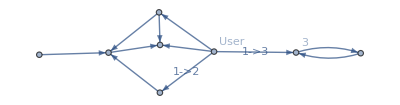

```mathematica
(* Test PathVerticesToEdges and EdgesBetween. *)
Graph[{},{}];
VertexAddWithProperties[%,1,VertexLabels->"User"];
VertexAdd[%,2];
EdgeAddWithProperties[%,1->2,EdgeLabels->"1->2"];
VertexAddLabeled[%,3];
EdgeAddLabeled[%,1->3];
VertexAdd[%,4];
EdgeAdd[%,1->4];
VertexAdd[%,5];
EdgeAdd[%,3->5];
EdgeAdd[%,5->3];
VertexAdd[%,6];
EdgeAdd[%,6->4];
VertexAdd[%,7];
EdgeAdd[%,7->6];
EdgeAdd[%,1->7];
EdgeAdd[%,7->4];
EdgeAdd[%,2->6];
VertexAdd[%,8];
EdgeAdd[%,8->6];
graphFunctionsTest=%
```

```mathematica
FindAllPaths[graphFunctionsTest,1,5]
FindAllPaths[graphFunctionsTest,1,4]
vertices=VerticesBetween[graphFunctionsTest,1,4]
edges=EdgesBetween[graphFunctionsTest,1,4]
```

{{1,3,5}}

{{1,4},{1,7,4},{1,7,6,4},{1,2,6,4}}

{1,4,7,6,2}

{1->4,1->7,7->4,7->6,6->4,1->2,2->6}

```mathematica
(* Analogues to the above specifically for paths from one vertex to another through some specified intermediate vertex. *)
FindAllPathsThrough[g_,v_,i_,w_]:=If[VertexList[g]=={},{},Select[FindPath[g,v,w,Infinity,All],(MemberQ[#,i])&]]
FindAllEdgePathsThrough[g_,v_,i_,w_]:=Map[PathVerticesToEdges,FindAllPathsThrough[g,v,i,w]]
VerticesBetweenThrough[g_,v_,i_,w_]:=DeleteDuplicates[Catenate[FindAllPathsThrough[g,v,i,w]]]
EdgesBetweenThrough[g_,v_,i_,w_]:=DeleteDuplicates[Catenate[FindAllEdgePathsThrough[g,v,i,w]]]
```

```mathematica
(* Find all the edges within the given list which point to the given vertex. *)
IncomingEdges[v_,es_]:=Select[es,MatchQ[_->v]]
IncomingEdgesList[vs_,es_]:=Map[(IncomingEdges[#,es])&,vs]
```

```mathematica
(* Test IncomingEdges. *)
IncomingEdges[7,edges]
IncomingEdgesList[vertices,edges]
IncomingEdgesList[VertexList[graphFunctionsTest],EdgeList[graphFunctionsTest]]
```

{1->7}

{{},{1->4,7->4,6->4},{1->7},{7->6,2->6},{1->2}}

{{},{1->2},{1->3,5->3},{1->4,6->4,7->4},{3->5},{7->6,2->6,8->6},{1->7},{}}

```mathematica
(* Find all the source vertices of the edges within the given list which point to the given vertex. *)
IncomingVertices[v_,es_]:=Map[SourceVertex,IncomingEdges[v,es]]
IncomingVerticesList[vs_,es_]:=Map[(IncomingVertices[#,es])&,vs]
```

```mathematica
(* Test IncomingVertices. *)
IncomingEdges[4,edges]
IncomingVertices[4,edges]
IncomingVerticesList[vertices,edges]
IncomingVerticesList[VertexList[graphFunctionsTest],EdgeList[graphFunctionsTest]]
```

{1->4,7->4,6->4}

{1,7,6}

{{},{1,7,6},{1},{7,2},{1}}

{{},{1},{1,5},{1,6,7},{3},{7,2,8},{1},{}}

```mathematica
(* Find all the edges within the given list which point from the given vertex. *)
OutgoingEdges[v_,es_]:=Select[es,MatchQ[v->_]]
OutgoingEdgesList[vs_,es_]:=Map[(OutgoingEdges[#,es])&,vs]
```

```mathematica
(* Test OutgoingEdges. *)
OutgoingEdges[7,edges]
OutgoingEdgesList[vertices,edges]
OutgoingEdgesList[VertexList[graphFunctionsTest],EdgeList[graphFunctionsTest]]
```

{7->4,7->6}

{{1->4,1->7,1->2},{},{7->4,7->6},{6->4},{2->6}}

{{1->2,1->3,1->4,1->7},{2->6},{3->5},{},{5->3},{6->4},{7->6,7->4},{8->6}}

```mathematica
(* Find all the target vertices of the edges within the given list which point from the given vertex. *)
OutgoingVertices[v_,es_]:=Map[TargetVertex,OutgoingEdges[v,es]]
OutgoingVerticesList[vs_,es_]:=Map[(OutgoingVertices[#,es])&,vs]
```

```mathematica
(* Test OutgoingVertices. *)
OutgoingEdges[4,edges]
OutgoingVertices[4,edges]
OutgoingEdges[7,edges]
OutgoingVertices[7,edges]
OutgoingVerticesList[vertices,edges]
OutgoingVerticesList[VertexList[graphFunctionsTest],EdgeList[graphFunctionsTest]]
```

{}

{}

{7->4,7->6}

{4,6}

{{4,7,2},{},{4,6},{4},{6}}

{{2,3,4,7},{6},{5},{},{3},{4},{6,4},{6}}

```mathematica
(* Find all the edges from the given list that point to or from the given vertex. *)
AdjacentEdges[v_,es_]:=DeleteDuplicates[Join[IncomingEdges[v,es],OutgoingEdges[v,es]]]
```

```mathematica
(* Remove all the edges adjacent to the given vertex from the given edge list. *)
CutEdges[v_,es_]:=Complement[es,AdjacentEdges[v,es]]
```

```mathematica
(* Test CutEdges. *)
CutEdges[7,EdgeList[graphFunctionsTest]]
```

{1->2,1->3,1->4,2->6,3->5,5->3,6->4,8->6}

```mathematica
(* Is an edge adjacent to the given vertex? *)
IsAdjacent[v_,e_]:=SourceVertex[e]==v∨TargetVertex[e]==v
```

```mathematica
(* Determine whether a path contains the given vertex. *)
PathContains[p_,v_]:=AnyTrue[p,(IsAdjacent[v,#])&]
```

```mathematica
(* Determine whether the given vertex is the start of the given path. *)
PathStart[φ_List]:=SourceVertex[φ[[1]]]
IsPathStart[v_,φ_List]:=PathStart[φ]==v
```

```mathematica
(* Determine whether the given vertex is the end of the given path. *)
PathEnd[φ_List]:=TargetVertex[φ[[-1]]]
IsPathEnd[v_,φ_List]:=PathEnd[φ]==v
```

```mathematica
(* Does the given graph have any edges? *)
HasEdges[g_]:=EdgeList[g]≠{}
```

```mathematica
(* Produce the subgraph of the given graph with the edge set reduced to the given one. *)
ReduceEdges[g_,es_]:=Module[{edges=Complement[EdgeList[g],es]},
If[edges=={},g,EdgeDelete[g,edges]]]
```

```mathematica
(* Remove any of the given edges which are in the given graph. *)
RemoveEdges[g_,es_]:=Module[{edges=Intersection[EdgeList[g],es]},
If[edges=={},g,EdgeDelete[g,edges]]]
```

```mathematica
(* Produce the subgraph of the given graph with the edge set reduced to those on paths from v to w. *)
RestrictEdges[g_,v_,w_]:=ReduceEdges[g,EdgesBetween[g,v,w]]
```

```mathematica
(* Produce the subgraph of the given graph with the edge set reduced to those on paths from v to w through i. *)
RestrictEdgesThrough[g_,v_,i_,w_]:=ReduceEdges[g,EdgesBetweenThrough[g,v,i,w]]
```

```mathematica
(* Change the edge list of the given graph to the given one. *)
ChangeEdges[g_,es_]:=EdgeAdd[ReduceEdges[g,es],Complement[es,EdgeList[g]]]
```

```mathematica
(* The edge lists of all graphs in the given list. *)
EdgeListList[g_]:=Map[EdgeList,g]
```

```mathematica
(* Graph versions of IncomingEdges and OutgoingEdges. *)
IncomingEdgesG[g_,v_]:=IncomingEdges[v,EdgeList[g]]
OutgoingEdgesG[g_,v_]:=OutgoingEdges[v,EdgeList[g]]
```

```mathematica
(* Graph versions of IncomingVertices and OutgoingVertices. *)
IncomingVerticesG[g_,v_]:=IncomingVertices[v,EdgeList[g]]
OutgoingVerticesG[g_,v_]:=OutgoingVertices[v,EdgeList[g]]
```

```mathematica
(* Test whether a node is a source node. *)
IsSourceNode[g_,n_]:=SameQ[IncomingEdgesG[g,n],{}]
```

```mathematica
(* The set of nodes with no incoming edges. *)
SourceNodes[g_]:=Select[VertexList[g],(IsSourceNode[g,#])&]
```

```mathematica
(* Find all the cycles in a graph. *)
FindAllCycles[g_]:=FindCycle[g,Infinity,All]
```

```mathematica
(* Is the given graph acyclic? *)
IsDAG[g_]:=FindAllCycles[g]=={}
```

```mathematica
(* Find a list of sets of edges the removal of any of which sets would remove all the cycles from the given graph. (In particular, if the given graph is acyclic, this returns an empty list. *)
FindAllCycleRemovalEdgeSets[g_]:=Module[{cs=FindAllCycles[g]},If[cs=={},{{}},DeleteDuplicates[Map[DeleteDuplicates,Tuples[cs]]]]]
```

```mathematica
(* Find all the maximal acyclic subgraphs of the given graph. *)
FindAcyclicSubgraphs[g_]:=Map[(If[#=={},g,EdgeDelete[g,#]])&,FindAllCycleRemovalEdgeSets[g]]
```

```mathematica
(* Find the edges within the given graph comprising the maximal source-sink acyclic graphs from the first given node to the second. *)
FindAcyclicSTEdgeSets[g_,v_,w_]:=
Module[{subdags=FindAcyclicSubgraphs[g]},
If[v==w,
(* There's exactly one ST graph from a vertex to itself, which has no edges. *)
{EdgeList[g]},
If[subdags=={},
{{}},
DeleteNonmaximal[Select[Map[(EdgesBetween[#,v,w])&,subdags],UnsameQ[#,{}]&]]]]]
```

```mathematica
(* Find all the acyclic source-target subgraphs of the given graph with source v and sink w. *)
FindAcyclicSubSTGraphs[g_,v_,w_]:=Module[{gr=RestrictEdges[g,v,w]},Map[(ReduceEdges[gr,#])&,FindAcyclicSTEdgeSets[gr,v,w]]]
```

```mathematica
(* Is the given graph an ST-DAG with the given source and target? *)
IsSTDAG[g_,v_,w_]:=IsDAG[g]∧SetsEqual[EdgeList[g],EdgesBetween[g,v,w]]
```

```mathematica
(* These are utility functions for TopologicalInduction (see below). They implement a standard topological sort algorithm, enhanced by a caller-specified "visit" routine for each node. *)
TopologicalInductionRemoveOutgoingEdges[visitf_,gorig_,g_,sort_,accum_,s_,n_]:=
Module[{es},
es=OutgoingEdgesG[g,n];
If[es=={},
TopologicalInductionInternal[visitf,gorig,g,sort,accum,s],
Module[{e,nextg,m,nexts},
e=First[es];
nextg=EdgeDelete[g,e];
m=TargetVertex[e];
nexts=If[IsSourceNode[nextg,m],Append[s,m],s];
TopologicalInductionRemoveOutgoingEdges[visitf,gorig,nextg,sort,accum,nexts,n]
]
]
]
TopologicalInductionInternal[visitf_,gorig_,g_,sort_,accum_,{}]:=
(Assert[HasEdges[g]==False];accum)
TopologicalInductionInternal[visitf_,gorig_,g_,sort_,accum_,s_]:=
Module[{n=First[s],t=Rest[s],newsort,parents,sortedparents},
newsort=Append[sort,n];
parents=Map[SourceVertex,IncomingEdgesG[gorig,n]];
Assert[SubsetQ[sort,parents]];
sortedparents=Select[sort,(MemberQ[parents,#])&];
TopologicalInductionRemoveOutgoingEdges[visitf,gorig,g,newsort,visitf[accum,n,sort,sortedparents],t,n]
]
```

```mathematica
(* Topological induction is an inductive principle which uses a standard algorithm for topological sort but allows the caller to specify a "visit" routine which is called on each node when its position in the topological sort is first established, and to thread the output of that routine through "accum" (the initial value, or base case of the induction, also specified by the caller). The visit routine receives as parameters the latest value of "accum", the node being visited, the topological sort up to (but not including) the node being visited, and the parents of the node being visited in topological sort order. *)
TopologicalInduction[initial_,visitf_,g_]:=
TopologicalInductionInternal[visitf,g,g,{},initial,SourceNodes[g]]
```

```mathematica
(* Return a topological sort of the given graph, which must be a DAG.  A given DAG may have more than one topological sort, so if the caller's algorithm is intended to produce some single unique result for any given graph, then it must ensure that any topological sort of that graph produces the same result. *)
TopoSort[g_]:=TopologicalInduction[{},Function[{accum,n,predsort,parents},Append[predsort,n]],g]
```

```mathematica
(* Return an association containing, for each node in the given graph, that node's parents and ancestors (in topological sort order). *)
TopoSortParentsAndAncestors[g_]:=TopologicalInduction[<||>,
Function[{assoc,n,predsort,parents},
Module[{ancestors},
ancestors=DeleteDuplicates[Join[Select[predsort,
Function[{pred},AnyTrue[parents,
Function[{parent},MemberQ[assoc[parent][[2]],pred]]]]],
parents]];
Append[assoc,n->{parents,ancestors}]
]
],
g
]
```

## Propagation Graphs I: Graph Partitioning

This section is probably more important to read than “Graph Utility Functions”, because, while the functions defined herein still qualify as generic graph theory, these are the ones whose use distinguishes SPIL’s graph handling from other applications of graph theory of which I’m personally aware (and indeed I’m not aware specifically of a prior definition of what I’m calling “clean” and “complete” vertex cuts below, or of the concept derived from them that I’m calling “maximal partitionable edge sets”, although they are sufficiently simple and generic that I strongly suspect that they have been documented long ago, and that I just haven’t found that documentation yet).

```mathematica
(* Find all of the non-intersecting edge sets within a DAG on paths leading from each node to each of its descendents. *)
PartitionableDAGEdgeSubsets[g_]:=
TopologicalInduction[<||>,
Function[{nodes2subsets,n,predsort,parents},
Module[{parents2subsets,parentchoices,subsetsperchoice},
Append[nodes2subsets,
n->If[IsSourceNode[g,n],
{{}},
(parents2subsets=AssociationMapFixed[
Function[{parent,subsets},
Map[(Append[#,parent->n])&,subsets]
],
KeySelect[nodes2subsets,(MemberQ[parents,#])&]
];
parentchoices=Complement[Subsets[parents],{{}}];
subsetsperchoice=Map[
Function[{parentchoice},
Module[{subsetlist,subsetchoices,disjointsubsetchoices},
subsetlist=Map[parents2subsets[#]&,parentchoice];
subsetchoices=Tuples[subsetlist];
disjointsubsetchoices=Select[subsetchoices,PairwiseDisjoint];
Map[Catenate,disjointsubsetchoices]
]
],
parentchoices
];
DeleteDuplicates[Catenate[subsetsperchoice]])
]
]
]
],
g
]
```

```mathematica
(* Find all of the non-intersecting edge paths within a graph on paths leading from one node to another. *)
PartitionableEdgeSubsets[g_,v_,w_]:=DeleteDuplicates[Catenate[Map[PartitionableDAGEdgeSubsets[#][w]&,FindAcyclicSubSTGraphs[g,v,w]]]]
```

```mathematica
(* Find all of the maximal non-intersecting edge sets within a graph on paths from one node to another. *)
(* XXX This is an attempt at an alternative, more efficient form of MaximalPartitionableEdgeSubsets, but it does not yet find subsets as large as the former does. If it can be made equivalent with a better computational complexity, then it should be used to replace MaximalPartitionableEdgeSubsets (below). *)
MaximalPartitionableEdgeSubsetsAlternate[g_,v_,w_]:=DeleteNonmaximal[PartitionableEdgeSubsets[g,v,w]]
```

```mathematica
(* These graph-theoretical functions capture SPIL's cycle-avoidance and double-counting-avoidance. MaximalPartitionableEdgeSubsets (for which the preceding functions are utilities) generates the set of maximal subgraphs of the given graph which can be partitioned into further subgraphs by a "complete vertex cut".  A complete vertex cut is a vertex cut which does not merely disconnect the given graph (which is the definition simply of a vertex cut) but which partitions it -- meaning that the subgraphs generated by paths through each vertex in the cut are a partition of the full graph, i.e. are pairwise disjoint and among them cover the whole graph. The maximal flow of trust/belief through a graph without double-counting any edges and without propagating trust through any cycles, therefore, is the maximal flow through any of its maximal partitionable edge subsets -- which is a _join_ of the flows of each of its maximal partitionable edge subsets. *)
CutInducedEdgeSetAssociation[g_,v_,w_,vc_]:=AssociationMap[(EdgesBetweenThrough[g,v,#,w])&,vc]
CutInducedEdgeSets[g_,v_,w_,vc_]:=Values[CutInducedEdgeSetAssociation[g,v,w,vc]]
IsCleanVertexCut[g_,v_,w_,vc_]:=IsVertexCut[g,v,w,vc]∧(PairwiseDisjoint[CutInducedEdgeSets[g,v,w,vc]])
IsCompleteVertexCut[g_,v_,w_,vc_]:=IsCleanVertexCut[g,v,w,vc]∧(SetsEqual[Catenate[CutInducedEdgeSets[g,v,w,vc]],EdgesBetween[g,v,w]])
CleanVertexCuts[g_,v_,w_]:=Select[FindMinVertexCuts[g,v,w],(IsCleanVertexCut[g,v,w,#])&]
HasCleanVertexCut[g_,v_,w_]:=(Assert[FindPath[g,v,w]≠{}];CleanVertexCuts[g,v,w]≠{})
CompleteVertexCuts[g_,v_,w_]:=Select[FindMinVertexCuts[g,v,w],(IsCompleteVertexCut[g,v,w,#])&]
HasCompleteVertexCut[g_,v_,w_]:=(Assert[FindPath[g,v,w]≠{}];CompleteVertexCuts[g,v,w]≠{})
ChooseCompleteVertexCut[g_,v_,w_]:=Module[{vcs=CompleteVertexCuts[g,v,w]},
If[vcs=={},{},vcs[[1]]]
]
IsPartitionableEdgeSubset[g_,v_,w_,possiblevcs_,es_]:=Module[{rg=ReduceEdges[g,es]},
Assert[v≠w];
Assert[FindPath[g,v,w]≠{}];
Assert[IsSubset[es,EdgesBetween[g,v,w]]];
(FindPath[rg,v,w]≠{})∧(AnyTrue[possiblevcs,(IsCompleteVertexCut[rg,v,w,#])&])]
MaximalPartitionableEdgeSubsets[g_,v_,w_]:=Module[{possiblevcs,edgeList,edgesToRemove,candidates,cycleRemovalEdgeSets,output},
Assert[v≠w];
Assert[FindPath[g,v,w]≠{}];
edgeList=EdgeList[g];
(* The "EdgeConnectivity" here is an optimization which I am not even certain is correct -- even with this optimization, the SPIL algorithm as implemented in this document has a ridiculous computational complexity. Its purpose is to demonstrate the algorithm's exact theoretical outputs in small illustrative cases. A real, live system would almost certainly use a conservative approximation, perhaps one that ran on very frequent snapshots of the trust/belief graph, while a slower, more thorough algorithm that produced something closer to (or exactly equal to) the maximum theoretical values of all net trusts and beliefs might run on far less frequent snapshots. Even an exact algorithm which was guaranteed to produce theoretically maximal outputs could almost certainly be written vastly more efficiently than the one in _this_ paper. The idea of the "EdgeConnectivity" specifically is that I suspect (but have not proven!) that the edge connectivity is an upper bound on the size of the largest subset of edges that needs to be removed to generate all of the maximal partitionable edge subsets. If that is wrong, then the {0,EdgeConnectivity+1} term here could simply be removed entirely, so that "edgesToRemove" would comprise all subsets. Either way the algorithm is ludicrous in terms of efficiency; this is a demonstration only!

We compute the vertex cuts of g itself and then pass them and their subsets as a set of candidates to IsPartitionableEdgeSubset: any minimal vertex cut of a subgraph of g must be a (not necessarily strict) subset of a minimal vertex cut of g. That we we don't have to recompute the minimal vertex subsets within each call to IsPartitionableEdgeSubset. *)
possiblevcs=DeleteDuplicates[Catenate[Map[Subsets,FindMinVertexCuts[g,v,w]]]];
edgesToRemove=Subsets[edgeList,{0,EdgeConnectivity[g,v,w]+1}];
candidates=Map[(Complement[edgeList,#])&,edgesToRemove];
(* We only consider edge sets that produce v->w-connected graphs. *)
candidates=DeleteDuplicates[Map[(EdgeList[RestrictEdges[ReduceEdges[g,#],v,w]])&,candidates]];
output=DeleteNonmaximal[Select[candidates,(IsPartitionableEdgeSubset[g,v,w,possiblevcs,#])&]];
output
]
```

## Propagation Graphs II: Declaring Trust and Belief

Definitions

```mathematica
(* Check whether a vertex is of type "user". *)
VertexIsUser[g_,n_]:=VertexHasType[g,n,"user"]
```

```mathematica
(* Assert that a vertex is of type "user". *)
AssertIsUser[g_,n_]:=AssertVertexType[g,n,"user"]
```

```mathematica
(* Add a vertex of type "user" to an existing graph. *)
AddUser[g_,name_]:=VertexAddNextWithProperties[g,{"vType"->"user","name"->name,VertexLabels->ToString[VertexCount[g]+1]<>":"<>name}]
```

```mathematica
(* A graph containing one user and no propositions. *)
g1:=AddUser[g0,"User 1"]
```

```mathematica
(* Add a vertex of type "proposition" to an existing graph. *)
AddProp[g_,t_,name_,p_]:=VertexAddNextWithProperties[g,Join[{"vType"->"prop","pType"->t,"name"->name,VertexLabels->ToString[VertexCount[g]+1]<>":"<>name},p]]
```

```mathematica
(* Check whether a vertex is of type "proposition". *)
VertexIsProp[g_,n_]:=VertexHasType[g,n,"prop"]
```

```mathematica
(* Assert that a vertex is of type "proposition". *)
AssertIsProp[g_,n_]:=Assert[VertexIsProp[g,n]]
```

```mathematica
(* Various vertex filters. *)
AllUsers[g_]:=Select[VertexList[g],VertexIsUser[g,#]&]
AllOtherUsers[g_,u_]:=Complement[AllUsers[g],{u}]
AllProps[g_]:=Select[VertexList[g],VertexIsProp[g,#]&]
AllOtherProps[g_,p_]:=Complement[AllProps[g],{p}]
```

```mathematica
(* Add an atomic proposition to an existing graph. *)
AddAtomic[g_,name_]:=AddProp[g,"atomic",name,{}]
```

```mathematica
(* Add a "dot" node -- a node that combines belief in an implication with belief in an antecedent to obtain belief in a consequent. *)
AddDot[g_,i_,a_,c_]:=VertexAddNextWithProperties[g,{"vType"->"dot","imp"->i,"ant"->a,"cons"->c,VertexLabels->{"("<>VertexName[g,i]<>")⊙("<>VertexName[g,a]<>")"}}]
```

```mathematica
(* Add a "contradot" node -- a node that combines belief in an implication with disbelief in a consequent to obtain disbelief in an antecedent. *)
AddContradot[g_,i_,a_,c_]:=VertexAddNextWithProperties[g,{"vType"->"contradot","imp"->i,"ant"->a,"cons"->c,VertexLabels->{"("<>VertexName[g,i]<>")⊖("<>VertexName[g,c]<>")"}}]
```

```mathematica
(* Add trust by a user in another user to an existing graph. *)
AddTrust[g_,u_,w_,v_]:=(AssertIsUser[g,u];AssertIsUser[g,w];
EdgeAddWithProperties[g,u->w,{"eType"->"t","trust"->v,EdgeLabels->("t:"<>ToString[u]<>"->"<>ToString[w])}])
```

```mathematica
(* Assert that an edge has type "trust". *)
AssertIsTrust[g_,a_,b_]:=AssertEdgeType[g,a,b,"t"]
```

```mathematica
(* Retrieve the belief vector from a trust edge. If no trust has been explicitly assigned, return Uncertain. *)
GetTrust[g_,e_]:=With[{u=SourceVertex[e],w=TargetVertex[e]},If[EdgeHasProperty[g,"trust",u,w],(AssertIsTrust[g,u,w];EdgeProperty[g,"trust",u,w]),Uncertain]]
```

```mathematica
(* Add belief by a user in a proposition to an existing graph. *)
AddBelief[g_,u_,n_,v_]:=(AssertIsUser[g,u];AssertIsProp[g,n];
EdgeAddWithProperties[g,u->n,{"eType"->"b","belief"->v,EdgeLabels->("b:"<>ToString[u]<>"->"<>ToString[n])}])
```

```mathematica
(* Assert that an edge has type "belief". *)
AssertIsBelief[g_,a_,b_]:=AssertEdgeType[g,a,b,"b"]
```

```mathematica
(* Retrieve the belief vector from a belief edge. If no belief has been explicitly assigned, return Uncertain. *)
GetBelief[g_,e_]:=With[{u=SourceVertex[e],w=TargetVertex[e]},If[EdgeHasProperty[g,"belief",u,w],(AssertIsBelief[g,u,w];EdgeProperty[g,"belief",u,w]),Uncertain]]
```

```mathematica
GetVector[g_,e_]:=Switch[EdgeType[g,SourceVertex[e],TargetVertex[e]],
"t",GetTrust[g,e],
"b",GetBelief[g,e],
_,Assert[False]]
```

```mathematica
(* Add the negation (the only unary constructor) of an existing proposition to the graph. *)
AddNewNegationEdge[g_,m_,n_]:=(AssertIsProp[g,m];AssertIsProp[g,n];EdgeAddWithProperties[g,m->n,{"eType"->"n",EdgeLabels->("n:"<>ToString[m]<>"->"<>ToString[n])}])
AddNewNegationEdges[g_,n_]:=AddNewNegationEdge[AddNewNegationEdge[g,VertexCount[g],n],n,VertexCount[g]]
AddNegation[g_,n_]:=(AssertIsProp[g,n];AddNewNegationEdges[AddProp[g,"negation","¬("<>VertexName[g,n]<>")",{"negand"->n}],n])
```

```mathematica
(* Add a proposition representing (intuitionistic) implication from p_ to q_. In addition to the vertex representing p⇒q itself, this also creates a "dot" node, which propagates belief in p⇒q and belief in p to belief in q, and a "contradot" node, which propagates belief in p⇒q and disbelief in q to disbelief in p, along with all the edges that connect them. *)
AddImplication[g_,p_,q_]:=Module[{h=g,piq=VertexCount[g]+1,pdq=VertexCount[g]+2,pcq=VertexCount[g]+3},(AssertIsProp[g,p];AssertIsProp[g,q];h=AddProp[h,"imp","("<>VertexName[h,p]<>")⇒("<>VertexName[h,q]<>")",{"ant"->p,"cons"->q}];
h=AddDot[h,piq,p,q];
h=AddContradot[h,piq,p,q];
h=EdgeAddWithProperties[h,piq->pdq,{"eType"->"i2d",EdgeLabels->("i2d:"<>ToString[piq]<>"->"<>ToString[pdq])}];h=EdgeAddWithProperties[h,p->pdq,{"eType"->"a2d",EdgeLabels->("a2d:"<>ToString[p]<>"->"<>ToString[pdq])}];h=EdgeAddWithProperties[h,pdq->q,{"eType"->"d2cq",EdgeLabels->("d2cq:"<>ToString[pdq]<>"->"<>ToString[q])}];h=EdgeAddWithProperties[h,piq->pcq,{"eType"->"i2cd",EdgeLabels->("i2cd:"<>ToString[piq]<>"->"<>ToString[pcq])}];h=EdgeAddWithProperties[h,q->pcq,{"eType"->"cq2cd",EdgeLabels->("cq2cd:"<>ToString[q]<>"->"<>ToString[pcq])}];h=EdgeAddWithProperties[h,pcq->p,{"eType"->"cd2a",EdgeLabels->("cd2a:"<>ToString[pcq]<>"->"<>ToString[p])}];
h)]
```

```mathematica
(* Add implications in both directions between the given propositions. *)
AddImplications[g_,p_,q_]:=AddImplication[AddImplication[g,p,q],q,p]
```

Tests and Examples

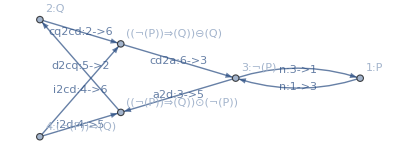

```mathematica
(* This simple case illustrates the graph resulting from a use of the two propositional connectives implemented so far, negation and implication. *)
g0;
AddAtomic[%,"P"];
AddAtomic[%,"Q"];
AddNegation[%,1];
AddImplication[%,3,2]
```

## Propagation Graphs III: Propagation Formulas

Definitions

```mathematica
(* This utility function takes a complete vertex cut of a connected graph and returns the independent attenuated flows through each vertex in the cut. It also provides the corresponding subgraphs. *)
AttenuatedFlowsThroughCut[selfpath_,nopath_,joinf_,ef_,chf_,mergef_,gorig_,g_,v_,w_,vc_]:=
Module[{gs,lefts,rights},
Assert[IsCompleteVertexCut[g,v,w,vc]];
gs=AssociationMapFixed[(ReduceEdges[g,#2])&,CutInducedEdgeSetAssociation[g,v,w,vc]];
lefts=AssociationMap[(AttenuatedFlowInternal[selfpath,nopath,joinf,ef,chf,mergef,gorig,gs[#],v,#])&,vc];
rights=AssociationMap[(AttenuatedFlowInternal[selfpath,nopath,joinf,ef,chf,mergef,gorig,gs[#],#,w])&,vc];
Assert[MemberQ[Map[EdgeList,gs],{}]==False];
Assert[AllTrue[gs,(FindPath[#,v,w]≠{})&]];
{Map[(gs[#])&,vc],Map[(chf[gorig,v,#,gs[#],w,lefts[#],rights[#]])&,vc]}
]
```

```mathematica
(* This is the core function for calculating attenuated flow, which recursively partitions an source-target graph with complete vertex cuts, and calls AttenuatedFlowThroughCut to chain and merge the attenuated flows of the maximal independent subgraphs generated by the vertex cuts. When a graph has no complete vertex cuts, we generate the join of all of the maximal subgraphs of it which _do_ have complete vertex cuts. The use of complete vertex cuts -- which partition the graph into subgraphs with no edges in common -- by AttenuatedFlowInternal is SPIL's way of avoiding double-counting, which it needs because, as described in the introduction, EBSL's method of using a left-distributive discount (propagate) operator makes it impossible for that operator to be bounded by its left argument, which I consider a vital security property. *)
AttenuatedFlowInternal[selfpath_,nopath_,joinf_,ef_,chf_,mergef_,gorig_,g_,v_,w_]:=Module[{de,he,ve,reducedg,vc,es,gs,fullgs,attenuatedflowpair,reducedflows,allflows},
Assert[GraphHasVertex[g,v]];
Assert[GraphHasVertex[g,w]];
If[v==w,
selfpath,
(de=v->w;
he=GraphHasEdge[g,de];
ve=If[he,ef[gorig,de],nopath];
reducedg=RestrictEdges[If[he,EdgeDelete[g,de],g],v,w];
If[FindPath[reducedg,v,w]=={},
If[he,ve,nopath],
(Assert[VertexCount[reducedg]>2];
vc=ChooseCompleteVertexCut[reducedg,v,w];
If[vc≠{},
(attenuatedflowpair=AttenuatedFlowsThroughCut[selfpath,nopath,joinf,ef,chf,mergef,gorig,reducedg,v,w,vc];
gs=attenuatedflowpair[[1]];
reducedflows=attenuatedflowpair[[2]];
Assert[reducedflows≠{}];
fullgs=If[he,Prepend[gs,ReduceEdges[g,{de}]],gs];
allflows=If[he,Prepend[reducedflows,ve],reducedflows];
If[Length[allflows]==1,allflows[[1]],mergef[gorig,v,fullgs,w,allflows]]),
(es=MaximalPartitionableEdgeSubsets[reducedg,v,w];
Assert[es≠{}];
Assert[MemberQ[es,EdgeList[reducedg]]==False];
gs=Map[(ReduceEdges[reducedg,#])&,es];
fullgs=If[he,Map[(EdgeAdd[#,de])&,gs],gs];
allflows=Map[(AttenuatedFlowInternal[selfpath,nopath,joinf,ef,chf,mergef,gorig,#,v,w])&,fullgs];
If[Length[allflows]==1,allflows[[1]],joinf[gorig,v,fullgs,w,allflows]])
]
)
]
)
]
]
```

```mathematica
(* AttenuatedFlow is the core graph-theoretical part of SPIL.  It is purely graph-theoretical; its generic function parameters are the way that SPIL uses it to make the vertices and edges represent users/propositions and trust/belief/inference. It uses MaximalPartitionableEdgeSubsets as described in the documentation to that function above (and optimizes out the join when there is only one maximal partitionable edge subset, which in that case must simply be the whole graph). Because it computes flow through a graph in terms of flow through a vertex cut, it resembles the maximum-flow problem, where the maximum flow through the graph equals the flow through a minimal edge cut. However, trust does not flow in quite the same way as flow in the typical maximum-flow network problem. In particular, it does not divide when it flows out of a node through multiple edges: the trust that I inherit in your cousin through my trust in you and your trust in your cousin does not divide in half when you begin to trust your professor as well. Instead, I simply start trusting your professor to some degree as well. However, trust does _attenuate_ as it passes through each node, even if it does _not_ split there, because trust is never complete, and it diminishes as it grows less direct. This may well be some already-named mathematical structure, but I have not been able to find it precisely, so for now I am using the name "attenuated flow". *)
AttenuatedFlow[selfpath_,nopath_,joinf_,ef_,chf_,mergef_,g_,v_,w_]:=AttenuatedFlowInternal[selfpath,nopath,joinf,ef,chf,mergef,g,g,v,w]
```

```mathematica
(* This is a convenient wrapper for exploring the workings of AttenuatedFlow: it produces symbolic output using the standard symbols we have adopted for join (⋁), chain/propagate (⊗), and merge/consensus (⊕). *)
AttenuatedFlowDefault[ef_,g_,v_,w_]:=AttenuatedFlow[Proven,Uncertain,𝔍[#5]&,ef[#2]&,𝔓[{#6,#7}]&,ℭ[#5]&,g,v,w]
```

Tests and Examples

```mathematica
(* Sanity checks of the trivial cases of AttenuatedFlow. *)
AttenuatedFlowDefault[ef,Graph[{1},{}],1,1]
AttenuatedFlowDefault[ef,Graph[{1,2},{}],1,2]
AttenuatedFlowDefault[ef,Graph[{1,2},{1->2}],1,2]
```

{1,0,0}

{0,0,1}

ef[1->2]

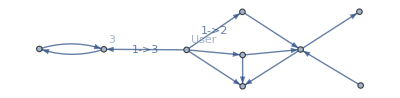

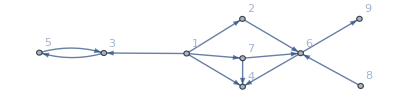

```mathematica
(* Here we make the earlier graphFunctionsTest slightly messier and then use it to illustrate a couple properties of AttenuatedFlow. *)
VertexAdd[graphFunctionsTest,9];
EdgeAdd[%,6->9];
attenuatedFlowTest=%
DefaultGraphPlot[attenuatedFlowTest]
```

```mathematica
(* Experiment with ConnectedComponents as a possible aid to optimizing MaximalPartitionableEdgeSubsets. *)
ConnectedComponents[RestrictEdges[attenuatedFlowTest,1,9]]
ConnectedComponents[RestrictEdges[attenuatedFlowTest,1,4]]
```

{{9},{6},{2},{7},{1},{3},{4},{5},{8}}

{{4},{6},{2},{7},{1},{3},{5},{8},{9}}

```mathematica
(* Here we see that when propagating from 1 to 9, AttenuatedFlow first merges the two independent paths which lead to the intermediate node of 6, and then chains the result along the edge to 9. The result manifestly avoids double-counting despite the non-distributivity of ⊗. *)
AttenuatedFlowDefault[ef,attenuatedFlowTest,1,9]
```

(ef[1->2]⊗ef[2->6]⊕ef[1->7]⊗ef[7->6])⊗ef[6->9]

```mathematica
(* Here we see how AttenuatedFlow maximizes flow in the case where there is no way to use all the edges leading from 1 to 4 at once without double-counting any of them: it produces a join of the three different ways of removing just enough edges to allow the remaining edges all to be used. The first of the three expressions being joined is the flow that would result from not using the path 1->2->6; the second results from not using the path 7->6; the third results from not using the path 7->4. *)
AttenuatedFlowDefault[ef,attenuatedFlowTest,1,4]
```

((ef[1->4]⊕ef[1->7]⊗(ef[7->4]⊕ef[7->6]⊗ef[6->4]))⋁((ef[1->4]⊕ef[1->2]⊗(ef[2->6]⊗ef[6->4]))⊕ef[1->7]⊗ef[7->4]))⋁(ef[1->4]⊕(ef[1->2]⊗ef[2->6]⊕ef[1->7]⊗ef[7->6])⊗ef[6->4])

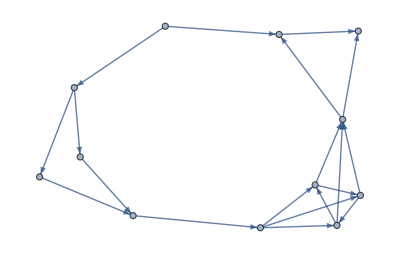

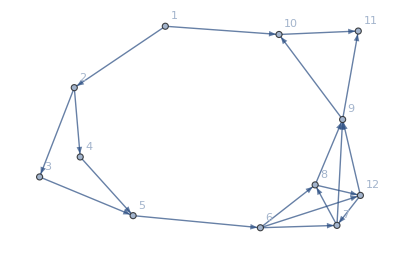

```mathematica
(* This graph is messy enough to produce a result that I haven't bothered to read in full; it's here just as a miniature "stress test". *)
VertexAdd[g0,1];
VertexAdd[%,2];
EdgeAdd[%,1->2];
VertexAdd[%,3];
VertexAdd[%,4];
EdgeAdd[%,2->3];
EdgeAdd[%,2->4];
VertexAdd[%,5];
EdgeAdd[%,3->5];
EdgeAdd[%,4->5];
VertexAdd[%,6];
EdgeAdd[%,5->6];
VertexAdd[%,7];
VertexAdd[%,8];
EdgeAdd[%,6->7];
EdgeAdd[%,6->8];
EdgeAdd[%,7->8];
VertexAdd[%,9];
EdgeAdd[%,7->9];
EdgeAdd[%,8->9];
VertexAdd[%,10];
VertexAdd[%,11];
EdgeAdd[%,1->10];
EdgeAdd[%,10->11];
EdgeAdd[%,9->11];
VertexAdd[%,12];
EdgeAdd[%,6->12];
EdgeAdd[%,12->9];
EdgeAdd[%,8->12];
EdgeAdd[%,12->7];
EdgeAdd[%,9->10];
flowExperiment=%
DefaultGraphPlot[flowExperiment]
```

```mathematica
(* Experiment with ConnectedComponents as a possible aid to optimizing MaximalPartitionableEdgeSubsets. *)
ConnectedComponents[RestrictEdges[flowExperiment,1,11]]
```

{{11},{10},{9},{7,8,12},{6},{5},{3},{4},{2},{1}}

```mathematica
AttenuatedFlowDefault[ef,flowExperiment,1,11]
```

(((ef[1->10]⊕ef[1->2]⊗((ef[2->3]⊗ef[3->5]⊕ef[2->4]⊗ef[4->5])⊗(ef[5->6]⊗(((((((((((((((((ef[6->12]⊕(ef[6->8]⊕ef[6->7]⊗ef[7->8])⊗ef[8->12])⊗ef[12->9])⋁((ef[6->8]⊕(ef[6->7]⊕ef[6->12]⊗ef[12->7])⊗ef[7->8])⊗ef[8->9]))⋁((ef[6->8]⊕ef[6->7]⊗ef[7->8])⊗ef[8->9]⊕ef[6->12]⊗ef[12->9]))⋁((ef[6->8]⊕ef[6->7]⊗ef[7->8])⊗(ef[8->9]⊕ef[8->12]⊗ef[12->9])))⋁((ef[6->7]⊕(ef[6->12]⊕ef[6->8]⊗ef[8->12])⊗ef[12->7])⊗ef[7->9]))⋁(ef[6->7]⊗ef[7->9]⊕(ef[6->12]⊕ef[6->8]⊗ef[8->12])⊗ef[12->9]))⋁((ef[6->7]⊕ef[6->12]⊗ef[12->7])⊗ef[7->9]⊕ef[6->8]⊗ef[8->9]))⋁((ef[6->7]⊗ef[7->9]⊕ef[6->8]⊗ef[8->9])⊕ef[6->12]⊗ef[12->9]))⋁(ef[6->7]⊗ef[7->9]⊕ef[6->8]⊗(ef[8->9]⊕ef[8->12]⊗ef[12->9])))⋁((ef[6->7]⊕ef[6->12]⊗ef[12->7])⊗(ef[7->9]⊕ef[7->8]⊗ef[8->9])))⋁(ef[6->7]⊗(ef[7->9]⊕ef[7->8]⊗ef[8->9])⊕ef[6->12]⊗ef[12->9]))⋁(ef[6->7]⊗(ef[7->9]⊕ef[7->8]⊗(ef[8->9]⊕ef[8->12]⊗ef[12->9]))))⋁((ef[6->12]⊕ef[6->8]⊗ef[8->12])⊗(ef[12->9]⊕ef[12->7]⊗ef[7->9])))⋁(ef[6->8]⊗ef[8->9]⊕ef[6->12]⊗(ef[12->9]⊕ef[12->7]⊗ef[7->9])))⋁(ef[6->8]⊗(ef[8->9]⊕ef[8->12]⊗(ef[12->9]⊕ef[12->7]⊗ef[7->9]))))⋁(ef[6->12]⊗(ef[12->9]⊕ef[12->7]⊗(ef[7->9]⊕ef[7->8]⊗ef[8->9])))⊗ef[9->10]))))⊗ef[10->11])⋁(ef[1->2]⊗((ef[2->3]⊗ef[3->5]⊕ef[2->4]⊗ef[4->5])⊗(ef[5->6]⊗(((((((((((((((((ef[6->12]⊕(ef[6->8]⊕ef[6->7]⊗ef[7->8])⊗ef[8->12])⊗ef[12->9])⋁((ef[6->8]⊕(ef[6->7]⊕ef[6->12]⊗ef[12->7])⊗ef[7->8])⊗ef[8->9]))⋁((ef[6->8]⊕ef[6->7]⊗ef[7->8])⊗ef[8->9]⊕ef[6->12]⊗ef[12->9]))⋁((ef[6->8]⊕ef[6->7]⊗ef[7->8])⊗(ef[8->9]⊕ef[8->12]⊗ef[12->9])))⋁((ef[6->7]⊕(ef[6->12]⊕ef[6->8]⊗ef[8->12])⊗ef[12->7])⊗ef[7->9]))⋁(ef[6->7]⊗ef[7->9]⊕(ef[6->12]⊕ef[6->8]⊗ef[8->12])⊗ef[12->9]))⋁((ef[6->7]⊕ef[6->12]⊗ef[12->7])⊗ef[7->9]⊕ef[6->8]⊗ef[8->9]))⋁((ef[6->7]⊗ef[7->9]⊕ef[6->8]⊗ef[8->9])⊕ef[6->12]⊗ef[12->9]))⋁(ef[6->7]⊗ef[7->9]⊕ef[6->8]⊗(ef[8->9]⊕ef[8->12]⊗ef[12->9])))⋁((ef[6->7]⊕ef[6->12]⊗ef[12->7])⊗(ef[7->9]⊕ef[7->8]⊗ef[8->9])))⋁(ef[6->7]⊗(ef[7->9]⊕ef[7->8]⊗ef[8->9])⊕ef[6->12]⊗ef[12->9]))⋁(ef[6->7]⊗(ef[7->9]⊕ef[7->8]⊗(ef[8->9]⊕ef[8->12]⊗ef[12->9]))))⋁((ef[6->12]⊕ef[6->8]⊗ef[8->12])⊗(ef[12->9]⊕ef[12->7]⊗ef[7->9])))⋁(ef[6->8]⊗ef[8->9]⊕ef[6->12]⊗(ef[12->9]⊕ef[12->7]⊗ef[7->9])))⋁(ef[6->8]⊗(ef[8->9]⊕ef[8->12]⊗(ef[12->9]⊕ef[12->7]⊗ef[7->9]))))⋁(ef[6->12]⊗(ef[12->9]⊕ef[12->7]⊗(ef[7->9]⊕ef[7->8]⊗ef[8->9])))⊗ef[9->11])))⊕ef[1->10]⊗ef[10->11]))⋁(ef[1->2]⊗((ef[2->3]⊗ef[3->5]⊕ef[2->4]⊗ef[4->5])⊗(ef[5->6]⊗(((((((((((((((((ef[6->12]⊕(ef[6->8]⊕ef[6->7]⊗ef[7->8])⊗ef[8->12])⊗ef[12->9])⋁((ef[6->8]⊕(ef[6->7]⊕ef[6->12]⊗ef[12->7])⊗ef[7->8])⊗ef[8->9]))⋁((ef[6->8]⊕ef[6->7]⊗ef[7->8])⊗ef[8->9]⊕ef[6->12]⊗ef[12->9]))⋁((ef[6->8]⊕ef[6->7]⊗ef[7->8])⊗(ef[8->9]⊕ef[8->12]⊗ef[12->9])))⋁((ef[6->7]⊕(ef[6->12]⊕ef[6->8]⊗ef[8->12])⊗ef[12->7])⊗ef[7->9]))⋁(ef[6->7]⊗ef[7->9]⊕(ef[6->12]⊕ef[6->8]⊗ef[8->12])⊗ef[12->9]))⋁((ef[6->7]⊕ef[6->12]⊗ef[12->7])⊗ef[7->9]⊕ef[6->8]⊗ef[8->9]))⋁((ef[6->7]⊗ef[7->9]⊕ef[6->8]⊗ef[8->9])⊕ef[6->12]⊗ef[12->9]))⋁(ef[6->7]⊗ef[7->9]⊕ef[6->8]⊗(ef[8->9]⊕ef[8->12]⊗ef[12->9])))⋁((ef[6->7]⊕ef[6->12]⊗ef[12->7])⊗(ef[7->9]⊕ef[7->8]⊗ef[8->9])))⋁(ef[6->7]⊗(ef[7->9]⊕ef[7->8]⊗ef[8->9])⊕ef[6->12]⊗ef[12->9]))⋁(ef[6->7]⊗(ef[7->9]⊕ef[7->8]⊗(ef[8->9]⊕ef[8->12]⊗ef[12->9]))))⋁((ef[6->12]⊕ef[6->8]⊗ef[8->12])⊗(ef[12->9]⊕ef[12->7]⊗ef[7->9])))⋁(ef[6->8]⊗ef[8->9]⊕ef[6->12]⊗(ef[12->9]⊕ef[12->7]⊗ef[7->9])))⋁(ef[6->8]⊗(ef[8->9]⊕ef[8->12]⊗(ef[12->9]⊕ef[12->7]⊗ef[7->9]))))⋁(ef[6->12]⊗(ef[12->9]⊕ef[12->7]⊗(ef[7->9]⊕ef[7->8]⊗ef[8->9])))⊗(ef[9->11]⊕ef[9->10]⊗ef[10->11])))))

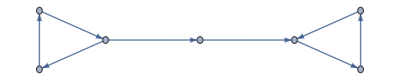

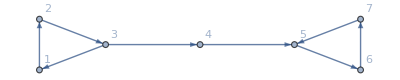

b[1->2]⊗(b[2->3]⊗(b[3->4]⊗(b[4->5]⊗(b[5->6]⊗b[6->7]))))

```mathematica
(* This is a simple test illustrating cycles being ignored at the beginning and end of a path to which they can not contribute without double-counting edges. The result is the same as if the edges 3->1 and 7->5 were simply not present -- which I believe, in disagreement with the EBSL paper, is how things ought to be, as described in the "Concerns about EBSL" section. *)
VertexAdd[g0,1];
VertexAdd[%,2];
VertexAdd[%,3];
VertexAdd[%,4];
VertexAdd[%,5];
VertexAdd[%,6];
VertexAdd[%,7];
EdgeAdd[%,1->2];
EdgeAdd[%,2->3];
EdgeAdd[%,3->1];
EdgeAdd[%,3->4];
EdgeAdd[%,4->5];
EdgeAdd[%,5->6];
EdgeAdd[%,6->7];
EdgeAdd[%,7->5];
cycleRemovalTest=%
DefaultGraphPlot[cycleRemovalTest]
AttenuatedFlowDefault[b,cycleRemovalTest,1,7]
```

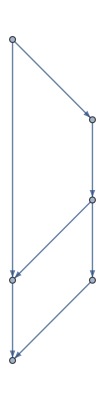

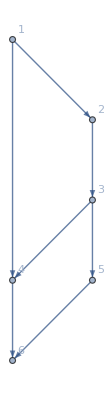

(((ef[1->4]⊕ef[1->2]⊗(ef[2->3]⊗ef[3->4]))⊗ef[4->6])⋁(ef[1->2]⊗(ef[2->3]⊗(ef[3->5]⊗ef[5->6]))⊕ef[1->4]⊗ef[4->6]))⋁(ef[1->2]⊗(ef[2->3]⊗(ef[3->4]⊗ef[4->6]⊕ef[3->5]⊗ef[5->6])))

```mathematica
(* This illustrates another shape in which AttenuatedFlow produces a join of different path removals: respectively, 3->5->6, 3->4, and 1->4. *)
VertexAdd[g0,1];
VertexAdd[%,2];
VertexAdd[%,3];
VertexAdd[%,4];
VertexAdd[%,5];
VertexAdd[%,6];
EdgeAdd[%,1->2];
EdgeAdd[%,2->3];
EdgeAdd[%,3->4];
EdgeAdd[%,1->4];
EdgeAdd[%,3->5];
EdgeAdd[%,4->6];
EdgeAdd[%,5->6];
repeatedMergeTest=%
DefaultGraphPlot[repeatedMergeTest]
AttenuatedFlowDefault[ef,repeatedMergeTest,1,6]
```

## Defining SPIL: Belief vectors + trust operators + intuitionistic propositional logic operators + induction over propagation graphs

Having defined the graph-theoretical component of SPIL -- “AttenuatedFlow” -- we now define the algebraic component, wherein we plug in the operators we have defined on belief vectors -- join, propagate, consensus, dot, contradot, not -- to AttenuatedFlow via its parameters.

Definitions

```mathematica
(* The edge function that we pass in to AttenuatedFlow defines the degree to which flow is attenuated when it passes along an edge.  In the case of an edge representing trust or belief, which must point from a user to (respectively) another user or a proposition,that degree is described by the belief vector that the user has assigned.  In the case of edges from propositions to propositions, there are "positive" edges which pass through belief unchanged and "negative" edges which apply "not" before passing belief through. We shall also use these values to describe chains (comprising multiple consecutive edges) from propositions to propositions. In that context, we will also define "zero" chains which pass through no belief at all -- that is, they turn incoming belief into Uncertain. Zero chains can arise when we chain a single input edge through a node type that requires more than one edge to produce any belief (such as dot or conradot), and also, in intuitionistic logic, two consecutive negative chains produce a zero chain, not a positive chain, because the first negation produces only disbelief, and the negation of pure disbelief is Uncertain. *)
SPILedgef[g_,e_]:=
(Assert[GraphHasEdge[g,e]];
Switch[EdgeType[g,SourceVertex[e],TargetVertex[e]],
"t",SPILbv[GetTrust[g,e]],
"b",SPILbv[GetBelief[g,e]],
"n",SPILneg,
"i2d",SPILpos,
"a2d",SPILpos,
"d2cq",SPILpos,
"i2cd",SPILpos,
"cq2cd",SPILpos,
"cd2a",SPILpos,
_,(Print["unknown SPIL edge/chain type"];Assert[False])
]
)
```

```mathematica
(* Tells us whether a given SPIL edge value has a belief vector representing trust/belief, as opposed to positive/negative/zero. *)
SPILisBV[SPILbv[_]]:=True
SPILisBV[SPILneg]:=False
SPILisBV[SPILpos]:=False
SPILisBV[SPILzero]:=False
SPILisBV[_]:=(Print["invalid argument to SPILisBV";Assert[False];False])
```

```mathematica
(* Tests for SPIL edge/chain value types. *)
SPILisPos[SPILpos]:=True
SPILisPos[_]:=False
SPILisNeg[SPILneg]:=True
SPILisNeg[_]:=False
SPILisZero[SPILzero]:=True
SPILisZero[_]:=False
```

```mathematica
(* Tests for properties of lists of SPIL edge/chain value types. *)
SPILallBV[l_]:=AllTrue[l,SPILisBV]
SPILhasBV[l_]:=AnyTrue[l,SPILisBV]
SPILallPos[l_]:=AllTrue[l,SPILisPos]
SPILallNeg[l_]:=AllTrue[l,SPILisNeg]
SPILallZero[l_]:=AllTrue[l,SPILisZero]
SPILhasPos[l_]:=AnyTrue[l,SPILisPos]
SPILhasNeg[l_]:=AnyTrue[l,SPILisNeg]
SPILhasZero[l_]:=AnyTrue[l,SPILisZero]
```

```mathematica
(* Return those edge values in a list which have associated belief vectors. *)
SPILselectBVs[l_]:=Select[l,SPILisBV]
```

```mathematica
(* This extracts the belief vector from an edge value that has a belief vector. *)
SPILextract[SPILbv[bv_]]:=bv
SPILextract[bv_]:=(Print["non-BV argument to SPILextract: "<>ToString[bv]];Assert[False])
```

```mathematica
(* This function returns the analogue of passing no belief from the given vertex: Uncertain from a user, or SPILzero from a proposition. *)
SPILnoBelief[g_,v_]:=If[VertexIsUser[g,v],SPILbv[Uncertain],SPILzero]
```

```mathematica
(* A utility function to zero out chains through or joins into dot or contradot nodes with only one incoming edge in the subgraph (since those node types require beliefs from two different edges to produce any outgoing belief). The first vertex parameter is the source, so it determines whether the zero value is Uncertain or SPILzero, and the second vertex parameter is the one that we test for being dot or contradot. *)
SPILclearUnmergedDot[g_,v_,w_,subg_,ov_]:=Module[{wt=VertexType[g,w],we=IncomingEdgesG[subg,w],lwe},
lwe=Length[we];
Assert[lwe≥1];
If[((wt=="dot")∨(wt=="contradot"))∧(Assert[lwe≤2];lwe==1),
SPILnoBelief[g,v],
ov
]
]
```

```mathematica
(* The SPIL chain function combines trust with trust or belief using propagate, combines trust or belief with negation using not, combines zero edges with anything to produce zero edges, and passes anything unchanged through positive edges. We must also zero out any chain through a dot or contradot node with only a single incoming edge. *)
SPILchainfNonDot[g_,v_,w_,subg_,x_,_,SPILzero]:=SPILnoBelief[g,v]
SPILchainfNonDot[g_,v_,w_,subg_,x_,SPILzero,_]:=SPILzero
SPILchainfNonDot[g_,v_,w_,subg_,x_,ovw_,SPILpos]:=ovw
SPILchainfNonDot[g_,v_,w_,subg_,x_,SPILpos,owx_]:=owx
SPILchainfNonDot[g_,v_,w_,subg_,x_,SPILbv[ovw_],SPILbv[owx_]]:=SPILbv[𝔓[{ovw,owx}]]
SPILchainfNonDot[g_,v_,w_,subg_,x_,SPILbv[ovw_],SPILneg]:=SPILbv[SuperDagger[ovw]]
(* It is impossible for a non-BV chain value, which can only connect between propositions, to be chained on the left with a BV chain value, which can only connect between users. *)
SPILchainfNonDot[g_,v_,w_,subg_,x_,SPILneg,SPILbv[owx_]]:=(Print["chaining prop value (SPILneg) with user value ("<>ToString[owx]<>"): "<>PathToString[{v,w,x}]];
Assert[False])
SPILchainfNonDot[g_,v_,w_,subg_,x_,SPILneg,SPILneg]:=SPILzero
SPILchainf[g_,v_,w_,subg_,x_,ovw_,owx_]:=
(SPILclearUnmergedDot[g,v,w,subg,SPILchainfNonDot[g,v,w,subg,x,ovw,owx]])
```

```mathematica
(* This routine combines proposition-to-proposition chain value types (those other than SPILbv), producing an output suitable to either join or merge. It may not be called on a list containing any SPILbv elements, or on an empty list. *)
SPILcombine[g_,v_,subgs_,w_,l_]:=
(Assert[¬VertexIsUser[g,v]];
Assert[l≠{}];
Assert[¬SPILhasBV[l]];
If[SPILhasNeg[l],
(* It would be a contradiction in the logic for a proposition to be able to imply both another proposition and its negation! *)
(Assert[¬SPILhasPos[l]];SPILneg),
If[SPILhasPos[l],
SPILpos,
(Assert[SPILallZero[l]];
SPILzero)
]
]
)
```

```mathematica
SPILjoinf[g_,v_,subgs_,w_,{}]:=(Print["empty join"];Assert[False])
SPILjoinf[g_,v_,subgs_,w_,{o_}]:=(Print["singleton join"];Assert[False])
SPILjoinf[g_,v_,subgs_,w_,l_]:=Module[{cl},
Assert[Length[subgs]==Length[l]];
cl=MapThread[(SPILclearUnmergedDot[g,v,w,#1,#2])&,{subgs,l}] ;
If[VertexIsUser[g,v],
(* For trust/belief vectors (originating with users), the SPIL join function is just 𝔍. *)
(Assert[SPILallBV[cl]];
SPILbv[𝔍[Map[SPILextract,cl]]]),
(SPILcombine[g,v,subgs,w,cl])
]
]
```

```mathematica
(* This function captures the commonality between the merge function for dot and that for contradot. *)
SPILmergeDotOrContra[g_,v_,subgs_,w_,bvs_,isDot_]:=Module[{inedges=IncomingEdgesG[g,w],ebvs},
Assert[Length[inedges]==2];
Assert[Length[bvs]==2];
Assert[Length[OutgoingEdgesG[g,w]]==1];
Assert[EdgeType[g,SourceVertex[inedges[[1]]],w]==If[isDot,"i2d","i2cd"]];
Assert[EdgeType[g,SourceVertex[inedges[[2]]],w]==If[isDot,"a2d","cq2cd"]];
If[¬SPILallBV[bvs],
(Assert[¬VertexIsUser[g,v]];
Assert[¬SPILhasBV[bvs]];
Assert[SPILhasZero[bvs]];
SPILzero),
(Assert[VertexIsUser[g,v]];
ebvs=Map[SPILextract,bvs];
If[GraphHasEdge[subgs[[1]],inedges[[1]]],
(Assert[¬GraphHasEdge[subgs[[1]],inedges[[2]]]];
Assert[¬GraphHasEdge[subgs[[2]],inedges[[1]]]];
Assert[GraphHasEdge[subgs[[2]],inedges[[2]]]];
SPILbv[If[isDot,𝔇[ebvs[[1]],ebvs[[2]]],ℭ𝔇[ebvs[[1]],ebvs[[2]]]]]),
(Assert[GraphHasEdge[subgs[[1]],inedges[[2]]]];
Assert[GraphHasEdge[subgs[[2]],inedges[[1]]]];
Assert[¬GraphHasEdge[subgs[[2]],inedges[[2]]]];
SPILbv[If[isDot,𝔇[ebvs[[2]],ebvs[[1]]],ℭ𝔇[ebvs[[2]],ebvs[[1]]]]])
])
]
]
```

```mathematica
(* The SPIL merge function uses the subgraphs provided by AttenuatedFlow to determine which belief vectors correspond with which edges when merging at dot and contradot nodes. Merges at other node types use consensus. *)
SPILmergef[g_,v_,subgs_,w_,bvs_]:=
(Assert[Length[subgs]==Length[bvs]];
Assert[Length[bvs]≥2];
Assert[Length[bvs]≤Length[OutgoingEdgesG[g,v]]];
Assert[Length[bvs]≤Length[IncomingEdgesG[g,w]]];
Switch[VertexType[g,w],
"user",SPILbv[ℭ[Map[SPILextract,bvs]]],
"prop",If[VertexIsUser[g,v],SPILbv[ℭ[Map[SPILextract,bvs]]],SPILcombine[g,v,subgs,w,bvs]],
"dot",SPILmergeDotOrContra[g,v,subgs,w,bvs,True],
"contradot",SPILmergeDotOrContra[g,v,subgs,w,bvs,False],
_,(Print["invalid edge type in SPILmergef"];Assert[False])
]
)
```

```mathematica
(* Use the SPIL edge, join, chain, and merge functions to produce the core SPIL formula for a user's trust in another user or belief in a proposition (or in the degree to which one proposition implies another). *) 
SPILf[g_,v_,w_]:=(AssertIsUser[g,v];
SPILextract[AttenuatedFlow[SPILbv[Proven],SPILbv[Uncertain],SPILjoinf,SPILedgef,SPILchainf,SPILmergef,g,v,w]])
```

```mathematica
(* Compute for given substitutions the explicit value of the SPIL formula. *)
SPILfEx[g_,v_,w_,subs_]:=EvalBelief[SPILf[g,v,w]/.subs]
```

```mathematica
(* Numeric (possibly approximate) value of the SPIL formula. *)
SPILfExN[g_,v_,w_,subs_]:=N[SPILfEx[g,v,w,subs]]
```

```mathematica
(* Check under what conditions some expression can be guaranteed to be equal to the value of the SPIL propagation formula for some graph and source and sink vertices. *)
CheckSPILSolution[g_,v_,w_,cs_,subs_,soln_]:=SimplifyBelief[(SPILf[g,v,w]==soln)/.subs,cs]
```

Tests and Examples

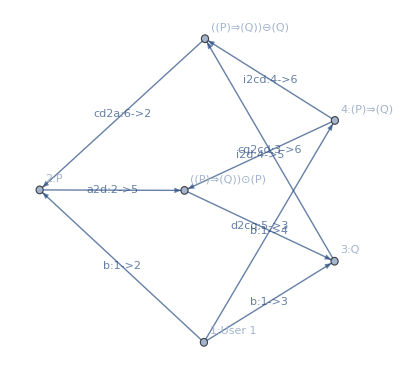

ef[1->2]⊕((ef[1->3]⊗ef[3->6]⊕ef[1->4]⊗ef[4->6])⋁((ef[1->3]⊕ef[1->4]⊗(ef[4->5]⊗ef[5->3]))⊗ef[3->6]))⋁(ef[1->4]⊗(ef[4->6]⊕(ef[4->5]⊗ef[5->3])⊗ef[3->6]))⊗ef[6->2]

p⊕(pq⊖q)

ef[1->3]⊕((ef[1->2]⊗ef[2->5]⊕ef[1->4]⊗ef[4->5])⋁((ef[1->2]⊕ef[1->4]⊗(ef[4->6]⊗ef[6->2]))⊗ef[2->5]))⋁(ef[1->4]⊗(ef[4->5]⊕(ef[4->6]⊗ef[6->2])⊗ef[2->5]))⊗ef[5->3]

q⊕pq⊙p

```mathematica
(* Here is a simple example of the effect of implication -- a foundation of reasoning -- on both belief (in the consequent) and disbelief (in the antecedent). *)
g1;
(* 2 *) AddAtomic[%,"P"];
AddBelief[%,1,2,p];
(* 3 *) AddAtomic[%,"Q"];
AddBelief[%,1,3,q];
(* 4-6 *) AddImplication[%,2,3];
implicationExample=AddBelief[%,1,4,pq]
AttenuatedFlowDefault[ef,implicationExample,1,2]
SPILf[implicationExample,1,2]
AttenuatedFlowDefault[ef,implicationExample,1,3]
SPILf[implicationExample,1,3]
```

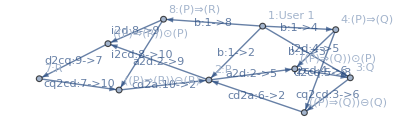

pr⊙(p⊕(pq⊖q))

```mathematica
(* Here we extend the previous example to show how disbelief, in this case disbelief which comes from contradot, suppresses the propagation of belief. *)
(* 7 *) AddAtomic[implicationExample,"R"];
(* 8-10 *) AddImplication[%,2,7];
contradotSuppressionExample=AddBelief[%,1,8,pr]
SPILf[contradotSuppressionExample,1,7]
```

```mathematica
(* Above we see that the belief propagated from P⇒R and P contains a contradot term. Here is an example of the numeric effect, where disbelief in Q is propagated back to P, and thus decreases belief in R. Note that it's not the lower belief in Q that decreases the belief in P; it's the increased disbelief. *)
SPILfExN[contradotSuppressionExample,1,7,{p->{8/10,1/10,1/10},q->{9/10,0,1/10},pq->{5/10,3/10,2/10},pr->{3/10,1/10,6/10}}]
SPILfExN[contradotSuppressionExample,1,7,{p->{8/10,1/10,1/10},q->{8/10,0,2/10},pq->{5/10,3/10,2/10},pr->{3/10,1/10,6/10}}]
bv2evp[%]
SPILfExN[contradotSuppressionExample,1,7,{p->{8/10,1/10,1/10},q->{7/10,2/10,1/10},pq->{5/10,3/10,2/10},pr->{3/10,1/10,6/10}}]
bv2evp[%]
```

{0.24,0.,0.76}

{0.24,0.,0.76}

{0.315789,0.}

{0.237363,0.,0.762637}

{0.311239,0.}

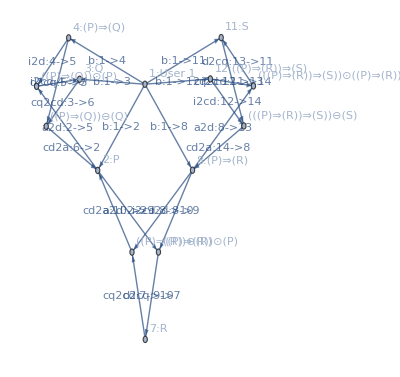

(pr⊕(prs⊖s))⊙(p⊕(pq⊖q))

```mathematica
(* With a further extension, we can illustrate contradot-induced suppression of propagation through the left side of the dot operator as well. *)
(* 11 *) AddAtomic[contradotSuppressionExample,"S"];
(* 12-14 *) AddImplication[%,8,11];
AddBelief[%,1,11,s];
contradotImplicationSuppressionExample=AddBelief[%,1,12,prs]
SPILf[contradotImplicationSuppressionExample,1,7]
```

```mathematica
(* Here we perform a similar numeric illustration to the previous one, where now it is disbelief in S which suppresses belief in P⇒R on the left side, and therefore suppresses the net belief in R resulting from the dot. *)
SPILfExN[contradotImplicationSuppressionExample,1,7,{p->{8/10,1/10,1/10},q->{9/10,0,1/10},pq->{5/10,3/10,2/10},pr->{3/10,1/10,6/10},prs->{6/10,2/10,2/10},s->{7/10,0,3/10}}]
SPILfExN[contradotImplicationSuppressionExample,1,7,{p->{8/10,1/10,1/10},q->{9/10,0,1/10},pq->{5/10,3/10,2/10},pr->{3/10,1/10,6/10},prs->{6/10,2/10,2/10},s->{6/10,0,4/10}}]
bv2evp[%]
SPILfExN[contradotImplicationSuppressionExample,1,7,{p->{8/10,1/10,1/10},q->{9/10,0,1/10},pq->{5/10,3/10,2/10},pr->{3/10,1/10,6/10},prs->{6/10,2/10,2/10},s->{6/10,2/10,2/10}}]
bv2evp[%]
```

{0.24,0.,0.76}

{0.24,0.,0.76}

{0.315789,0.}

{0.221849,0.,0.778151}

{0.285097,0.}

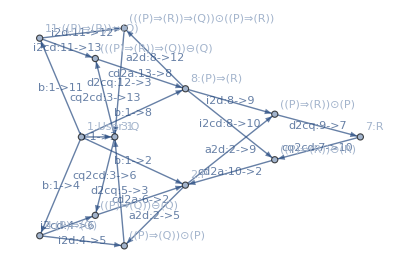

(pr⊕(prq⊖q))⊙p⋁pr⊙(p⊕(pq⊖q))

```mathematica
(* Here we test a strangely-shaped graph derived from contradotSuppressionExample in which the contradot of Q appears on both the left and the right side of the dot. *)
(* 11-13 *) AddImplication[contradotSuppressionExample,8,3];
contradotOddSuppressionExample=AddBelief[%,1,11,prq]
SPILf[contradotOddSuppressionExample,1,7]
```

```mathematica
(* Here's the attenuated flow from which the above SPIL formula is (in effect) derived. *)
AttenuatedFlowDefault[ef,contradotOddSuppressionExample,1,7]
```

((((((ef[1->2]⊗ef[2->9]⊕(ef[1->8]⊕((ef[1->11]⊗(ef[11->13]⊕(ef[11->12]⊗ef[12->3])⊗ef[3->13]))⋁((ef[1->3]⊕ef[1->4]⊗(ef[4->5]⊗ef[5->3]))⊗ef[3->13]⊕ef[1->11]⊗ef[11->13]))⋁(((ef[1->3]⊕ef[1->4]⊗(ef[4->5]⊗ef[5->3]))⊕ef[1->11]⊗(ef[11->12]⊗ef[12->3]))⊗ef[3->13])⊗ef[13->8])⊗ef[8->9])⋁((ef[1->2]⊕((ef[1->4]⊗(ef[4->6]⊕(ef[4->5]⊗ef[5->3])⊗ef[3->6]))⋁((ef[1->3]⊕ef[1->11]⊗(ef[11->12]⊗ef[12->3]))⊗ef[3->6]⊕ef[1->4]⊗ef[4->6]))⋁(((ef[1->3]⊕ef[1->4]⊗(ef[4->5]⊗ef[5->3]))⊕ef[1->11]⊗(ef[11->12]⊗ef[12->3]))⊗ef[3->6])⊗ef[6->2])⊗ef[2->9]⊕ef[1->8]⊗ef[8->9]))⋁((ef[1->2]⊕((ef[1->3]⊗ef[3->6]⊕ef[1->4]⊗ef[4->6])⋁((ef[1->3]⊕ef[1->4]⊗(ef[4->5]⊗ef[5->3]))⊗ef[3->6]))⋁(ef[1->4]⊗(ef[4->6]⊕(ef[4->5]⊗ef[5->3])⊗ef[3->6]))⊗ef[6->2])⊗ef[2->9]⊕(ef[1->8]⊕ef[1->11]⊗(ef[11->13]⊗ef[13->8]))⊗ef[8->9]))⋁((ef[1->2]⊕ef[1->4]⊗(ef[4->6]⊗ef[6->2]))⊗ef[2->9]⊕(ef[1->8]⊕((ef[1->3]⊗ef[3->13]⊕ef[1->11]⊗ef[11->13])⋁((ef[1->3]⊕ef[1->11]⊗(ef[11->12]⊗ef[12->3]))⊗ef[3->13]))⋁(ef[1->11]⊗(ef[11->13]⊕(ef[11->12]⊗ef[12->3])⊗ef[3->13]))⊗ef[13->8])⊗ef[8->9]))⋁((ef[1->8]⊕((ef[1->11]⊗(ef[11->13]⊕(ef[11->12]⊗ef[12->3])⊗ef[3->13]))⋁((ef[1->3]⊕ef[1->4]⊗(ef[4->5]⊗ef[5->3]))⊗ef[3->13]⊕ef[1->11]⊗ef[11->13]))⋁(((ef[1->3]⊕ef[1->4]⊗(ef[4->5]⊗ef[5->3]))⊕ef[1->11]⊗(ef[11->12]⊗ef[12->3]))⊗ef[3->13])⊗ef[13->8])⊗(ef[8->9]⊕(ef[8->10]⊗ef[10->2])⊗ef[2->9])))⋁((ef[1->8]⊕((ef[1->11]⊗(ef[11->13]⊕(ef[11->12]⊗ef[12->3])⊗ef[3->13]))⋁((ef[1->3]⊕((ef[1->2]⊗ef[2->5]⊕ef[1->4]⊗ef[4->5])⋁((ef[1->2]⊕ef[1->4]⊗(ef[4->6]⊗ef[6->2]))⊗ef[2->5]))⋁(ef[1->4]⊗(ef[4->5]⊕(ef[4->6]⊗ef[6->2])⊗ef[2->5]))⊗ef[5->3])⊗ef[3->13]⊕ef[1->11]⊗ef[11->13]))⋁(((ef[1->3]⊕((ef[1->2]⊗ef[2->5]⊕ef[1->4]⊗ef[4->5])⋁((ef[1->2]⊕ef[1->4]⊗(ef[4->6]⊗ef[6->2]))⊗ef[2->5]))⋁(ef[1->4]⊗(ef[4->5]⊕(ef[4->6]⊗ef[6->2])⊗ef[2->5]))⊗ef[5->3])⊕ef[1->11]⊗(ef[11->12]⊗ef[12->3]))⊗ef[3->13])⊗ef[13->8])⊗ef[8->9]))⋁((((((ef[1->2]⊕(ef[1->8]⊕ef[1->11]⊗(ef[11->13]⊗ef[13->8]))⊗((ef[8->12]⊗ef[12->3])⊗(ef[3->6]⊗ef[6->2])⊕ef[8->10]⊗ef[10->2]))⋁(ef[1->2]⊕(ef[1->8]⊕((ef[1->11]⊗(ef[11->13]⊕(ef[11->12]⊗ef[12->3])⊗ef[3->13]))⋁((ef[1->3]⊕ef[1->4]⊗(ef[4->5]⊗ef[5->3]))⊗ef[3->13]⊕ef[1->11]⊗ef[11->13]))⋁(((ef[1->3]⊕ef[1->4]⊗(ef[4->5]⊗ef[5->3]))⊕ef[1->11]⊗(ef[11->12]⊗ef[12->3]))⊗ef[3->13])⊗ef[13->8])⊗(ef[8->10]⊗ef[10->2])))⋁((ef[1->2]⊕((ef[1->4]⊗(ef[4->6]⊕(ef[4->5]⊗ef[5->3])⊗ef[3->6]))⋁((ef[1->3]⊕ef[1->11]⊗(ef[11->12]⊗ef[12->3]))⊗ef[3->6]⊕ef[1->4]⊗ef[4->6]))⋁(((ef[1->3]⊕ef[1->4]⊗(ef[4->5]⊗ef[5->3]))⊕ef[1->11]⊗(ef[11->12]⊗ef[12->3]))⊗ef[3->6])⊗ef[6->2])⊕ef[1->8]⊗(ef[8->10]⊗ef[10->2])))⋁((ef[1->2]⊕((ef[1->3]⊗ef[3->6]⊕ef[1->4]⊗ef[4->6])⋁((ef[1->3]⊕ef[1->4]⊗(ef[4->5]⊗ef[5->3]))⊗ef[3->6]))⋁(ef[1->4]⊗(ef[4->6]⊕(ef[4->5]⊗ef[5->3])⊗ef[3->6]))⊗ef[6->2])⊕(ef[1->8]⊕ef[1->11]⊗(ef[11->13]⊗ef[13->8]))⊗(ef[8->10]⊗ef[10->2])))⋁((ef[1->2]⊕ef[1->4]⊗(ef[4->6]⊗ef[6->2]))⊕(ef[1->8]⊕((ef[1->3]⊗ef[3->13]⊕ef[1->11]⊗ef[11->13])⋁((ef[1->3]⊕ef[1->11]⊗(ef[11->12]⊗ef[12->3]))⊗ef[3->13]))⋁(ef[1->11]⊗(ef[11->13]⊕(ef[11->12]⊗ef[12->3])⊗ef[3->13]))⊗ef[13->8])⊗(ef[8->10]⊗ef[10->2])))⋁(ef[1->2]⊕((ef[1->4]⊗(ef[4->6]⊕(ef[4->5]⊗ef[5->3])⊗ef[3->6]))⋁((ef[1->3]⊕((ef[1->8]⊗ef[8->12]⊕ef[1->11]⊗ef[11->12])⋁((ef[1->8]⊕ef[1->11]⊗(ef[11->13]⊗ef[13->8]))⊗ef[8->12]))⋁(ef[1->11]⊗(ef[11->12]⊕(ef[11->13]⊗ef[13->8])⊗ef[8->12]))⊗ef[12->3])⊗ef[3->6]⊕ef[1->4]⊗ef[4->6]))⋁(((ef[1->3]⊕ef[1->4]⊗(ef[4->5]⊗ef[5->3]))⊕((ef[1->8]⊗ef[8->12]⊕ef[1->11]⊗ef[11->12])⋁((ef[1->8]⊕ef[1->11]⊗(ef[11->13]⊗ef[13->8]))⊗ef[8->12]))⋁(ef[1->11]⊗(ef[11->12]⊕(ef[11->13]⊗ef[13->8])⊗ef[8->12]))⊗ef[12->3])⊗ef[3->6])⊗ef[6->2])⊗ef[2->9])⊗ef[9->7]

```mathematica
(* Experiment with ConnectedComponents as a possible aid to optimizing MaximalPartitionableEdgeSubsets. *)
ConnectedComponents[RestrictEdges[contradotOddSuppressionExample,1,7]]
```

{{7},{9},{2,3,5,6,8,10,12,13},{4},{11},{1}}

{3->13,2->5,5->3,13->8,8->10,10->2,3->6,6->2,8->12,12->3}

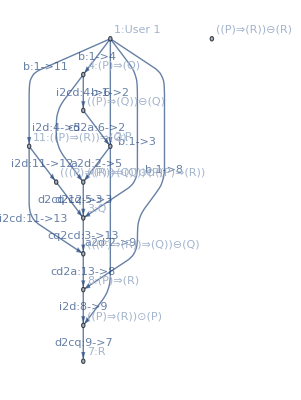
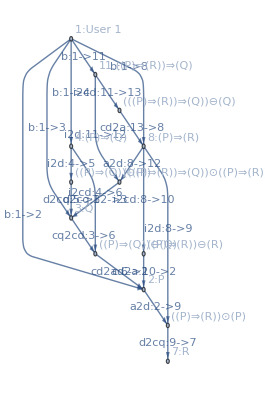
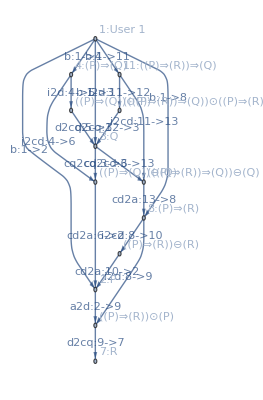

```mathematica
(* Examine where the cycles are in the "contradotOddSuppressionExample" graph. *)
DeleteDuplicates[Catenate[FindAllCycleRemovalEdgeSets[RestrictEdges[contradotOddSuppressionExample,1,7]]]]
FindAcyclicSubSTGraphs[contradotOddSuppressionExample,1,7]
```

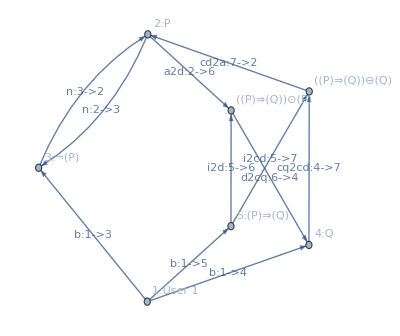

c⊕b⊙a^†

```mathematica
(* Here is another simple example, in this case including a negation. *)
g1;
AddAtomic[%,"P"];
AddNegation[%,2];
AddBelief[%,1,3,a];
AddAtomic[%,"Q"];
AddImplication[%,2,4];
AddBelief[%,1,5,b];
AddBelief[%,1,4,c];
smallTest=%
SPILf[smallTest,1,4]
```

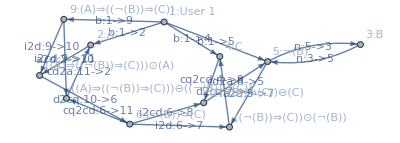

ef[1->4]⊕((ef[1->5]⊗ef[5->7]⊕(((ef[1->2]⊗ef[2->10]⊕ef[1->9]⊗ef[9->10])⋁((ef[1->2]⊕ef[1->9]⊗(ef[9->11]⊗ef[11->2]))⊗ef[2->10]))⋁(ef[1->9]⊗(ef[9->10]⊕(ef[9->11]⊗ef[11->2])⊗ef[2->10]))⊗ef[10->6])⊗ef[6->7])⋁((ef[1->5]⊕(((ef[1->2]⊗ef[2->10]⊕ef[1->9]⊗ef[9->10])⋁((ef[1->2]⊕ef[1->9]⊗(ef[9->11]⊗ef[11->2]))⊗ef[2->10]))⋁(ef[1->9]⊗(ef[9->10]⊕(ef[9->11]⊗ef[11->2])⊗ef[2->10]))⊗ef[10->6])⊗(ef[6->8]⊗ef[8->5]))⊗ef[5->7]))⋁((((ef[1->2]⊗ef[2->10]⊕ef[1->9]⊗ef[9->10])⋁((ef[1->2]⊕ef[1->9]⊗(ef[9->11]⊗ef[11->2]))⊗ef[2->10]))⋁(ef[1->9]⊗(ef[9->10]⊕(ef[9->11]⊗ef[11->2])⊗ef[2->10]))⊗ef[10->6])⊗(ef[6->7]⊕(ef[6->8]⊗ef[8->5])⊗ef[5->7]))⊗ef[7->4]

c⊕(v⊙a)⊙nb

```mathematica
(* I wrote the following proposed real-world example of the use of a logic that extended EBSL with reasoning (which eventually became SPIL) in an email:

I might be a policymaker who has an upcoming vote on a proposition C
which would tighten some vehicle emissions regulations. I might have
some constituency with a strong philosophical preference for or
against the proposition, which gives me some belief vector 𝒸; I might
have some contacts in climatology through whom I can use EBSL [now SPIL] to
obtain a belief vector 𝒶 in the proposition A that "passing this bill
would cut vehicle emissions by at least 25% in 5 years"; I might have
some contacts in economics through whom I can use EBSL [SPIL] to obtain a
belief vector 𝓃𝒷 in the proposition ¬B, where B is the proposition that "passing this bill would
increase vehicle prices by over 10%" (so ¬B is the proposition that "passing this bill would _not_ increase vehicle prices by over 10%", i.e. "passing this bill would increase vehicle prices by 10% or less or not at all, or even decrease them"); and I might myself construct a
belief vector 𝓋 in the proposition that "if it would cut emissions by
at least 25% in 5 years and wouldn't increase vehicle prices by more
than 10%, then I should vote for this bill". Now I have disparate information from constituents,climatologists, and economists, as well as my own sense of what constitutes a
worthwhile tradeoff, and all of those pieces of information carry
uncertainties, and some may favor my voting for the proposition while
others disfavor it. How am I to make my decision? I posit that the [SPIL] formula [below] gives me a mathematical way of
quantifying the degree to which I should favor voting for the
proposition (and my current level of uncertainty).

Here is a formalization of that example in Mathematica. *)
g1; (* 1=user (policymaker) *)
 (* 2 *) AddAtomic[%,"A"];
AddBelief[%,1,2,a];
 (* 3 *) AddAtomic[%,"B"];
 (* 4 *) AddAtomic[%,"C"];
AddBelief[%,1,4,c];
 (* 5=¬B *) AddNegation[%,3];
AddBelief[%,1,5,nb];
(* 6="¬B⇒C" *) AddImplication[%,5,4];
(* 9="A∧¬B⇒C" *) AddImplication[%,2,6];
emailExample=AddBelief[%,1,9,v]
AttenuatedFlowDefault[ef,emailExample,1,4]
SPILf[emailExample,1,4]
```

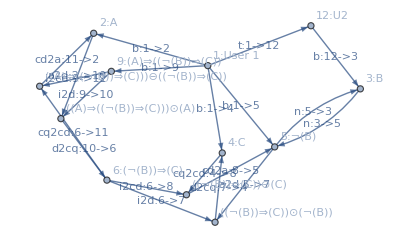

c⊕(v⊙a)⊙(nb⊕(t⊗b)^†)

```mathematica
(* Now imagine extending this example so that in addition to the belief vector 𝓃𝒷 obtained from an economist in the proposition ¬B, I also know and trust an automotive engineer who gives me a belief vector 𝒷 in the proposition B, i.e. the proposition that the bill _would_ increase vehicle prices by over 10%. Here is what happens when I take that into account. To make the example more interesting, in this case I shall explicitly express that this belief vector is not the result of my direct belief but of my trust in some other user who holds that belief. *)
(* 12=automotive engineer *)  AddUser[emailExample,"U2"];
(* my trust in the automotive engineer *) AddTrust[%,1,12,t];
extendedEmailExample=AddBelief[%,12,3,b]
SPILf[extendedEmailExample,1,4]
```

```mathematica
(* Note what has happened above. The formula is similar, but the "nb" term has been extended to "nb⊕(t⊗b)^†". This reflects that my belief in the proposition ¬B, formerly just "nb", has been combined with the belief that I inherited about B (not directly ¬B) from the automotive engineer. The "propagate" operator ("⊗") represents the inheritance, and the "not" operator ("†") around "t⊗b" represents that I got information about B rather than ¬B directly. The "not" operator produces only disbelief, so my belief in ¬B is being combined with some disbelief in it resulting from belief in B. The disbelief will have the effect of suppressing some of my belief in B, and thus (in this case) reducing my overall confidence that I should vote for the proposition (as expected, since I have received information that it might have consequences which I would consider to disfavor voting for it).

The example of the above formula might be a good place to mention that such a system is likely to work best when people express their reasons for beliefs in propositions as explicitly as possible (as in my trust in the automotive engineer being the explicit source of my belief vector 𝒷, as opposed to the way that I expressed direct trust in propositions about climate and economics even though I actually derived those opinions from trust in domain experts), in particular through trust when they don't have first-hand knowledge. For example, suppose that the New York Times publishes a story stating that event X has occurred. Many people read the New York Times and might consider it generally very reliable. They might therefore start expressing beliefs that X occurred after reading the article. But if a user's knowledge of event X's having occurred comes only from having read that article (which will most likely be the common case by a huge majority), then it would be better if users refrained from expressing belief in X and rather expressed trust in the New York Times, which in turn would express direct belief in X's having occurred based on its first-hand investigation. One way to see this is that if the Times later discovered that they were actually probably wrong in this case and event X had probably not occurred, then their reducing their belief that X had occurred would automatically result in their readers' beliefs being updated. Another way of seeing the superiority of inheriting indirect belief from trust in the Times is that if one user trusts many other readers of the Times, they would, if those users expressed direct beliefs in propositions which they had derived only from reading the Times, inherit a _consensus_ of beliefs -- even though those beliefs were not independent, all having been derived from a single article in the Times -- and therefore a very strong belief, even if the Times had only been moderately confident in its original story, and had expressed caution in the text and a correspondingly moderate belief in their SPIL belief vector.

Having said that, it does not mean that SPIL is forever doomed to be fragile in such cases. In particular, this is one of, I suspect, many examples in which an extension of SPIL to include predicate logic would allow for robustness against this case and similar ones. A user might, in the presence of predicate logic, choose to express that they trust a number of users, but that they do _not_ trust those users' beliefs about any topics about which the New York Times has expressed belief -- instead, they trust _only_ the Times (or the Times and some other sufficiently reliable media), on the presumption that their everyday friends, when they express beliefs that the Times has already expressed, are not actually expressing that they have first-hand knowledge, but are (lazily) repeating something that they read in the Times.

A logician might make such a provision on their own initiative, but to encourage a broad population of users to make their beliefs robust in that sense (and others), we would probably want to encourage building that sort of expression through education and defaults in the UI. *)
```

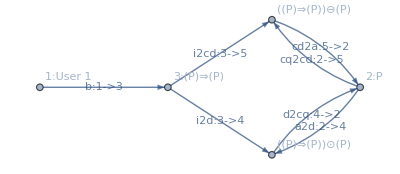

{0,0,1}

```mathematica
(* As the first in a series of sanity checks for some cases of strange user behavior, confirm that expressing a belief in the tautologous statement P⇒P does not have any effect on the belief in P. *)
g1;
AddAtomic[%,"P"];
AddImplication[%,2,2];
tautologyExample=AddBelief[%,1,3,b]
SPILf[tautologyExample,1,2]
```

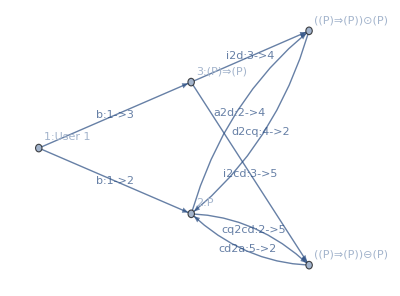

p

b

```mathematica
(* Extend the tautology example by adding a belief in the antecedent/consequent. The belief 𝒷 in the tautology P⇒P still has no effect on the belief in P (which in this case is just 𝓅). *)
extendedTautology=AddBelief[tautologyExample,1,2,p]
SPILf[extendedTautology,1,2]
SPILf[extendedTautology,1,3]
```

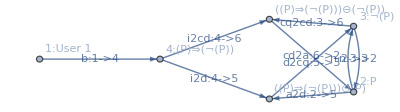

{0,0,1}

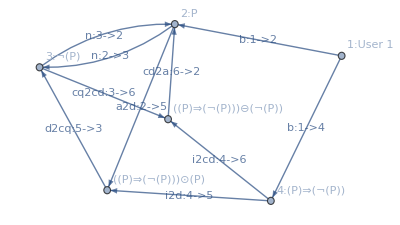

p

```mathematica
(* Perform a similar sanity check with respect to belief in a contradiction, P⇒¬P. Again the belief in the contradiction has no effect on the belief in P itself. *)
g1;
AddAtomic[%,"P"];
AddNegation[%,2];
AddImplication[%,2,3];
contradictionExample=AddBelief[%,1,4,b]
SPILf[contradictionExample,1,2]
extendedContradictionExample=AddBelief[contradictionExample,1,2,p]
SPILf[extendedContradictionExample,1,2]
```

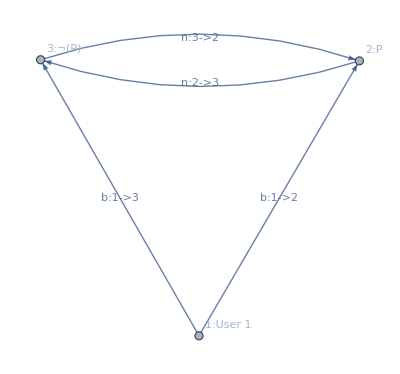

bp⊕bn^†

bn⊕bp^†

```mathematica
(* Here is an example in which we express some degree of belief in both a proposition and its negation. *)
g1;
AddAtomic[%,"P"];
AddNegation[%,2];
AddBelief[%,1,2,bp];
propNegExample=AddBelief[%,1,3,bn]
SPILf[propNegExample,1,2]
SPILf[propNegExample,1,3]
```

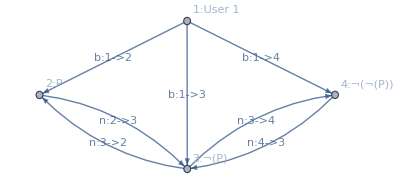

b⊕(bn⊕bnn^†)^†

(bn⊕b^†)⊕bnn^†

bnn⊕(bn⊕b^†)^†

```mathematica
(* Here we test propagating belief from double negation through negation to the original proposition. *)
g1;
AddAtomic[%,"P"];
AddBelief[%,1,2,b];
AddNegation[%,2];
AddBelief[%,1,3,bn];
AddNegation[%,3];
doubleNegationExample=AddBelief[%,1,4,bnn]
SPILf[doubleNegationExample,1,2]
SPILf[doubleNegationExample,1,3]
SPILf[doubleNegationExample,1,4]
```

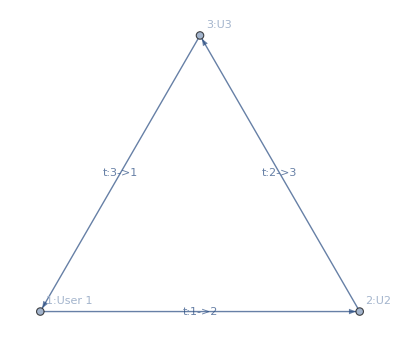

A12⊗A23

A23⊗A31

```mathematica
(* Here we very simply illustrate trust not propagating through a cycle. *)
g1;
AddUser[%,"U2"];
AddUser[%,"U3"];
AddTrust[%,1,2,A12];
AddTrust[%,2,3,A23];
AddTrust[%,3,1,A31];
simpleCycle=%
SPILf[simpleCycle,1,3]
SPILf[simpleCycle,2,1]
```

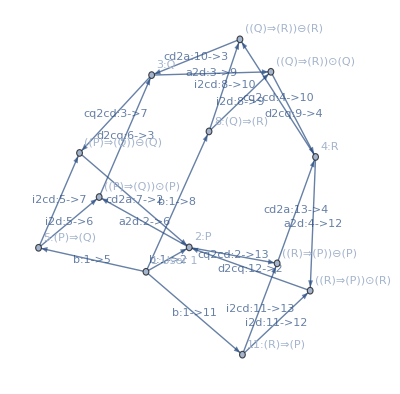

vqr⊙(vpq⊙vp)⋁(vrp⊖vp)

```mathematica
(* Here we illustrate cycles of implications rather than trusts -- that is, cycles among propositions rather than among users. Note how the final belief in R derives from a join of two contributions: one contribution from Q⇒R, P⇒Q, and P, and one contribution from R⇒P and P. The former is the belief, deriving from dot, and the latter is the disbelief, deriving from contradot. (Because there is no overlap (one is pure belief and one is pure disbelief), the join gives the same result as consensus would.) *)
g1;
(* 2 *) AddAtomic[%,"P"];
(* 3 *) AddAtomic[%,"Q"];
(* 4 *) AddAtomic[%,"R"];
(* 5: P => Q *) AddImplication[%,2,3];
(* 6: Q => R *) AddImplication[%,3,4];
(* 7: R => P *) AddImplication[%,4,2];
AddBelief[%,1,2,vp];
AddBelief[%,1,5,vpq];
AddBelief[%,1,8,vqr];
AddBelief[%,1,11,vrp];
cycleTest=%
cycleTestFormula=SPILf[cycleTest,1,4]
```

```mathematica
(* Here we illustrate the statement above that the join combines pure belief from dot and pure disbelief from contradot. *)
cycleTestNumericSubs:={vp->{5/10,1/10,4/10},vpq->{3/10,6/10,1/10},vqr->{2/10,1/10,7/10},vrp->{4/10,4/10,2/10}}
EvalBelief[(vqr⊙(vpq⊙vp))/.cycleTestNumericSubs]
bv2evp[%]
EvalBelief[(vrp⊖vp)/.cycleTestNumericSubs]
bv2evp[%]
EvalBelief[%%%%⋁%%]
SPILfEx[cycleTest,1,4,cycleTestNumericSubs]
Simplify[%%==%]
N[%%]
bv2evp[%%%]
```

{3/100,0,97/100}

{3/97,0}

{0,1/25,24/25}

{0,1/24}

{72/2497,97/2497,2328/2497}

{72/2497,97/2497,2328/2497}

True

{0.0288346,0.0388466,0.932319}

{3/97,1/24}

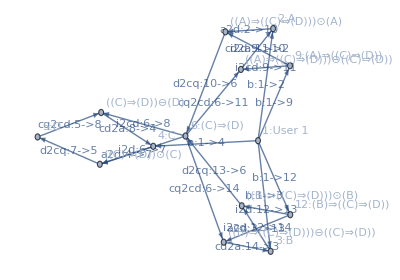

(acd⊙a⊕bcd⊙b)⊙c

```mathematica
(* Test propagating belief through a vertex with multiple sources of it. Note in this case how the two ways of deriving belief in C⇒D are combined by consensus before that whole expression is passed into the dot operator (along with C). *)
g1;
AddAtomic[%,"A"];
AddBelief[%,1,2,a];
AddAtomic[%,"B"];
AddBelief[%,1,3,b];
AddAtomic[%,"C"];
AddBelief[%,1,4,c];
AddAtomic[%,"D"];
AddImplication[%,4,5];
AddImplication[%,2,6];
AddBelief[%,1,9,acd];
AddImplication[%,3,6];
AddBelief[%,1,12,bcd];
multipathExample=%
SPILf[multipathExample,1,5]
```

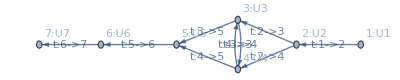

A12⊗((((((A24⊕A23⊗A34)⊗A45)⋁(A23⊗A35⊕A24⊗A45))⋁((A23⊕A24⊗A43)⊗A35))⋁(A23⊗(A35⊕A34⊗A45)))⋁(A24⊗(A45⊕A43⊗A35))⊗(A56⊗A67))

```mathematica
(* This example illustrates how a join of all possible cycle-free paths, as induced by a cycle, may be embedded within a larger expression, such as in a chain of propagations; it is not necessary to do the join over the entire graph. *)
g0;
AddUser[%,"U1"];
AddUser[%,"U2"];
AddUser[%,"U3"];
AddUser[%,"U4"];
AddUser[%,"U5"];
AddUser[%,"U6"];
AddUser[%,"U7"];
AddTrust[%,1,2,A12];
AddTrust[%,2,3,A23];
AddTrust[%,2,4,A24];
AddTrust[%,3,4,A34];
AddTrust[%,4,3,A43];
AddTrust[%,3,5,A35];
AddTrust[%,4,5,A45];
AddTrust[%,5,6,A56];
AddTrust[%,6,7,A67];
embeddedCycleExample=%
SPILf[embeddedCycleExample,1,7]
```

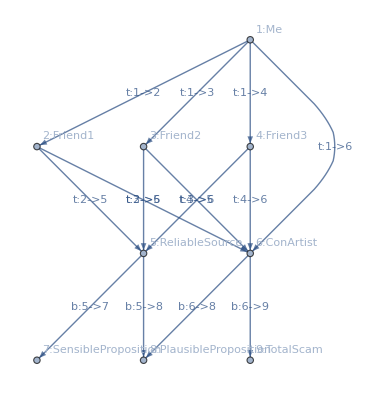

((f1⊗r1⊕f2⊗r2)⊕f3⊗r3)⊗rs

((((((((((skepticism⊕f1⊗c1)⊕f2⊗c2)⊕f3⊗c3)⊗cp)⋁(((f1⊗r1⊕f2⊗r2)⊕f3⊗r3)⊗rp⊕skepticism⊗cp))⋁((f1⊗r1⊕f2⊗r2)⊗rp⊕(skepticism⊕f3⊗c3)⊗cp))⋁(f1⊗(r1⊗rp)⊕((skepticism⊕f2⊗c2)⊕f3⊗c3)⊗cp))⋁((f1⊗r1⊕f3⊗r3)⊗rp⊕(skepticism⊕f2⊗c2)⊗cp))⋁(f2⊗(r2⊗rp)⊕((skepticism⊕f1⊗c1)⊕f3⊗c3)⊗cp))⋁((f2⊗r2⊕f3⊗r3)⊗rp⊕(skepticism⊕f1⊗c1)⊗cp))⋁(f3⊗(r3⊗rp)⊕((skepticism⊕f1⊗c1)⊕f2⊗c2)⊗cp)

(((skepticism⊕f1⊗c1)⊕f2⊗c2)⊕f3⊗c3)⊗ct

((f1⊗r1⊕f2⊗r2)⊕f3⊗r3)⊗rs

((((((((f1⊗r1⊕f2⊗r2)⊕f3⊗r3)⊗rp)⋁((f1⊗r1⊕f2⊗r2)⊗rp))⋁(f1⊗(r1⊗rp)))⋁((f1⊗r1⊕f3⊗r3)⊗rp))⋁(f2⊗(r2⊗rp)))⋁((f2⊗r2⊕f3⊗r3)⊗rp))⋁(f3⊗(r3⊗rp))

{0,0,1}

```mathematica
(* Here we examine how we can specify direct disbelief in a user to reduce the effect that that user might have on our belief in propositions deriving from other users that we trust trusting that user. See the discussion in the "Future Work" section of the "con artist" scenario and the "block user" use of Unsupported. The SPIL formulas for this graph show that as our "skepticism" (for the "ConArtist") approaches Unsupportable, our belief in the "TotalScam" proposition approaches Unsupportable⊗x, which is completely Uncertain, while the same happens to the right-hand side of the join for the PlausibleProposition, which leaves us with only the left-hand side -- the part influenced by ReliableSource, without any influence from ConArtist. *)
g0;
(* 1 *) AddUser[%,"Me"];
(* 2 *) AddUser[%,"Friend1"];
(* 3 *) AddUser[%,"Friend2"];
(* 4 *) AddUser[%,"Friend3"];
(* 5 *) AddUser[%,"ReliableSource"];
(* 6 *) AddUser[%,"ConArtist"];
(* 7 *) AddAtomic[%,"SensibleProposition"];
(* 8 *) AddAtomic[%,"PlausibleProposition"];
(* 9 *) AddAtomic[%,"TotalScam"];
AddTrust[%,1,2,f1];
AddTrust[%,1,3,f2];
AddTrust[%,1,4,f3];
AddTrust[%,1,6,skepticism];
AddTrust[%,2,5,r1];
AddTrust[%,3,5,r2];
AddTrust[%,4,5,r3];
AddTrust[%,2,6,c1];
AddTrust[%,3,6,c2];
AddTrust[%,4,6,c3];
AddBelief[%,5,7,rs];
AddBelief[%,5,8,rp];
AddBelief[%,6,8,cp];
AddBelief[%,6,9,ct];
blockUserExample=%
SPILf[blockUserExample,1,7]
SPILf[blockUserExample,1,8]
SPILf[blockUserExample,1,9]
blockUserCompletely:=AddTrust[EdgeDelete[blockUserExample,1->6],1,6,Unsupportable]
SPILf[blockUserCompletely,1,7]
SPILf[blockUserCompletely,1,8]
SPILf[blockUserCompletely,1,9]
```

```mathematica
(* Illustrate how SPIL's "block user" can be partial; if we express some but not complete distrust in ConArtist, then we reduce but do not eliminate the effect of ConArtist's beliefs on ours. *)
SPILfExN[blockUserExample,1,9,{f1->{8/10,1/10,1/10},f2->{8/10,1/10,1/10},f3->{8/10,1/10,1/10},
c1->{8/10,1/10,1/10},c2->{8/10,1/10,1/10},c3->{8/10,1/10,1/10},
ct->{8/10,1/10,1/10},skepticism->Uncertain}]
SPILfExN[blockUserExample,1,9,{f1->{8/10,1/10,1/10},f2->{8/10,1/10,1/10},f3->{8/10,1/10,1/10},
c1->{8/10,1/10,1/10},c2->{8/10,1/10,1/10},c3->{8/10,1/10,1/10},
ct->{8/10,1/10,1/10},skepticism->{0,1/10,9/10}}]
SPILfExN[blockUserExample,1,9,{f1->{8/10,1/10,1/10},f2->{8/10,1/10,1/10},f3->{8/10,1/10,1/10},
c1->{8/10,1/10,1/10},c2->{8/10,1/10,1/10},c3->{8/10,1/10,1/10},
ct->{8/10,1/10,1/10},skepticism->{0,9/10,1/10}}]
SPILfExN[blockUserExample,1,9,{f1->{8/10,1/10,1/10},f2->{8/10,1/10,1/10},f3->{8/10,1/10,1/10},
c1->{8/10,1/10,1/10},c2->{8/10,1/10,1/10},c3->{8/10,1/10,1/10},
ct->{8/10,1/10,1/10},skepticism->Unsupportable}]
```

{0.629508,0.0786885,0.291803}

{0.621583,0.0776978,0.300719}

{0.309677,0.0387097,0.651613}

{0.,0.,1.}

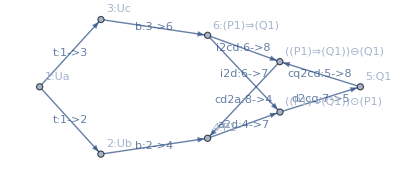

(A⊗TPQ)⊙(A⊗TP)

```mathematica
(* Here we begin an illustration that our trust in a consequent proposition can depend on the degree of dependence or independence of the trust in the implication and antecedent. First, we examine a case where we derive our belief in a proposition via two different users, one of whom believes in the implication and one of whom believes in the antecedent (though we happen to have the same degree of trust in each user). *)
g0;
AddUser[%,"Ua"];
AddUser[%,"Ub"];
AddUser[%,"Uc"];
AddAtomic[%,"P1"];
AddAtomic[%,"Q1"];
AddImplication[%,4,5];
AddTrust[%,1,2,A];
AddTrust[%,1,3,A];
AddBelief[%,2,4,TP];
AddBelief[%,3,6,TPQ];
independentDot=%
independentDotSPIL=SPILf[independentDot,1,5]
```

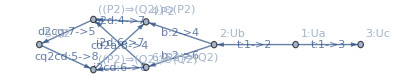

A⊗TPQ⊙TP

```mathematica
(* Now we examine a case where our belief in the proposition comes from a single user who believes in both the implication and the antecedent. We imagine that we have the same trust in this user as we did in each previous example, and that this user's beliefs in the implication and antecedent respectively equal those of the users who believed in those propositions in the previous example. *)
g0;
AddUser[%,"Ua"];
AddUser[%,"Ub"];
AddUser[%,"Uc"];
AddAtomic[%,"P2"];
AddAtomic[%,"Q2"];
AddImplication[%,4,5];
AddTrust[%,1,2,A];
AddTrust[%,1,3,A];
AddBelief[%,2,4,TP];
AddBelief[%,2,6,TPQ];
dependentDot=%
dependentDotSPIL=SPILf[dependentDot,1,5]
```

```mathematica
(* Note that we got different formulas, and furthermore, it's the formula in the dependent case that produces more trust; for example: *)
dotDependenceTestBV:={7/10,2/10,1/10}
dotDependenceTestSubs:={A->dotDependenceTestBV,TP->dotDependenceTestBV,TPQ->dotDependenceTestBV}
independentDotNumericSPIL=N[EvalBelief[independentDotSPIL/.dotDependenceTestSubs]]
dependentDotNumericSPIL=N[EvalBelief[dependentDotSPIL/.dotDependenceTestSubs]]
```

{0.2401,0.,0.7599}

{0.343,0.,0.657}

```mathematica
(* This might be surprising, because if those same formulas had a consensus (⊕) instead of a dot (⊙), then it's the independent formula that would have the greater value: *)
N[EvalBelief[((A⊗TPQ)⊕(A⊗TP))/.dotDependenceTestSubs]]
N[EvalBelief[(A⊗(TPQ⊕TP))/.dotDependenceTestSubs]]
```

{0.601227,0.171779,0.226994}

{0.515789,0.147368,0.336842}

```mathematica
(* The difference is that when we take consensus, we're saying that evidence for either the left side or the right side would constitute evidence for the output, but in SPIL we try to ensure that we only take consensus on independent evidence, so if two sets of evidence each ultimately come from the same user, then we don't take consensus. With dot, on the other hand, we need evidence of both the implication and the antecedent simultaneously to obtain evidence for the consequent, so when all the evidence comes from a single user, the consequent depends upon only one avenue of trust, whereas if the evidence for the implication and the antecedent come from different users, we need to trust _two_ users in order to obtain evidence for the consequent. In short: consensus requires belief in _either_ of two propositions, so it increases belief with respect to both propositions; modus ponens requires trust in _both_ of two propositions, so it decreases belief with respect to both propositions. *)
```

## Appendices

Original EBSL (Evidence-Based Subjective Logic)

In this section I try to reproduce EBSL in Mathematica.  It starkly illustrates the difference in the mathematics underlying SPIL and EBSL, as there’s no graph theory here, and there were no systems of equations to solve by numerical methods in SPIL. It also allows us to compare the behavior of the two in test cases.

## EBSL Scale Operator

```mathematica
(* The scalar multiplication operator from the paper. *)
scale[a_,{xb_,xd_,xu_}]:={a*xb,a*xd,xu}/(a*(xb+xd)+xu)
```

```mathematica
(* Scalar multiplication (by a non-negative number) preserves validity. *)
ValidateBelief[a·{xb,xd,xu},And[aϵReals,a≥0,OverVector[{xb,xd,xu}]]]
```

True

```mathematica
(* 1 is an identity element for scalar multiplication. *)
SimplifyBelief[1·{xb,xd,xu}=={xb,xd,xu},OverVector[{xb,xd,xu}]]
```

True

```mathematica
(* The extreme vectors are identity elements for scalar multiplication. *)
EvalBelief[a·Uncertain==Uncertain]
EvalBelief[a·Proven==Proven]
EvalBelief[a·Unsupportable==Unsupportable]
```

True

True

True

```mathematica
(* Scalar multiplication by 0 produces complete uncertainty. *)
EvalBelief[0·{xb,xd,xu}==Uncertain]
```

True

```mathematica
(* Scalar multiplication by less than one can not decrease uncertainty, and can not increase belief or disbelief. *)
SimplifyBelief[uncertainty[a·{xb,xd,xu}]≥xu,And[aϵReals,a≥0,a≤1,OverVector[{xb,xd,xu}]]]
SimplifyBelief[belief[a·{xb,xd,xu}]≤xb,And[aϵReals,a≥0,a≤1,OverVector[{xb,xd,xu}]]]
SimplifyBelief[disbelief[a·{xb,xd,xu}]≤xd,And[aϵReals,a≥0,a≤1,OverVector[{xb,xd,xu}]]]
```

True

True

True

```mathematica
(* Scalar multiplication by greater than one can not increase uncertainty, and can not decrease belief or disbelief. *)
SimplifyBelief[uncertainty[a·{xb,xd,xu}]≤xu,And[aϵReals,a≥0,a≥1,OverVector[{xb,xd,xu}]]]
SimplifyBelief[belief[a·{xb,xd,xu}]≥xb,And[aϵReals,a≥0,a≥1,OverVector[{xb,xd,xu}]]]
SimplifyBelief[disbelief[a·{xb,xd,xu}]≥xd,And[aϵReals,a≥0,a≥1,OverVector[{xb,xd,xu}]]]
```

True

True

True

```mathematica
(* Repeated scalar multiplication equals scalar multiplication by the product of the scalars. *)
SimplifyBelief[a·(b·{xb,xd,xu})==(a*b)·{xb,xd,xu},OverVector[{xb,xd,xu}]]
```

True

```mathematica
(* Scalar multiplication distributes over consensus. *)
SimplifyBelief[a·({xb,xd,xu}⊕{yb,yd,yu})==(a·{xb,xd,xu})⊕(a·{yb,yd,yu}),allValid[{{xb,xd,xu},{yb,yd,yu}}]]
```

True

```mathematica
(* Consensus of a belief vector with itself equals scalar multiplication by two. *)
SimplifyBelief[{xb,xd,xu}⊕{xb,xd,xu}==2·{xb,xd,xu},OverVector[{xb,xd,xu}]]
```

True

```mathematica
(* Scalar multiplication by a sum equals consensus of the individual scalar multipications. *)
SimplifyBelief[(a+b)·{xb,xd,xu}==(a·{xb,xd,xu})⊕(b·{xb,xd,xu}),{}]
```

True

```mathematica
(* I believe that the above laws are sufficient to qualify belief vectors with scalar multiplication and consensus as a module over a commutative semiring. It is one axiom short of being a linear space: there is no additive inverse. *)
```

## EBSL Discount operator

```mathematica
(* The discount operator from the paper, parameterized on the discount-scalar function. *)
discount[dsf_,{vb_,vd_,vu_},w_]:=scale[dsf[{vb,vd,vu}],w]
```

```mathematica
(* The function that produces the scalar used in the discount operator, called "g" in the paper, which we have more than one possible choice of, with constraints (monotonicity, continuity, a range of [0,1]).  For the purposes of the calculations below, we make a simple choice of the belief component of the vector. *)
defaultDiscountScalar[{b_,d_,u_}]:=b
```

```mathematica
(* The default discount operator produced by using the default discountScalar operation. *)
defaultDiscount[v_,w_]:=discount[defaultDiscountScalar,v,w]
```

```mathematica
(* Confirm that defaultDiscount has the expected formula from the paper. *)
EvalBelief[{xb,xd,xu}×{yb,yd,yu}]
```

{(xb yb)/(xb (yb+yd)+yu),(xb yd)/(xb (yb+yd)+yu),yu/(xb (yb+yd)+yu)}

```mathematica
(* This equality shows that (as explained in the paper) discount can be viewed as interpreting the default scalar as the fraction of the number of pieces of evidence provided by the right side of the operator will be accepted by the left side of the operator. *)
Resolve[ForAll[{xb,xd,xu,yb,yd,yu},And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xb≠0,yb≠0,yd≠0],EvalBelief[{xb,xd,xu}×{yb,yd,yu}==evp2bv[bv2evp[{yb,yd,yu}]*xb]]]]
```

True

```mathematica
(* We will use these belief vectors to illustrate the difference in output between EBSL's defaultDiscount (×) and SPIL's propagate (⊗). *)
cmpDiscountPropagateLeft:={1/10,1/100,89/100}
cmpDiscountPropagateRight:={90/100,9/100,1/100}
N[cmpDiscountPropagateLeft]
N[cmpDiscountPropagateRight]
✓[{cmpDiscountPropagateLeft,cmpDiscountPropagateRight}]
```

{0.1,0.01,0.89}

{0.9,0.09,0.01}

True

```mathematica
(* Note how the discount operator in this case produces far more belief than the left-hand argument contained (though it is bounded by the right-hand argument), whereas the SPIL propagate operator's output is bounded by both the left and right arguments. *)
N[EvalBelief[cmpDiscountPropagateLeft×cmpDiscountPropagateRight]]
N[EvalBelief[cmpDiscountPropagateLeft⊗cmpDiscountPropagateRight]]
EvalBelief[cmpDiscountPropagateLeft×cmpDiscountPropagateRight≠cmpDiscountPropagateLeft⊗cmpDiscountPropagateRight]
```

{0.825688,0.0825688,0.0917431}

{0.09,0.009,0.901}

True

```mathematica
(* This is the pieces-of-evidence view of our example belief vectors. *)
N[bv2evp[cmpDiscountPropagateLeft]]
N[bv2evp[cmpDiscountPropagateRight]]
```

{0.11236,0.011236}

{90.,9.}

```mathematica
(* This is the pieces-of-evidence view of the output of the EBSL discount and SPIL propagate operators on our test belief vectors. In this interpretation as well, the SPIL operator is bounded by both arguments, whereas the EBSL operator is bounded only by the right-hand argument. *)
N[EvalBelief[bv2evp[cmpDiscountPropagateLeft×cmpDiscountPropagateRight]]]
N[EvalBelief[bv2evp[cmpDiscountPropagateLeft⊗cmpDiscountPropagateRight]]]
EvalBelief[bv2evp[cmpDiscountPropagateLeft×cmpDiscountPropagateRight]≠bv2evp[cmpDiscountPropagateLeft⊗cmpDiscountPropagateRight]]
```

{9.,0.9}

{0.099889,0.0099889}

True

## EBSL Recurrence Equations

```mathematica
(* These are "private" utility functions for generating the EBSL recurrence equations. *)
OtherUsersWithEdgesTo[g_,i_,n_]:=Select[AllOtherUsers[g,i],(EdgeQ[g,#->n])&]
PropsWithUserBeliefs[g_]:=Select[AllProps[g],(UnsameQ[Select[IncomingEdgesG[g,#],(VertexIsUser[g,SourceVertex[#]])&],{}])&]
ℛvarsToSolveFor[g_,i_]:=Map[(ℛ[i,#])&,AllOtherUsers[g,i]]
ℛvars[g_,i_]:=ℛvarsToSolveFor[g,i]
ℛeq[g_,i_,j_]:=ℛ[i,j]==ℭ[Join[{GetTrust[g,i->j]},Map[(ℛ[i,#]×GetTrust[g,#->j])&,OtherUsersWithEdgesTo[g,i,j]]]]
ℛeqs[g_,i_]:=Map[(ℛeq[g,i,#])&,AllOtherUsers[g,i]]
ℱvarsToSolveFor[g_,i_]:=Map[(ℱ[i,#])&,PropsWithUserBeliefs[g]]
ℱvars[g_,i_]:=ℱvarsToSolveFor[g,i] 
ℱeq[g_,i_,p_]:=ℱ[i,p]==ℭ[Join[{GetBelief[g,i->p]},Map[(ℛ[i,#]×GetBelief[g,#->p])&,OtherUsersWithEdgesTo[g,i,p]]]]
ℱeqs[g_,i_]:=Map[(ℱeq[g,i,#])&,PropsWithUserBeliefs[g]]
AllVariablesToSolveFor[g_,i_]:=Join[ℛvarsToSolveFor[g,i],ℱvarsToSolveFor[g,i]]
AllVariables[g_,i_]:=Join[ℛvars[g,i],ℱvars[g,i]]
AllMatrixEqs[g_,i_]:=Join[ℛeqs[g,i],ℱeqs[g,i]]
AllValidityEqs[g_,i_]:=Map[(OverVector[#])&,AllVariables[g,i]]
AllEqs[g_,i_]:=Join[AllMatrixEqs[g,i],AllValidityEqs[g,i] ]
ExplicitVars[vs_]:=Map[(#->{#[b],#[d],#[u]})&,vs]
EBSLExplicitSubs[g_,i_]:=ExplicitVars[AllVariables[g,i]]
EBSLExplicitVariables[g_,i_]:=Catenate[AllVariables[g,i]/.EBSLExplicitSubs[g,i]]
EBSLExplicitEquations[g_,i_,cs_,subs_]:=EvalBelief[(Join[AllMatrixEqs[g,i],cs]/.subs)/.EBSLExplicitSubs[g,i]]
EBSLExplicitVariablesToSolveFor[g_,i_,subs_]:=Catenate[(AllVariablesToSolveFor[g,i]/.subs)/.EBSLExplicitSubs[g,i]]
SelectSolutions[v_,solns_]:=Map[(#[[Key[v]]])&,Map[Association,solns]]
SelectExplicitSolutions[v_,solns_]:=Map[({#[[Key[v[b]]]],#[[Key[v[d]]]],#[[Key[v[u]]]]})&,Map[Association,solns]]
EBSLNumericEquations[g_,i_,cs_,subs_]:=EvalBelief[(Join[AllEqs[g,i],cs]/.subs)/.EBSLExplicitSubs[g,i]]
```

```mathematica
(* These are the "public" functions for obtaining solutions to the EBSL equations. The caller may specify additional constraints. To allow the comparison of EBSL and SPIL behaviors in the same contexts, the graph parameters below use the same form as the graphs we have been using in defining and illustrating SPIL. *)
EBSLSymbolicSolutions[g_,i_,cs_]:=Solve[Join[AllMatrixEqs[g,i],cs],AllVariablesToSolveFor[g,i]]
EBSLSymbolicTrust[g_,i_,j_,cs_]:=SelectSolutions[ℛ[i,j],EBSLSymbolicSolutions[g,i,cs]]
EBSLSymbolicBelief[g_,i_,p_,cs_]:=SelectSolutions[ℱ[i,p],EBSLSymbolicSolutions[g,i,cs]]
EBSLExplicitSolutions[g_,i_,cs_,subs_]:=Solve[EBSLExplicitEquations[g,i,cs,subs],EBSLExplicitVariablesToSolveFor[g,i,subs]]
EBSLExplicitEquationSelection[g_,i_,v_,cs_,subs_]:=SelectExplicitSolutions[v,EBSLExplicitSolutions[g,i,cs,subs]]
EBSLExplicitTrust[g_,i_,j_,cs_,subs_]:=EBSLExplicitEquationSelection[g,i,ℛ[i,j],cs,subs]
EBSLExplicitBelief[g_,i_,p_,cs_,subs_]:=EBSLExplicitEquationSelection[g,i,ℱ[i,p],cs,subs]
EBSLNumericSolutions[g_,i_,cs_,subs_]:=NSolve[EBSLNumericEquations[g,i,cs,subs],EBSLExplicitVariablesToSolveFor[g,i,subs]]
EBSLNumericEquationSelection[g_,i_,v_,cs_,subs_]:=SelectExplicitSolutions[v,EBSLNumericSolutions[g,i,cs,subs]]
EBSLNumericTrust[g_,i_,j_,cs_,subs_]:=EBSLNumericEquationSelection[g,i,ℛ[i,j],cs,subs]
EBSLNumericBelief[g_,i_,p_,cs_,subs_]:=EBSLNumericEquationSelection[g,i,ℱ[i,p],cs,subs]
CheckEBSLSymbolicSolutions[g_,i_,cs_,solns_]:=AllTrue[Flatten[(Join[AllMatrixEqs[g,i],cs])/.solns],TrueQ]
CheckEBSLExplicitSolutions[g_,i_,cs_,subs_,solns_]:=AllTrue[Flatten[(EBSLExplicitEquations[g,i,cs,subs])/.solns],TrueQ]
CheckEBSLNumericSolutions[g_,i_,cs_,subs_,solns_]:=AllTrue[Flatten[N[(EBSLNumericEquations[g,i,cs,subs])/.solns]],TrueQ]
```

## EBSL Tests and Examples

```mathematica
(* To help cross-check between Dima's golang examples and the ones in this paper, here is the evidence-to-belief-vector translation used in his examples. *)
dimaEv2bv[p_,n_]:=Module[{c=2},{p,n,c}/(p+n+c)]
Simplify[Total[dimaEv2bv[p,n]]==1]
```

True

```mathematica
(* Test the EBSL solution to the email example. Compared to the SPIL solution, it provides only the direct user belief, since we only have one user in this example, and EBSL doesn't propagate belief from propositions, only from users. *)
EBSLSymbolicBelief[emailExample,1,4,{}]
spilEmailExample=SPILf[emailExample,1,4]
```

{c}

c⊕(v⊙a)⊙nb

```mathematica
(* These are a few illustrations of the utility functions provided above for generating and solving EBSL recurrence equations, both symbolically and numerically. *)
emailExampleSymbolicSolns=EBSLSymbolicSolutions[emailExample,1,{}]
CheckEBSLSymbolicSolutions[emailExample,1,{},emailExampleSymbolicSolns]
emailExampleSymbolicSubs:={a->{ab,ad,au},b->{bb,bd,bu},nb->{nbb,nbd,nbu},c->{cb,cd,cu},v->{vb,vd,vu}}
emailExampleExplicitSolns=EBSLExplicitSolutions[emailExample,1,{},emailExampleSymbolicSubs]
CheckEBSLExplicitSolutions[emailExample,1,{},emailExampleSymbolicSubs,emailExampleExplicitSolns]
EBSLExplicitBelief[emailExample,1,4,{},emailExampleSymbolicSubs]
emailExampleNumericSubs:={a->{1/2,1/4,1/4},b->{1/3,1/3,1/3},nb->{1/10,5/10,4/10},c->{27/100,14/100,59/100},v->{7/10,1/10,2/10}}
emailExampleNumericSolns=EBSLNumericSolutions[emailExample,1,{},emailExampleNumericSubs]
EBSLNumericBelief[emailExample,1,4,{},emailExampleNumericSubs]
CheckEBSLNumericSolutions[emailExample,1,{},emailExampleNumericSubs,emailExampleNumericSolns]
CheckSPILSolution[emailExample,1,4,{},emailExampleSymbolicSubs,spilEmailExample]
SPILfExN[emailExample,1,4,emailExampleNumericSubs]
CheckSPILSolution[emailExample,1,4,{},emailExampleNumericSubs,spilEmailExample]
```

{{ℱ[1,2]→a,ℱ[1,4]→c,ℱ[1,5]→nb,ℱ[1,9]→v}}

True

{{ℱ[1,2][b]→ab,ℱ[1,2][d]→ad,ℱ[1,2][u]→au,ℱ[1,4][b]→cb,ℱ[1,4][d]→cd,ℱ[1,4][u]→cu,ℱ[1,5][b]→nbb,ℱ[1,5][d]→nbd,ℱ[1,5][u]→nbu,ℱ[1,9][b]→vb,ℱ[1,9][d]→vd,ℱ[1,9][u]→vu}}

True

{{cb,cd,cu}}

{{ℱ[1,2][b]→0.5,ℱ[1,2][d]→0.25,ℱ[1,2][u]→0.25,ℱ[1,4][b]→0.27,ℱ[1,4][d]→0.14,ℱ[1,4][u]→0.59,ℱ[1,5][b]→0.1,ℱ[1,5][d]→0.5,ℱ[1,5][u]→0.4,ℱ[1,9][b]→0.7,ℱ[1,9][d]→0.1,ℱ[1,9][u]→0.2}}

{{0.27,0.14,0.59}}

True

True

{0.285294,0.137067,0.577639}

True

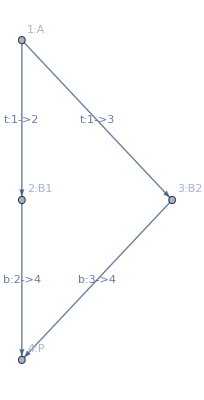

```mathematica
(* This is the example called "Figure 1" in the EBSL paper. *)
g0;
AddUser[%,"A"];
AddUser[%,"B1"];
AddUser[%,"B2"];
AddAtomic[%,"P"];
AddTrust[%,1,2,x];
AddTrust[%,1,3,x];
AddBelief[%,2,4,y];
AddBelief[%,3,4,z];
paperFig1=%
```

```mathematica
(* The paper's "Figure 1" is a simple case in which EBSL and SPIL give effectively the same symbolic result (though with one difference in operator; SPIL uses propagate where EBSL uses discount). *)
fig1EBSL=EBSLSymbolicBelief[paperFig1,1,4,{}]
fig1SPIL=SPILf[paperFig1,1,4]
```

{x×y⊕x×z}

x⊗y⊕x⊗z

```mathematica
(* Here is an example numerical evaluation of the graph in the paper's Figure 1. The difference between the EBSL and SPIL answers derives from the difference between the discount and propagate operators (consensus is the same). *)
fig1Subs:={x->{6/10,1/10,3/10},y->{3/10,6/10,1/10},z->{5/10,2/10,3/10}}
N[EvalBelief[fig1EBSL/.fig1Subs]]
N[EvalBelief[fig1SPIL/.fig1Subs]]
```

{{0.358974,0.512821,0.128205}}

{0.313502,0.341438,0.345059}

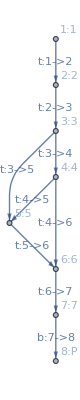

```mathematica
(* This is the example called "Figure 2" in the paper. *)
g0;
AddUser[%,"1"];
AddUser[%,"2"];
AddUser[%,"3"];
AddUser[%,"4"];
AddUser[%,"5"];
AddUser[%,"6"];
AddUser[%,"7"];
AddAtomic[%,"P"];
AddTrust[%,1,2,A12];
AddTrust[%,2,3,A23];
AddTrust[%,3,4,A34];
AddTrust[%,3,5,A35];
AddTrust[%,4,5,A45];
AddTrust[%,4,6,A46];
AddTrust[%,5,6,A56];
AddTrust[%,6,7,A67];
AddBelief[%,7,8,T7P];
paperFig2=%
```

```mathematica
(* The symbolic EBSL and SPIL solutions to Fig. 2. The SPIL solution has a three-way join corresponding to the three different sets of paths we can choose through the complicated part of the graph without double-counting: those corresponding to removing 4->6, 4->5, and 3->5 respectively. That join is bracketed in its entirety by propagates on either side, so that the entire formula is bounded by all of A12, A23, A67, and T7P, as I argue that it ought to be, because 1's entire belief in 8 depends on each of those edges -- the removal of any one of those edges would leave 1 with no belief in 8 at all. Graph-theoretically, each of those edges by itself forms a singleton edge s-t cut between 1 and 8. EBSL does not make such guarantees, for example about A12. Its discount operator is not bounded by the left-hand side, so if A12 represented a very small belief (a high uncertainty) but A23 represented near-certain belief, then the (A12×A23) term would still represent a large amount of belief (low uncertainty), much more than A12 alone. Furthermore, even if its discount operator _were_ bounded, then it could not be distributive, so the appearance of that A12×A23 term three times in consensus could produce a term that was not bounded by either A12 or A23. The SPIL propagate operator is bounded and therefore not distributive, but it does not feature any consensus that could break the upper bound (represented by any of A12, A23, A67, or T7P) because of the graph-cutting performed by AttenuatedFlow. *)
fig2EBSL=EBSLSymbolicBelief[paperFig2,1,8,{}]
fig2SPIL=SPILf[paperFig2,1,8]
```

{((((A12×A23)×A34)×A46⊕((A12×A23)×A35⊕((A12×A23)×A34)×A45)×A56)×A67)×T7P}

A12⊗(A23⊗((((A35⊕A34⊗A45)⊗A56)⋁(A34⊗A46⊕A35⊗A56))⋁(A34⊗(A46⊕A45⊗A56))⊗(A67⊗T7P)))

```mathematica
(* Numeric solutions to the above, from Dima's TestExample3. *)
EBSLNumericSolutions[paperFig2,1,{},{A12->dimaEv2bv[400,300],A23->dimaEv2bv[10,5],A34->dimaEv2bv[500,0],A35->dimaEv2bv[500,0],A45->dimaEv2bv[500,0],A46->dimaEv2bv[500,0],A56->dimaEv2bv[500,0],A67->dimaEv2bv[5,5],T7P->dimaEv2bv[10,90]}]
```

{{ℛ[1,2][b]→0.569801,ℛ[1,2][d]→0.42735,ℛ[1,2][u]→0.002849,ℛ[1,3][b]→0.540249,ℛ[1,3][d]→0.270124,ℛ[1,3][u]→0.189627,ℛ[1,4][b]→0.99265,ℛ[1,4][d]→0.,ℛ[1,4][u]→0.00734958,ℛ[1,5][b]→0.997397,ℛ[1,5][d]→0.,ℛ[1,5][u]→0.00260264,ℛ[1,6][b]→0.997994,ℛ[1,6][d]→0.,ℛ[1,6][u]→0.00200597,ℛ[1,7][b]→0.416527,ℛ[1,7][d]→0.416527,ℛ[1,7][u]→0.166946,ℱ[1,8][b]→0.0954184,ℱ[1,8][d]→0.858765,ℱ[1,8][u]→0.0458162}}

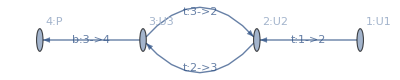

{ℛ[1,2]==A12⊕ℛ[1,3]×A32,ℛ[1,3]==ℛ[1,2]×A23,ℱ[1,4]==ℛ[1,3]×T3P}

{{0.0661956,0.,0.933804}}

{{0.888903,0.,0.111097}}

{{ℛ[1,2][b]→0.353553,ℛ[1,2][d]→0.353553,ℛ[1,2][u]→0.292893,ℛ[1,3][b]→0.207107,ℛ[1,3][d]→0.207107,ℛ[1,3][u]→0.585786,ℱ[1,4][b]→0.146447,ℱ[1,4][d]→0.146447,ℱ[1,4][u]→0.707107}}

True

```mathematica
(* This example is called Fig. 3 in the EBSL paper. I shall use it to illustrate my concern about EBSL's propagation of trust through cycles. See the "Propagation of trust through cycles" concern in the introduction for a discussion of these results. *)
g0;
AddUser[%,"U1"];
AddUser[%,"U2"];
AddUser[%,"U3"];
AddAtomic[%,"P"];
AddTrust[%,1,2,A12];
AddTrust[%,2,3,A23];
AddTrust[%,3,2,A32];
AddBelief[%,3,4,T3P];
paperFig3=%
AllMatrixEqs[paperFig3,1]
paperFig3NumericSubs1:={A12->{1/100,0,99/100},A23->{5/10,0,5/10},A32->{5/10,0,5/10},T3P->{7/10,2/10,1/10}}
paperFig3NumericSubs2:={A12->{1/100,0,99/100},A23->{9/10,0,1/10},A32->{9/10,0,1/10},T3P->{7/10,2/10,1/10}}
paperFig3Solutions1=EBSLNumericTrust[paperFig3,1,3,{},paperFig3NumericSubs1]
paperFig3Solutions2=EBSLNumericTrust[paperFig3,1,3,{},paperFig3NumericSubs2]
(* Dima's numbers from TestExample. *)
paperFig3NumericSubsDima:={A12->dimaEv2bv[2,2],A23->dimaEv2bv[2,2],A32->dimaEv2bv[2,2],T3P->dimaEv2bv[2,2]}
paperFig3SolutionsDima=EBSLNumericSolutions[paperFig3,1,{},paperFig3NumericSubsDima]
CheckEBSLNumericSolutions[paperFig3,1,{},paperFig3NumericSubsDima,paperFig3SolutionsDima]
```

```mathematica
(* The SPIL solution which does not chase cycles produces straightforward symbolic and numeric results, and the numeric results make far more sense to me than the EBSL results, as described in the "Concerns about EBSL" section's discussion of propagation of trust through cycles. *)
SPILf[paperFig3,1,3]
SPILfExN[paperFig3,1,3,paperFig3NumericSubs1]
SPILfExN[paperFig3,1,3,paperFig3NumericSubs2]
SPILfExN[paperFig3,1,3,paperFig3NumericSubsDima]
SPILfExN[paperFig3,1,4,paperFig3NumericSubs1]
SPILfExN[paperFig3,1,4,paperFig3NumericSubs2]
SPILfExN[paperFig3,1,4,paperFig3NumericSubsDima]
```

A12⊗A23

{0.005,0.,0.995}

{0.009,0.,0.991}

{0.111111,0.111111,0.777778}

{0.0035,0.001,0.9955}

{0.0063,0.0018,0.9919}

{0.037037,0.037037,0.925926}

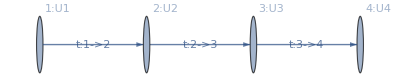

A12⊗(A23⊗A34)

{{0.25,0.,0.75}}

{0.125,0.,0.875}

{{0.333333,0.,0.666667}}

{0.25,0.,0.75}

```mathematica
(* This chain of trust four users long illustrates the non-associativity of EBSL's discount (and the associativity of SPIL's propagate) discussed in one of my "Concerns about EBSL" in the introduction. Dima illustrated this in golang in TestExample4. *)
g0;
AddUser[%,"U1"];
AddUser[%,"U2"];
AddUser[%,"U3"];
AddUser[%,"U4"];
AddTrust[%,1,2,A12];
AddTrust[%,2,3,A23];
AddTrust[%,3,4,A34];
nonAssociativeChainExample=%
SPILf[nonAssociativeChainExample,1,4]
nonAssociativeChainExampleNumericSubs:={A12->{1/2,0,1/2},A23->{1/2,0,1/2},A34->{1/2,0,1/2}}
EBSLNumericTrust[nonAssociativeChainExample,1,4,{},nonAssociativeChainExampleNumericSubs]
SPILfExN[nonAssociativeChainExample,1,4,nonAssociativeChainExampleNumericSubs]
EBSLNumericTrust[nonAssociativeChainExample,2,4,{},nonAssociativeChainExampleNumericSubs]
SPILfExN[nonAssociativeChainExample,2,4,nonAssociativeChainExampleNumericSubs]
```

```mathematica
(* This corresponds to the hypothetical change described in the introductory concern about the EBSL discount operator's non-associativity in which one pair of consecutive edges were imagined to be a single edge (i.e. one form of trust with one indirection were imagined to be direct, with the same value as the indirect trust). SPIL gives the same answer as in the original case, but EBSL gives a different answer -- lesser belief resulting from more direct trust. Dima illustrated this in golang in TestExample5. *)
EBSLNumericTrust[nonAssociativeChainExample,1,3,{},{A12->{1/2,0,1/2},A23->{1/3,0,2/3},A34->{0,0,1}}]
SPILfExN[nonAssociativeChainExample,1,3,{A12->{1/2,0,1/2},A23->{1/4,0,3/4},A34->{0,0,1}}]
```

{{0.2,0.,0.8}}

{0.125,0.,0.875}

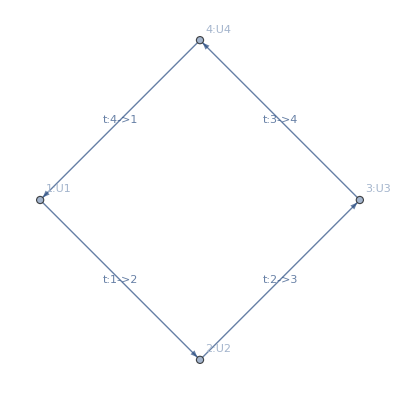

{{ℛ[1,2][b]→0.333333,ℛ[1,2][d]→0.333333,ℛ[1,2][u]→0.333333,ℛ[1,3][b]→0.2,ℛ[1,3][d]→0.2,ℛ[1,3][u]→0.6,ℛ[1,4][b]→0.142857,ℛ[1,4][d]→0.142857,ℛ[1,4][u]→0.714286}}

```mathematica
(* This is Dima's TestExample2. *)
dimaTestExample2=AddTrust[nonAssociativeChainExample,4,1,A41]
dimaTestExample2NumericSubs:={A12->dimaEv2bv[2,2],A23->dimaEv2bv[2,2],A34->dimaEv2bv[2,2],A41->dimaEv2bv[2,2]}
EBSLNumericSolutions[dimaTestExample2,1,{},dimaTestExample2NumericSubs]
```

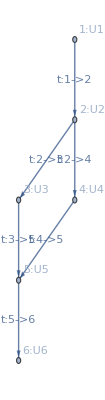

{((A12×A23)×A35⊕(A12×A24)×A45)×A56}

A12⊗((A23⊗A35⊕A24⊗A45)⊗A56)

```mathematica
(* This is the first of a few examples of "diamond" shapes, where trust splits and merges, which illustrate how the forms of the EBSL and SPIL equations differ in those cases, because of SPIL's graph operations, as encapsulated in AttenuatedFlow. In particular, the SPIL equations manifestly show bottlenecks (single edges or subgraphs through which all of the trust in some particular graph must pass) as bounds for the entire flow of trust in that they appear as terms in chains of propagations. *)
g0;
AddUser[%,"U1"];
AddUser[%,"U2"];
AddUser[%,"U3"];
AddUser[%,"U4"];
AddUser[%,"U5"];
AddUser[%,"U6"];
AddTrust[%,1,2,A12];
AddTrust[%,2,3,A23];
AddTrust[%,2,4,A24];
AddTrust[%,3,5,A35];
AddTrust[%,4,5,A45];
AddTrust[%,5,6,A56];
middleDiamond=%
EBSLSymbolicTrust[middleDiamond,1,6,{}]
SPILf[middleDiamond,1,6]
```

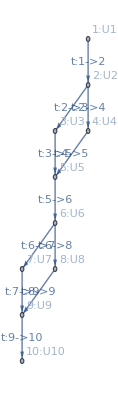

{(((((A12×A23)×A35⊕(A12×A24)×A45)×A56)×A67)×A79⊕((((A12×A23)×A35⊕(A12×A24)×A45)×A56)×A68)×A89)×A910}

A12⊗((A23⊗A35⊕A24⊗A45)⊗(A56⊗((A67⊗A79⊕A68⊗A89)⊗A910)))

```mathematica
(* This extends the "middleDiamond" example by placing another diamond after it, with a single bottleneck edge in between.  Note how the bottleneck, A56, is explicitly one term in a chain of propagations in the SPIL equation. *)
middleDiamond;
AddUser[%,"U7"];
AddUser[%,"U8"];
AddUser[%,"U9"];
AddUser[%,"U10"];
AddTrust[%,6,7,A67];
AddTrust[%,6,8,A68];
AddTrust[%,7,9,A79];
AddTrust[%,8,9,A89];
AddTrust[%,9,10,A910];
diamondsOnString=%
EBSLSymbolicTrust[diamondsOnString,1,10,{}]
SPILf[diamondsOnString,1,10]
```

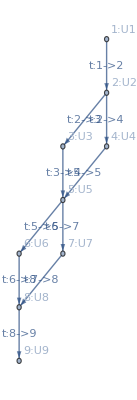

{((((A12×A23)×A35⊕(A12×A24)×A45)×A56)×A68⊕(((A12×A23)×A35⊕(A12×A24)×A45)×A57)×A78)×A89}

A12⊗((A23⊗A35⊕A24⊗A45)⊗((A56⊗A68⊕A57⊗A78)⊗A89))

```mathematica
(* This is another variant on consecutive diamonds, this time with no bottleneck edge in between. *)
g0;
AddUser[%,"U1"];
AddUser[%,"U2"];
AddUser[%,"U3"];
AddUser[%,"U4"];
AddUser[%,"U5"];
AddUser[%,"U6"];
AddUser[%,"U7"];
AddUser[%,"U8"];
AddUser[%,"U9"];
AddTrust[%,1,2,A12];
AddTrust[%,2,3,A23];
AddTrust[%,2,4,A24];
AddTrust[%,3,5,A35];
AddTrust[%,4,5,A45];
AddTrust[%,5,6,A56];
AddTrust[%,5,7,A57];
AddTrust[%,6,8,A68];
AddTrust[%,7,8,A78];
AddTrust[%,8,9,A89];
repeatedDiamond=%
EBSLSymbolicTrust[repeatedDiamond,1,9,{}]
SPILf[repeatedDiamond,1,9]
```

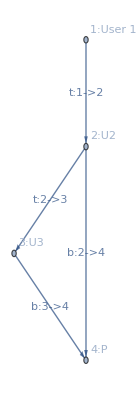

```mathematica
(* This example illustrates that in SPIL, unlike in EBSL, we can not separate the steps of computing trust in users and then belief in propositions: the reason is that SPIL tries to make sure not to duplicate evidence for propositions through paths that are not independent.*)
g1;
AddUser[%,"U2"];
AddUser[%,"U3"];
AddAtomic[%,"P"];
AddTrust[%,1,2,A12];
AddTrust[%,2,3,A23];
AddBelief[%,2,4,T24];
trianglePropExample=AddBelief[%,3,4,T34]
```

```mathematica
(* As usual, the SPIL equation shows that the final belief in P is limited by the bottleneck edge A12. *)
SPILf[trianglePropExample,1,4]
```

A12⊗(T24⊕A23⊗T34)

```mathematica
(* Here is an example of a numeric solution, selected for illustrating the case when the trust in the bottleneck edge is small, so the net belief of user 1 in proposition P ought, in SPIL, to be correspondingly small. *)
trianglePropNumericSubs:={A12->{1/1000,0,999/1000},A23->{999/1000,0,1/1000},T24->{999/1000,0,1/1000},T34->{999/1000,0,1/1000}}
```

```mathematica
(* Here we illustrate the importance of the non-distributivity of SPIL's propagate. If we were to rewrite the symbolic equation as if ⊗ were distributive over ⊕, then we would obtain more trust in P than should be allowed by the trust through the bottleneck edge A12 (i.e. user 1's trust in user 2, upon which user 1's entire belief in proposition P depends). *)
SPILfExN[trianglePropExample,1,4,trianglePropNumericSubs]
N[EvalBelief[(A12⊗T24⊕A12⊗(A23⊗T34))/.trianglePropNumericSubs]]
```

{0.000999333,0.,0.999001}

{0.00199501,0.,0.998005}

```mathematica
(* Now we examine the same example in the EBSL context. *)
trianglePropSymbolic=EBSLSymbolicBelief[trianglePropExample,1,4,{}]
```

{A12×T24⊕(A12×A23)×T34}

```mathematica
(* Here is the numeric solution with the same substitution as we used for SPIL. First, we observe that the unboundedness of the EBSL discount operator gives user 1 a very high numeric belief in proposition P even though all of that belief depends on a very small trust A12. *)
N[EvalBelief[trianglePropSymbolic/.trianglePropNumericSubs]]
```

{{0.998005,0.,0.00199502}}

```mathematica
(* Now we observe the impact of the non-associativity of discount on the EBSL paper's argument that they avoid double-counting. They claim that the the left-distributivity of × over ⊕allows them to write, for example, A12×T24⊕A12×T34 as A12×(T24⊕T34), where the latter equation manifestly avoids double-counting. That is true, but that is only one possible equation, and it does not appear to me to be generally representative. In this example, the EBSL solution is A12×T24⊕(A12×A23)×T34, and we can _not_ rewrite that as A12×(T24⊕A23×T34) because we can not rewrite (A12×A23)×T34 as A12×(A23×T34). We get a different answer from the real numeric solution when we make the same numeric substitution into the equation that manifestly avoids double-counting, namely A12×(T24⊕A23×T34): *)
N[EvalBelief[(A12×(T24⊕A23×T34))/.trianglePropNumericSubs]]
```

{0.666333,0.,0.333667}

```mathematica
(* Notice that we got vastly more belief from the real EBSL equation than from the one that manifestly avoids double-counting. So I think that the lack of associativity of × invalidates the paper's argument that the left-distributivity of × over ⊕ prevents double-counting. *)
```

Alternative Definitions (for future consideration)

```mathematica
(* A more general evidence-scaling operator which takes into account evidence that suppresses propagation ("negative evidence") as well as evidence that favors propagation ("positive evidence"). *)
evPropagate[evlpos_,evlneg_,evrpos_,evrneg_]:=
Module[{evltot=evlpos+evlneg,evrtot=evrpos+evrneg},
(evlpos*evrpos)/(1+evltot+evrtot+evltot*evrtot-evlpos*evrpos)
]
```

```mathematica
(* evPropagate reduces to evScale when there's no negative (suppressing) evidence. *)
Simplify[evPropagate[evlpos,0,evrpos,0]==evScale[evlpos,evrpos]]
```

True

```mathematica
(* evPropagate does not propagate more evidence than there is positive evidence for either argument. *)
Resolve[ForAll[{evlpos,evlneg,evrpos,evrneg},And[evlpos∈Reals,evlneg∈Reals,evlpos>0,evlneg>0,evrpos∈Reals,evrneg∈Reals,evrpos>0,evrneg>0],evPropagate[evlpos,evlneg,evrpos,evlneg]<evlpos]]
Resolve[ForAll[{evlpos,evlneg,evrpos,evrneg},And[evlpos∈Reals,evlneg∈Reals,evlpos>0,evlneg>0,evrpos∈Reals,evrneg∈Reals,evrpos>0,evrneg>0],evPropagate[evlpos,evlneg,evrpos,evlneg]<evrpos]]
```

True

True

```mathematica
(* evPropagate is commutative. *)
Resolve[ForAll[{xp,xn,yp,yn},And[xp>0,xn>0,yp>0,yn>0],evPropagate[xp,xn,yp,yn]==evPropagate[yp,yn,xp,xn]]]
```

True

```mathematica
(* evPropagate is associative. *)
Resolve[ForAll[{xp,xn,yp,yn,zp,zn},And[xp>0,xn>0,yp>0,yn>0,zp>0,zn>0],evPropagate[xp,xn,evPropagate[yp,yn,zp,zn],0]==evPropagate[evPropagate[xp,xn,yp,yn],0,zp,zn]]]
```

True

```mathematica
(* Dot is equivalent to evidence-viewpoint propagation (evPropagate). *)
SimplifyBelief[bv2evp[{xb,xd,xu}⊙{yb,yd,yu}]=={evPropagate[bv2evb[{xb,xd,xu}],bv2evd[{xb,xd,xu}],bv2evb[{yb,yd,yu}],bv2evd[{yb,yd,yu}]],0},✓[{{xb,xd,xu},{yb,yd,yu}}]]
```

True

```mathematica
(* Contradot is equivalent to evidence-viewpoint propagation (evPropagate). *)
SimplifyBelief[bv2evp[{xb,xd,xu}⊖{yb,yd,yu}]=={0,evPropagate[bv2evb[{xb,xd,xu}],bv2evd[{xb,xd,xu}],bv2evd[{yb,yd,yu}],bv2evb[{yb,yd,yu}]]},✓[{{xb,xd,xu},{yb,yd,yu}}]]
```

True

```mathematica
(* Not is equivalent to evidence-viewpoint propagation (evPropagate): this expression approaches xb as ud->∞, which is evPropagate of x with Unsupportable. (So we propagate xb of belief, and it goes to disbelief in the antecedent.) *)
Simplify[ev2bd[evPropagate[bv2evb[{xb,xd,xu}],bv2evd[{xb,xd,xu}],ud,0]]]
```

-(ud xb (-1+xu))/((1+ud) (xb+xd))

```mathematica
(* The above definition is _not_ equivalent to the following one, but maybe the following one is preferable, as it might represent that a propagate is a consensus of belief inherited from belief and belief with disbelief inherited from belief and disbelief (because it's consensus of pure belief with pure disbelief, that's equivalent to join): *)
propagateAlt[{xb_,xd_,xu_},{yb_,yd_,yu_}]:=evp2bv[{evPropagate[bv2evb[{xb,xd,xu}],bv2evd[{xb,xd,xu}],bv2evb[{yb,yd,yu}],bv2evd[{yb,yd,yu}]],evPropagate[bv2evb[{xb,xd,xu}],bv2evd[{xb,xd,xu}],bv2evd[{yb,yd,yu}],bv2evb[{yb,yd,yu}]]}]
SimplifyBelief[(propagateAlt[{xb,xd,xu},{yb,yd,yu}])==({xb,xd,xu}⊙{yb,yd,yu})⊕({xb,xd,xu}⊖{yb,yd,yu})==({xb,xd,xu}⊙{yb,yd,yu})⋁({xb,xd,xu}⊖{yb,yd,yu}),And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}]]]
```

True

```mathematica
(* propagateAlt preserves validity. *)
ResolveValidBelief[{xb,xd,xu,yb,yd,yu},And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}],xb>0,yb>0],propagateAlt[{xb,xd,xu},{yb,yd,yu}]]
```

True

```mathematica
(* propagateAlt is more conservative than propagate. *)
SimplifyBelief[belief[propagateAlt[{xb,xd,xu},{yb,yd,yu}]]≤belief[propagate[{xb,xd,xu},{yb,yd,yu}]],And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}]]]
SimplifyBelief[disbelief[propagateAlt[{xb,xd,xu},{yb,yd,yu}]]≤disbelief[propagate[{xb,xd,xu},{yb,yd,yu}]],And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}]]]
(* This one looks provable to me, but Mathematica can't seem to do it.
SimplifyBelief[bv2evb[propagateAlt[{xb,xd,xu},{yb,yd,yu}]]≤bv2evb[propagate[{xb,xd,xu},{yb,yd,yu}]],And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}]] *)
SimplifyBelief[bv2evd[propagateAlt[{xb,xd,xu},{yb,yd,yu}]]≤bv2evd[propagate[{xb,xd,xu},{yb,yd,yu}]],And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}]]]
```

True

True

True

```mathematica
(* An algebraic formula for propagateAlt directly in terms of the belief vector components. It might be possible to simplify this further. *)
SimplifyBelief[propagateAlt[{xb,xd,xu},{yb,yd,yu}]=={(xb) (1-xb yd) (yb)(1-xu)(1-yu),xb yd (1-yu)(xd+xb (xu yb+(1-yb))),(1-xb yd) (xd (1-yu)+xb (yd+yb yu+xu yb(1- yu)))}/((1-xu)*(1-yu)*(1-xb^2 yb yd)),And[OverVector[{xb,xd,xu}],OverVector[{yb,yd,yu}]]]
```

True

Future Work

So far I have only implemented two propositional connectives, implication and negation. At least conjunction and disjunction would be important to a practical propositional logic as well.

I should consider using the “Alternative Propagate” (propagateAlt) in the section above in place of the current propagate operator.

In the EBSL paper’s “Theorem 1”, they define a function 𝒻 during the course of the proof of the theorem which they show must take the form 𝒻(𝓅,𝓃)=𝓅+𝓃+𝒸 for some constant 𝒸.  In the SPIL definitions, I have effectively taken 𝒸=1.  I should investigate whether that is an inevitable consequence of some of the expanded ways in which SPIL uses belief/evidence transformations (such as the new evidence-scaling formulas evScale and evPropagate), or whether the SPIL definitions could also be parameterized on arbitrary 𝒸.

I think it would make sense to add an edge type representing implications that were provable theorems (where the proof would be verified by the software itself before adding the edge to the graph). Such an edge would pass all belief (but not disbelief -- that would be the fallacy of the inverse!) from the source to the target vertex; it would be equivalent to propagate with Proven, which makes sense as a formally proven theorem is the one kind of statement which we can rationally believe with zero uncertainty.

A mechanically-verified theorem, therefore, represents an exception to the disallowance of what the EBSL paper calls “dogmatic beliefs” -- beliefs with zero uncertainty. The reason that EBSL disallows such beliefs is fundamentally that if it were to end up having to take consensus between dogmatic certainty (what SPIL calls “Proven”) and dogmatic uncertainty (“Unsupportable”), the result would be indeterminate, a division of zero by zero.

In SPIL with reasoning, however, Proven makes sense. Furthermore, so does Unsupportable -- that we could actually allow (as another piece of future work).  This is because in SPIL, Unsupportable does not represent dogmatic belief. It’s an intuitionistic logic, so it only represents dogmatic resistance to provability -- it’s not saying “I’m certain this statement is false”, but rather simply “no amount of evidence can convince me of this”.  That actually has a practical use -- for example, imagine that we have many friends whom we mostly trust a great deal, but several of whom we feel have fallen under the spell of some con artist. We need not abandon all of our trust in our friends in order to avoid deriving beliefs from the con artist. Rather, we can assign a direct trust of Unsupportable to the con artist. That will cause any of our friends’ trust in the con artist to take consensus with Unsupportable, yielding Unsupportable, which in turn will not propagate any belief, so we will not derive any belief from the con artist, no matter how much our friends might trust them. Unsupportable, therefore, could play the role in SPIL of a time-honored feature of social media: “Block User”. (See “blockUserExample” above.)

That would force SPIL to answer the question of what happens when Proven takes consensus with Unsupportable, but now there is a clear correct answer:  by Unsupportable we have stated that no amount of evidence will convince us of the provability of some statement in the real world, but Proven represents that the statement is actually mathematically provable, a logical necessity. Real-world evidence is therefore irrelevant. The correct output of such a consensus is Proven.

A further leap in the power of the logic to perform real-world reasoning would be to extend from propositional to predicate logic. Quantified theorems would make it much easier to use mathematics in reasoning, and a higher-order logic, in which we could form predicates about predicates themselves, would have applications such as the following:

In a higher-order logic, trust itself could become a definable property rather than a primitive one. Our trust in another user represents a statement that that user’s trust in further users or belief in propositions will cause us to inherit further trust and belief ourselves.

A crucial aspect of real-world trust brought up to me in conversation and not accounted for in either EBSL or the current formulation of SPIL is that our trust in other people is often (perhaps as often as nearly always!) domain-dependent. I am unlikely to want to inherit someone’s political opinions just because I think that they are a brilliant physicist or that they share my tastes in restaurants. Rather, I would like to be able to say “I trust this user’s opinions about physics [only]”. In a single-domain implementation of EBSL or SPIL (such as, perhaps, a physics community, or a trust system for e-commerce), this might be unnecessary, but general real-world problem-solving can be extremely cross-disciplinary, so it would represent a huge leap in the power of the system if it could express domain-specific trust and the classification of propositions into domains (which is itself a matter of belief with uncertainty). [9]

Another form of logic which I would be eager to integrate into SPIL is causal logic, as pioneered by Judea Pearl [4]. As a formalization of reasoning about interventions and counterfactuals, it strikes me as another crucial component of real-world problem-solving, and perhaps a good fit for merging with SPIL (it is also highly graph-oriented).

Speaking of Dr. Pearl, long after I had conceived both the intuitionistic interpretation of SPIL and the desire to integrate it with Pearl’s causal logic, I was surprised to learn (from Wikipedia) that he had published on the subject of Dempster-Shafer theory, the source of the belief vectors used ubiquitously in EBSL and SPIL -- and astonished to read Wikipedia’s summary of some of his publications: ‘it is misleading to interpret belief functions as representing either “probabilities of an event,” [ .... ]  Instead, belief functions represent the probability that a given proposition is provable from a set of other propositions, to which probabilities are assigned. Confusing probabilities of truth with probabilities of provability may lead to counterintuitive results in reasoning tasks...’. [10]  That sounds to me precisely like an argument for an intuitionistic as opposed to a classical interpretation (provability rather than truth)!  While this is hardly a stamp of approval from one of my mathematical heroes, I will at least take it as a good sign to have had one thought resembling any of those of the 2011 Turing Award winner.

Dr. Pearl also wrote a critique of one abstraction of Dempster-Shafer theory called “belief functions” [7]. After a brief scan, I do not anywhere close to fully understand them, but I don’t think that that particular abstraction is used by EBSL (or inherited by SPIL). It is worth looking at more closely, though.

The authors of the EBSL paper later published about extending trust to reputation [5]. I have put little to no thought yet into adding reputation into SPIL; I focused on the reasoning extension (and the revamping of the foundations whose necessity I felt that that extension revealed). Determining whether the EBSL authors’ reputation work could be sensibly integrated into SPIL would be valuable.

As the extensions I would like to make mostly seem to constitute new forms of logic -- predicate logic, causal logic, perhaps reputation logic -- perhaps an even more ambitious extension could subsume them all:  to use SPIL’s graph operations, and the belief vectors and pieces-of-evidence interpretation that it inherits from EBSL, in a logic strong and expressive enough to do practical general mathematics, such as some inductive dependent type theory, thus producing a foundation for general formal distributed reasoning with subjectivity, individualization, and uncertainty.  A Subjective Propagating Intuitionistic Type theory could have applications not only within domains such as physics, economics, and politics, but perhaps most important, in integrating the findings from all into real-world distributed reasoning and negotiation. Enormously complicated policy decisions might be performed much more smoothly through the application of SPIT.

One good candidate, I think, for a much more powerful logic underlying SPIL would be the Calculus of Constructions [11] (or its extension to the Calculus of Inductive Constructions [12], or the further extension to the Calculus of Coinductive Instructions).  It might even be possible to parameterize SPIL/SPIT upon arbitrary underlying logics (those that can be cast in natural-deduction forms, at least, and perhaps with additional constraints), factoring out the subjective/uncertain/belief-vector and graph-theoretical components from the trust/logical components (I have already tried to arrange this presentation in that way to a significant degree).

SPIL and the putative aforementioned SPIT might be considered (I say “might” because I genuinely do not know; I am new to the subject) examples of what appears to be called “approximate reasoning” [8]. Before going much further with it, it would be worth poking around that subject to try to figure out what might already be known (or even invalidated) among what I’ve done and would like to do.

This paper pretty much addresses the theory only:  what outputs SPIL gives, and why.  If it is ever to become the foundational logic of a real, large system, many practicalities will have to be worked out.  (I at least don’t know of any reason that it would be harder to implement on a worldwide scale than EBSL -- I don’t expect that it’d be easy to use numerical methods to find approximate solutions quickly to millions of million-parameter systems of recurrence equations, either.) My first very shallow imaginings of a real system would involve a database supporting snapshots and clones (such as one built on a Merkle tree) and capable of serializing efficient deltas between snapshots, and a system built on top of it resembling that of many backup systems which would perform frequent quick, conservative (that is, never exceeding the correct theoretical amount of belief or disbelief, but allowed to underestimate it) calculations on snapshot deltas (analogous to incremental backups) to provide quick feedback to users, and less frequent slower, theoretically maximal (or at least closer to it) computations (analogous to periodic full backups) calculations to make sure that nothing was missed for “too long”.  The value of supporting not only snapshots but also clones would be that within a clone, a user could perform exploratory, interventional/counterfactual questions such as “what would happen if I made the following change?”. In an exploratory clone, a user could even learn what the effects would be of other users changing some of their trust and belief vectors. I can imagine this being useful in negotiations:  each party could use such explorations to help determine what the “sticking points”  were, and thus what they might be able to offer to reach a deal beneficial to all.

While I would expect some underlying database to support the necessary transactional (ACID) properties, snapshots, and clones, the query optimization would be heavily dependent on the structure of the logic;  for example, we would probably like to allow users to specify which trust/belief values they’re interested in, and to restrict computation insofar as possible to the graph components required to compute the values that people actually care about (and perhaps to prioritize those that the most people care about, without starving any that anyone cares about).

One approach which I’ve only glanced at but which might be promising for efficient online cycle detection and topological ordering maintenance is [13].

It strikes me as important to be able to trust a trust-management system, so I would strongly like to specify formally and machine-check SPIL’s intended security properties (the ones that are supposed to place firm, locally computable maxima on the greatest amount of trust that a user can have for another user, or that any user can have in a user), such as the non-double-counting of edges by AttenuatedFlow, and the bounding of incoming and outgoing trust by the consensus of the incoming and outgoing belief vectors respectively, the attenuation of flow between nodes with each intervening propagation, and the independence of the output of AttenuatedFlow with respect to the order in which vertex cuts were made for a given graph (that would probably depend on the associativity of chain, merge, and join, as well as the commutativity of the latter two), and the associativity of the SPIL chain, merge, and join operations specifically (and the commutativity of the latter two).  In the case of future algorithms optimized for real, large-scale use (as opposed to the ones in this paper, which are attempts at simple and readable ways to produce correct output with almost no regard for efficiency at all), further conditions I would like to verify mechanically would include correct concurrency and incremental update, eventual full maximal correct flow (even if in practice a fast approximate algorithm would rarely reach that point, but would be continually being restarted against later snapshots, while a slower algorithm attempted to compute full maximum flow on less-frequent snapshots), and reasonable time and space bounds (where “reasonable” would be more lax for the slower, less-frequent, hopefully-maximal (not just approximate) algorithm).

In light of the resemblance between the security conditions and the max-flow/min-cut theorem, a formalization might involve a minimum cut, but it would also need to take into account the desired attenuation with distance from the source of the trust.  An analogue of the max-flow/min-cut theorem might be the statement that the flow of trust from a source to a sink can not exceed the minimum value for any edge cut between the source and sink of the consensus of all of the edges’ belief vectors, but to take into account the attenuation, perhaps this must be replaced recursively with the chain (propagate) of the maximum flows between the source and the edge cut and the edge cut and the sink.

One question whose answer could have far-reaching effects occurs to me: should I separate the flow of belief and disbelief? Would a proper security condition, for example, maximize the flow of disbelief while minimizing the flow of belief? The idea is that in subgraphs with multiple choices for maximal partitionable subgraphs -- the cases where we use join -- we might have some subsets in which some edge which carries a lot of disbelief isn’t used, allowing a lot more belief to be propagated in that subgraph than in some other subgraphs, and could that be considered insecure -- a failure of suppression? Consider contradotOddSuppressionExample for a case where I wonder whether disbelief should be maximized on both sides of a dot operation. Maybe an idea would have to integrate belief vs. disbelief into the graph theory itself, in such a way that we would never ignore disbelief in any graph?  Is that possible?  Or would it be enough to change the join operator ⋁ (and its optimizations in 𝔍) to minimize belief, while still maximizing disbelief?  A firm answer to this question would involve a reformulation of the security condition to distinguish between belief and disbelief.

It might even be the case that there is no maximal partitionable subgraph of any graph in which any belief is propagated through a user or dot node through which any relevant disbelief isn’t also propagated, but I am not at all sure of that.  It might also possibly be the case that that isn’t true right now, in particular with user nodes, but that it is or could be made true with proposition nodes (dot nodes in particular) and that therefore it could be fixed for user nodes automatically by extending to predicate logic and then recasting trust as a predicate!

Another possibility is that this might be possible to address in general by making a stronger requirement on partitioning than just “complete vertex partition”:  we might additionally want to use only sequences of clean vertex partitions which are in topological sort order between the source and target of trust, and that might guarantee (although, again, I’m not sure whether this is true or not yet) that any potential sources of disbelief have been factored into each input trust/belief relationship before an output trust/belief relationship is computed from them (by chaining trust or applying a logical operator).

## Footnotes/References

[1] “Flow-based reputation with uncertainty” [https://arxiv.org/abs/1402.3319] by Škorić, de Hoogh, and Zannone

[2] Intuitionistic logic paper (a natural deduction formulation) [https://www.classes.cs.uchicago.edu/archive/2003/spring/15300-1/intuitionism.pdf] by Kurtz

[3] Hilbert-style intuitionistic logic Wiki [https://en.wikipedia.org/wiki/Intuitionistic_logic#Hilbert-style_calculus]

[4] Judea Pearl’s _Book of Why_

[5] “Flow-Based Reputation: More Than Just Ranking” [https://www.worldscientific.com/doi/abs/10.1142/S0219622012500113] by Simone, Škorić, and Zannone

[6] Dempster-Shafer theory [https://en.wikipedia.org/wiki/Dempster%E2%80%93Shafer_theory]

[7] Judea Pearl’s critique of belief functions [https://www.sciencedirect.com/science/article/pii/0888613X9090013R?via%3Dihub]

[8] International Journal of Approximate Reasoning [https://www.journals.elsevier.com/international-journal-of-approximate-reasoning]

[9] Andrea Supalla and Jessica Supalla, personal communication, April-May 2019

[10] Judea Pearl’s interpretation of belief vectors [https://en.wikipedia.org/wiki/Dempster%E2%80%93Shafer_theory#Criticism]

[11] Wikipedia’s entry on the Calculus of Constructions: https://en.wikipedia.org/wiki/Calculus_of_constructions

[12] Introduction to the Calculus of Inductive Constructions: https://hal.inria.fr/hal-01094195/document

[13] A New Approach to Incremental Cycle Detection and Related Problems: https://www.cs.princeton.edu/courses/archive/spring13/cos528/topsort-1.pdf